## Error Analysis

Prepared with the help of chatgpt: 
See https://chatgpt.com/share/66fe55e3-ecd0-8007-9d39-ae15c09faa08 
for the chat

```mathematica
(*Set Directoy to the one notebook is running*)
SetDirectory[NotebookDirectory[]]
```

-Graphics-

-Graphics-

```mathematica
f[M_,m_]:= g (M-m)/(M+m)NIntegrate[2 m,{m,0,3}]
```

```mathematica
AroundReplace[f[M,m],{
m->Around[50,1],
M->Around[100,1],
g->9.80
} ]//ScientificForm
```

```mathematica
m=Around[50,1]
M=Around[100,1]
g=9.80
f[M,m]
```

```mathematica
(*Define the function*)f[M_,m_]:=9.80 (M-m)/(M+m) NIntegrate[2 M mvar,{mvar,0,M}]

(*Parameters with uncertainty*)
mMean=50;
mUncertainty=1;
MMean=100;
MUncertainty=1;

(*Generate 100 random samples from normal distributions for m and M*)
randomSamples=Table[{RandomVariate[NormalDistribution[MMean,MUncertainty]],RandomVariate[NormalDistribution[mMean,mUncertainty]]},{100}];

(*Compute the function for each random pair*)
functionValues=f@@@randomSamples;

(*Plot a histogram of the function values*)
Histogram[functionValues,20,"PDF",PlotRange->All]
```

```mathematica
(*Define the function f with Around for uncertainties*)f[M_,m_]:=g (M-m)/(M+m)

(*Use Around to include uncertainties in M and m*)
f[Around[100,1],Around[50,1]]
```

```mathematica
(*Define the function f[M,m]*)f[M_,m_]:= g (M-m)/(M+m)NIntegrate[2 m,{m,0,3}]

(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Calculate the mean and standard deviation of the results*)
meanValue=Mean[results];
stdDev=StandardDeviation[results];

(*Plot the histogram of the results*)histogram=Histogram[results,50,"PDF",PlotLabel->"Distribution of f(M,m) Values",AxesLabel->{"f(M,m)","Probability"}]

(*Display the mean,standard deviation,and the histogram*)
{meanValue,stdDev,histogram}
```

```mathematica
(*Define the function f[M,m]*)f[M_,m_]:=g (M-m)/(M+m)

(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];

(*Plot the histogram with a Gaussian fit overlay*)
histogram=Show[Histogram[results,10,"PDF",PlotLabel->"Gaussian Fit to f(M,m) Values",AxesLabel->{"f(M,m)","Probability"}],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->Red]];

(*Display the fitted parameters and the histogram*)
{fit,histogram}
```

```mathematica
(*Define the function f[M,m]*)f[M_,m_]:=g (M-m)/(M+m)
f=NInte
(*Set the number of iterations*)
iterations=100;

(*Generate 100 random values for M and m within their uncertainty ranges*)
randomM=RandomReal[{99,101},iterations];
randomm=RandomReal[{49,51},iterations];

(*Calculate f[M,m] for each random pair of values*)
results=Table[f[randomM[[i]],randomm[[i]]],{i,1,iterations}];

(*Fit the results to a normal (Gaussian) distribution*)
fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];

(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)
histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to f(M,m) Values",Bold,16],AxesLabel->{Style["f(M,m)",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];

{fit,histogram}

(*Export the plot to a PDF file*)
Export["GaussianFit_Histogram.pdf",histogramPlot,"PDF"]
```

```mathematica
(*Define a general Monte Carlo function with uncertainty propagation*)MonteCarloUncertaintyPropagation[f_,params_List,iterations_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{randomParams,results,fit,histogramPlot},(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,params}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with uncertainties as {value,uncertainty}*)
params={{100,1},{50,1}}; (*M=100±1,m=50±1*)

(*Call the general Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,100,"GeneralHistogramFit.pdf"]
```

## Generic Function

```mathematica
(*Define a general Monte Carlo function with uncertainty propagation*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,10,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)

(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with names,values,and uncertainties using an Association*)
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;

(*Call the general Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,100,"GeneralHistogramFit.pdf"]
```

```mathematica
?Histogram
```

THIS IS FINAL FORM: USE THIS ONE:

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)
g=9.80;
(*Define your specific function*)
f[M_,m_]:=g (M-m)/(M+m)

(*Define the parameters with names,values,and uncertainties using an Association*)
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;

(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
```

```mathematica
ResourceSearch["monte carlo"]
```

```mathematica
$Path
```

```mathematica
SystemOpen[$UserBaseDirectory<>"/Kernel/init.m"]
```

## Makale Analiz

-Graphics-

```mathematica
(*charge[eta,u]->1/Sqrt[6],charge[eta,d]->1/Sqrt[6],charge[eta,s]->-2/Sqrt[6],charge[pi,u]->1/Sqrt[2],charge[pi,d]->-1/Sqrt[2],eqd->-1/3,eqs->-1/3,equ->2/3,eqc->2/3,eqb->-1/3,mqs->(0.093)*(1.35),mqu->2.2 10^(-3),mqd->4.7 10^(-3),(*bunlar pole mass olarak duzeltilmis halleri*)mqc->1.28,mqb->4.18,m0->Sqrt[0.8],ss->-0.8 (0.24)^3,dd->-(0.24)^3,uu->-(0.24)^3,xi->-3.15,f3gamma->-0.0039,lam->0.5,(*lam ve LMB ayni*)LMB->0.5,(**)gssqGG->4 Pi^2 0.012,gssq->4 Pi 0.32,*)
```

```mathematica
eqd=-1/3;
eqs=-1/3;
equ=2/3;
eqc=2/3;
eqb=-1/3;
u0=1/2;
u=1/2;
v=1/2;
zero=0;
```

```mathematica
params=<|
"mqs"->{0.093*1.35,0.0},
"mqu"->{2.2*10^(-3),0.0},
"mqd"->{4.7*10^(-3),0.0},
"mqc"->{1.28,0.0},
"mqb"->{4.18,0.0},
"m0"->{Sqrt[0.8],0.0},
"m0sq"->{0.8,0.0},
"dd"->{-(0.246)^3,0.028^3},
"uu"->{-(0.246)^3,0.028^3},
"ss"->{-0.8*(0.246)^3,0.80*0.028^3},
"xi"->{-3.15,0.30},
"f3gamma"->{-0.0039,0},
"lam"->{0.5,0.0},
"LMB"->{0.5,0.0},
"gssqGG"->{4*Pi^2*0.012,0.0},
"gssq"->{4*Pi*0.32,0.0},
"Msq"-> {4.0,1.0},
"s0"->{5.25,0.25},
"m3"->{1.76,0.01},
"f3"->{1.17*10^-2,0.01*10^-2}
|>
```

<|mqs→{0.12555,0.},mqu→{0.0022,0.},mqd→{0.0047,0.},mqc→{1.28,0.},mqb→{4.18,0.},m0→{0.894427,0.},m0sq→{0.8,0.},dd→{-0.0148869,0.000021952},uu→{-0.0148869,0.000021952},ss→{-0.0119095,0.0000175616},xi→{-3.15,0.3},f3gamma→{-0.0039,0},lam→{0.5,0.},LMB→{0.5,0.},gssqGG→{0.473741,0.},gssq→{4.02124,0.},Msq→{4.,1.},s0→{5.25,0.25},m3→{1.76,0.01},f3→{0.0117,0.0001}|>

```mathematica
(*f[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,Msq_,s0_,m3_,f3_]=<<pi_rho3pl_gm53_spin3_monte_carlo_input //.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]//.ninteg->NIntegrate//.nintegrate->NIntegrate*)
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sbilmis/physics_scripts

```mathematica
fa[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,Msq_,s0_,m3_,f3_]=<<pi_rho3pl_gm53_spin3_monte_carlo_input
```

1/e ⅈ ((29 ⅈ e ⅇ^(m3^2/Msq) m0sq uu mqd)/(768 f3^2 m3^4 Msq)+((0.+0.361985 ⅈ) e ⅇ^(m3^2/Msq) uu mqd)/(f3^2 m3^4)+(5 ⅈ e ⅇ^(m3^2/Msq) m0sq uu mqd)/(64 f3^2 m3^6)+((0.+0.0786687 ⅈ) e ⅇ^(m3^2/Msq) uu integrate({s,0,s0},ⅇ^(-s/Msq)) mqd)/(f3^2 m3^6)-(3 ⅈ e ⅇ^(m3^2/Msq) uu xi integrate({s,0,s0},ⅇ^(-s/Msq)) mqd)/(64 f3^2 m3^4)-(25 ⅈ dd e ⅇ^(m3^2/Msq) m0sq integrate({s,0,s0},ⅇ^(-s/Msq)) mqd)/(576 f3^2 m3^8)-(5 ⅈ e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq)) mqd)/(48 f3^2 m3^4 π^2)-(9 ⅈ e ⅇ^(m3^2/Msq) ℽ mqu integrate({s,0,s0},ⅇ^(-s/Msq)) mqd)/(256 f3^2 m3^4 π^2)-(5 ⅈ e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq) s) mqd)/(128 f3^2 m3^6 π^2)-(25 ⅈ e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq) s^2) mqd)/(1536 f3^2 m3^8 π^2)+(9 ⅈ e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq) log(s/lam^2)) mqd)/(256 f3^2 m3^4 π^2)+(ⅈ e ⅇ^(m3^2/Msq) uu ninteg({up,1/2,1},-10 (6 up^2-6 up+1)) mqd)/(32 f3^2 m3^4)+(5 ⅈ e ⅇ^(m3^2/Msq) uu ninteg({up,1/2,1},-10 (1/2-up)^2 (6 up^2-6 up+1)) mqd)/(36 f3^2 m3^4)-(5 ⅈ e ⅇ^(m3^2/Msq) uu integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},-10 (1/2-up)^2 (6 up^2-6 up+1)) mqd)/(9 f3^2 m3^6)-(ⅈ e ⅇ^(m3^2/Msq) uu ninteg({up,1/2,1},-10 (1/2-up)^4 (6 up^2-6 up+1)) mqd)/(6 f3^2 m3^4)+(13 ⅈ e ⅇ^(m3^2/Msq) uu ninteg({up,1/2,1},-10 (up-1/2) (6 up^2-6 up+1)) mqd)/(96 f3^2 m3^4)-(5 ⅈ e ⅇ^(m3^2/Msq) uu integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},-10 (up-1/2) (6 up^2-6 up+1)) mqd)/(36 f3^2 m3^6)-(ⅈ e ⅇ^(m3^2/Msq) uu ninteg({up,1/2,1},-10 (up-1/2)^3 (6 up^2-6 up+1)) mqd)/(12 f3^2 m3^4)-(5 ⅈ e ⅇ^(m3^2/Msq) uu integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},-10 (up-1/2)^3 (6 up^2-6 up+1)) mqd)/(9 f3^2 m3^6)-(ⅈ e ⅇ^(m3^2/Msq) uu ninteg({up,1/2,1},-10 (up-1/2)^5 (6 up^2-6 up+1)) mqd)/(18 f3^2 m3^4)-(67 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqd)/(576 f3^2 m3^4 Msq)+(3 ⅈ dd e ⅇ^(m3^2/Msq) mqd)/(64 f3^2 m3^4)+(5 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqd)/(32 f3^2 m3^6)+(9 ⅈ e ⅇ^(m3^2/Msq) ℽ mqu Msq mqd)/(256 f3^2 m3^4 π^2)-(9 ⅈ e ⅇ^(m3^2/Msq-s0/Msq) ℽ mqu Msq mqd)/(256 f3^2 m3^4 π^2)+((0.+0.157555 ⅈ) dd e ⅇ^(m3^2/Msq) mqu)/(f3^2 m3^4)+(5 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqu)/(32 f3^2 m3^6)+(3 ⅈ e ⅇ^(m3^2/Msq) mqu uu)/(128 f3^2 m3^4)+(5 ⅈ e ⅇ^(m3^2/Msq) m0sq mqu uu)/(64 f3^2 m3^6)-(67 ⅈ e ⅇ^(m3^2/Msq) m0sq mqu uu)/(1152 f3^2 m3^4 Msq)+((0.+0.0393344 ⅈ) dd e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq)))/(f3^2 m3^6)-(25 ⅈ e ⅇ^(m3^2/Msq) m0sq mqu uu integrate({s,0,s0},ⅇ^(-s/Msq)))/(1152 f3^2 m3^8)-(3 ⅈ dd e ⅇ^(m3^2/Msq) mqu xi integrate({s,0,s0},ⅇ^(-s/Msq)))/(128 f3^2 m3^4)+((0.+0.799194 ⅈ) e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)))/(f3^2 m3^4)-(289 ⅈ e ⅇ^(m3^2/Msq) integrate({s,0,s0},ⅇ^(-s/Msq) s))/(17920 f3^2 m3^4 π^2)+(13 ⅈ e ⅇ^(m3^2/Msq) integrate({s,0,s0},ⅇ^(-s/Msq) s^2))/(1344 f3^2 m3^6 π^2)+(55 ⅈ e ⅇ^(m3^2/Msq) integrate({s,0,s0},ⅇ^(-s/Msq) s^3))/(10752 f3^2 m3^8 π^2)+(ⅈ dd e ⅇ^(m3^2/Msq) mqu ninteg({up,0,1/2},-10 (6 up^2-6 up+1)))/(64 f3^2 m3^4)+(13 ⅈ dd e ⅇ^(m3^2/Msq) mqu ninteg({up,0,1/2},10 (up-1/2) (6 up^2-6 up+1)))/(192 f3^2 m3^4)-(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},10 (up-1/2) (6 up^2-6 up+1)))/(72 f3^2 m3^6)+(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu ninteg({up,0,1/2},-10 (up-1/2)^2 (6 up^2-6 up+1)))/(72 f3^2 m3^4)-(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},-10 (up-1/2)^2 (6 up^2-6 up+1)))/(18 f3^2 m3^6)-(ⅈ dd e ⅇ^(m3^2/Msq) mqu ninteg({up,0,1/2},10 (up-1/2)^3 (6 up^2-6 up+1)))/(24 f3^2 m3^4)-(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},10 (up-1/2)^3 (6 up^2-6 up+1)))/(18 f3^2 m3^6)-(ⅈ dd e ⅇ^(m3^2/Msq) mqu ninteg({up,0,1/2},-10 (up-1/2)^4 (6 up^2-6 up+1)))/(12 f3^2 m3^4)-(ⅈ dd e ⅇ^(m3^2/Msq) mqu ninteg({up,0,1/2},10 (up-1/2)^5 (6 up^2-6 up+1)))/(36 f3^2 m3^4)-(17 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)))/(64 f3^2 m3^4)-(11 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},-((up-1/2) (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)))))/(12 f3^2 m3^4)-(67 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},(up-1/2)^2 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(72 f3^2 m3^4)-(ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},-(up-1/2)^3 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(3 f3^2 m3^4)-(ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,0,1/2},(up-1/2)^4 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(36 f3^2 m3^4)-(17 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)))/(32 f3^2 m3^4)-(67 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},(1/2-up)^2 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(36 f3^2 m3^4)-(ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},(1/2-up)^4 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(18 f3^2 m3^4)-(11 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},(up-1/2) (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(6 f3^2 m3^4)-(2 ⅈ e ⅇ^(m3^2/Msq) f3gamma integrate({s,0,s0},ⅇ^(-s/Msq)) ninteg({up,1/2,1},(up-1/2)^3 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))))/(3 f3^2 m3^4)+(29 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqu)/(384 f3^2 m3^4 Msq))

```mathematica
f[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,Msq_,s0_,m3_,f3_]=fa[mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,Msq,s0,m3,f3]//.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]//.ninteg->HoldForm[NIntegrate]//.nintegrate->HoldForm[NIntegrate]
```

1/e ⅈ ((29 ⅈ e ⅇ^(m3^2/Msq) m0sq uu mqd)/(768 f3^2 m3^4 Msq)+((0.+0.361985 ⅈ) e ⅇ^(m3^2/Msq) uu mqd)/(f3^2 m3^4)+(5 ⅈ e ⅇ^(m3^2/Msq) m0sq uu mqd)/(64 f3^2 m3^6)+((0.+0.0786687 ⅈ) e ⅇ^(m3^2/Msq) uu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) mqd)/(f3^2 m3^6)-(3 ⅈ e ⅇ^(m3^2/Msq) uu xi NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) mqd)/(64 f3^2 m3^4)-(25 ⅈ dd e ⅇ^(m3^2/Msq) m0sq NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) mqd)/(576 f3^2 m3^8)-(5 ⅈ e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) mqd)/(48 f3^2 m3^4 π^2)-(9 ⅈ e ⅇ^(m3^2/Msq) ℽ mqu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) mqd)/(256 f3^2 m3^4 π^2)-(5 ⅈ e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq) s,{s,0,s0}) mqd)/(128 f3^2 m3^6 π^2)-(25 ⅈ e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq) s^2,{s,0,s0}) mqd)/(1536 f3^2 m3^8 π^2)+(ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(-10 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(32 f3^2 m3^4)+(5 ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(-10 (1/2-up)^2 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(36 f3^2 m3^4)-(5 ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(-10 (1/2-up)^2 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(9 f3^2 m3^6)-(ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(-10 (1/2-up)^4 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(6 f3^2 m3^4)+(13 ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}) mqd)/(96 f3^2 m3^4)-(5 ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}) mqd)/(36 f3^2 m3^6)-(ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(-10 (up-1/2)^3 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(12 f3^2 m3^4)-(5 ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(-10 (up-1/2)^3 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(9 f3^2 m3^6)-(ⅈ e ⅇ^(m3^2/Msq) uu NIntegrate(-10 (up-1/2)^5 (6 up^2-6 up+1),{up,1/2,1}) mqd)/(18 f3^2 m3^4)+(9 ⅈ e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq) log(s/lam^2),{s,0,s0}) mqd)/(256 f3^2 m3^4 π^2)-(67 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqd)/(576 f3^2 m3^4 Msq)+(3 ⅈ dd e ⅇ^(m3^2/Msq) mqd)/(64 f3^2 m3^4)+(5 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqd)/(32 f3^2 m3^6)+(9 ⅈ e ⅇ^(m3^2/Msq) ℽ mqu Msq mqd)/(256 f3^2 m3^4 π^2)-(9 ⅈ e ⅇ^(m3^2/Msq-s0/Msq) ℽ mqu Msq mqd)/(256 f3^2 m3^4 π^2)+((0.+0.157555 ⅈ) dd e ⅇ^(m3^2/Msq) mqu)/(f3^2 m3^4)+(5 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqu)/(32 f3^2 m3^6)+(3 ⅈ e ⅇ^(m3^2/Msq) mqu uu)/(128 f3^2 m3^4)+(5 ⅈ e ⅇ^(m3^2/Msq) m0sq mqu uu)/(64 f3^2 m3^6)-(67 ⅈ e ⅇ^(m3^2/Msq) m0sq mqu uu)/(1152 f3^2 m3^4 Msq)+((0.+0.0393344 ⅈ) dd e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}))/(f3^2 m3^6)-(25 ⅈ e ⅇ^(m3^2/Msq) m0sq mqu uu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}))/(1152 f3^2 m3^8)-(3 ⅈ dd e ⅇ^(m3^2/Msq) mqu xi NIntegrate(ⅇ^(-s/Msq),{s,0,s0}))/(128 f3^2 m3^4)+((0.+0.799194 ⅈ) e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}))/(f3^2 m3^4)-(289 ⅈ e ⅇ^(m3^2/Msq) NIntegrate(ⅇ^(-s/Msq) s,{s,0,s0}))/(17920 f3^2 m3^4 π^2)+(13 ⅈ e ⅇ^(m3^2/Msq) NIntegrate(ⅇ^(-s/Msq) s^2,{s,0,s0}))/(1344 f3^2 m3^6 π^2)+(55 ⅈ e ⅇ^(m3^2/Msq) NIntegrate(ⅇ^(-s/Msq) s^3,{s,0,s0}))/(10752 f3^2 m3^8 π^2)+(ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(-10 (6 up^2-6 up+1),{up,0,1/2}))/(64 f3^2 m3^4)+(13 ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(10 (up-1/2) (6 up^2-6 up+1),{up,0,1/2}))/(192 f3^2 m3^4)-(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(10 (up-1/2) (6 up^2-6 up+1),{up,0,1/2}))/(72 f3^2 m3^6)+(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(-10 (up-1/2)^2 (6 up^2-6 up+1),{up,0,1/2}))/(72 f3^2 m3^4)-(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(-10 (up-1/2)^2 (6 up^2-6 up+1),{up,0,1/2}))/(18 f3^2 m3^6)-(ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(10 (up-1/2)^3 (6 up^2-6 up+1),{up,0,1/2}))/(24 f3^2 m3^4)-(5 ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(10 (up-1/2)^3 (6 up^2-6 up+1),{up,0,1/2}))/(18 f3^2 m3^6)-(ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(-10 (up-1/2)^4 (6 up^2-6 up+1),{up,0,1/2}))/(12 f3^2 m3^4)-(ⅈ dd e ⅇ^(m3^2/Msq) mqu NIntegrate(10 (up-1/2)^5 (6 up^2-6 up+1),{up,0,1/2}))/(36 f3^2 m3^4)-(17 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3),{up,0,1/2}))/(64 f3^2 m3^4)-(17 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3),{up,1/2,1}))/(32 f3^2 m3^4)-(67 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate((1/2-up)^2 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,1/2,1}))/(36 f3^2 m3^4)-(ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate((1/2-up)^4 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,1/2,1}))/(18 f3^2 m3^4)-(11 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(-((up-1/2) (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3))),{up,0,1/2}))/(12 f3^2 m3^4)-(11 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate((up-1/2) (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,1/2,1}))/(6 f3^2 m3^4)-(67 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate((up-1/2)^2 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,0,1/2}))/(72 f3^2 m3^4)-(ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate(-(up-1/2)^3 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,0,1/2}))/(3 f3^2 m3^4)-(2 ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate((up-1/2)^3 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,1/2,1}))/(3 f3^2 m3^4)-(ⅈ e ⅇ^(m3^2/Msq) f3gamma NIntegrate(ⅇ^(-s/Msq),{s,0,s0}) NIntegrate((up-1/2)^4 (3 (3 (2 up-1)^2-1)+3.16406 (35 (2 up-1)^4-30 (2 up-1)^2+3)),{up,0,1/2}))/(36 f3^2 m3^4)+(29 ⅈ dd e ⅇ^(m3^2/Msq) m0sq mqu)/(384 f3^2 m3^4 Msq))

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution NormalDistribution[μ,σ].

NormalDistribution::realprm: Parameter {0.989058,1.68374,1.26432,1.36796,1.39723,1.76964,1.7505,1.71298,2.0009,1.98781,«8»} at position 1 in NormalDistribution[{0.989058,1.68374,1.26432,1.36796,1.39723,1.76964,1.7505,1.71298,2.0009,1.98781,«8»},σ] is expected to be real.

General::stop: Further output of NormalDistribution::realprm will be suppressed during this calculation.

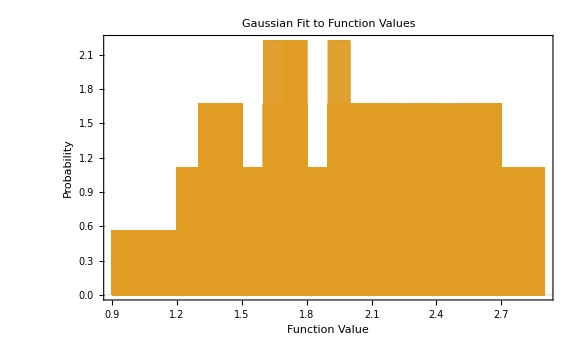
{FindDistributionParameters[(0.932439 | 1.52092 | 1.10362 | 1.27191 | 1.38165 | 1.44797 | 1.7296 | 1.64619 | 1.70992 | 1.95082 | 2.25378 | 2.27927 | 2.38899 | 2.39383 | 2.34345 | 2.55 | 2.59119 | 2.71307
0.989058 | 1.68374 | 1.26432 | 1.36796 | 1.39723 | 1.76964 | 1.7505 | 1.71298 | 2.0009 | 1.98781 | 1.90717 | 2.16384 | 2.11131 | 2.44018 | 2.63408 | 2.50111 | 2.82644 | 2.78914
1.00238 | 1.38661 | 1.16465 | 1.24204 | 1.43532 | 1.52555 | 1.78416 | 1.90454 | 1.89449 | 2.04926 | 2.00182 | 2.14261 | 2.32104 | 2.30098 | 2.55537 | 2.69664 | 2.67826 | 2.71138
1.04266 | 1.36589 | 1.16391 | 1.34275 | 1.36607 | 1.70015 | 1.69814 | 1.81449 | 2.0406 | 2.03448 | 2.15558 | 2.17503 | 2.24033 | 2.36038 | 2.42653 | 2.65856 | 2.5636 | 2.73872
0.968066 | 1.57718 | 1.12434 | 1.31835 | 1.40688 | 1.40896 | 1.62618 | 1.76986 | 1.92606 | 1.9407 | 2.00764 | 2.29156 | 2.17403 | 2.42277 | 2.46371 | 2.51598 | 2.89154 | 2.85738
1.0103 | 1.48423 | 1.19909 | 1.29337 | 1.42653 | 1.765 | 1.7696 | 1.63297 | 1.85074 | 1.91452 | 2.29519 | 2.16501 | 2.49932 | 2.43408 | 2.50078 | 2.6573 | 2.5679 | 2.89647
0.949802 | 1.50601 | 1.1363 | 1.38693 | 1.3267 | 1.41699 | 1.77138 | 1.91983 | 1.77443 | 1.95952 | 2.11034 | 2.29203 | 2.24453 | 2.46983 | 2.49935 | 2.54682 | 2.56609 | 2.78097
1.04945 | 1.54542 | 1.17202 | 1.34145 | 1.45799 | 1.70378 | 1.65044 | 1.89468 | 2.06321 | 1.97905 | 1.92683 | 2.19404 | 2.4836 | 2.38055 | 2.50791 | 2.50583 | 2.81443 | 2.74199
0.99884 | 1.53799 | 1.22382 | 1.34154 | 1.44564 | 1.50669 | 1.67286 | 1.65344 | 1.78628 | 2.09834 | 2.11187 | 2.20584 | 2.24565 | 2.34204 | 2.57449 | 2.59423 | 2.60131 | 2.76184
0.920003 | 1.45914 | 1.11877 | 1.33174 | 1.347 | 1.79495 | 1.7021 | 1.91197 | 1.93333 | 1.97152 | 2.10807 | 2.18483 | 2.19172 | 2.41317 | 2.44068 | 2.6841 | 2.58782 | 2.87531
1.0721 | 1.5666 | 1.13836 | 1.3482 | 1.48584 | 1.41658 | 1.68473 | 1.76024 | 1.89909 | 2.0534 | 1.95236 | 2.18355 | 2.34414 | 2.3268 | 2.344 | 2.50548 | 2.80045 | 2.83394
1.04799 | 1.33619 | 1.19335 | 1.31508 | 1.39925 | 1.5153 | 1.7314 | 1.68968 | 1.79187 | 2.04766 | 2.16014 | 2.1788 | 2.1164 | 2.31834 | 2.38908 | 2.57402 | 2.65532 | 2.8749
1.08754 | 1.48269 | 1.11564 | 1.3831 | 1.40006 | 1.77875 | 1.75345 | 1.97694 | 1.82163 | 1.94441 | 2.19894 | 2.24108 | 2.24359 | 2.40417 | 2.32156 | 2.50347 | 2.62571 | 2.89515
0.942787 | 1.63465 | 1.18813 | 1.31988 | 1.31466 | 1.5424 | 1.7455 | 1.99146 | 1.99088 | 1.96354 | 2.14862 | 2.26506 | 2.26586 | 2.44604 | 2.4659 | 2.62437 | 2.81149 | 2.74716
1.04203 | 1.56071 | 1.23931 | 1.27108 | 1.40042 | 1.58419 | 1.6552 | 1.89435 | 2.06519 | 2.02151 | 1.92986 | 2.19147 | 2.38416 | 2.35592 | 2.57442 | 2.61195 | 2.62118 | 2.87113
1.02957 | 1.47688 | 1.13781 | 1.26158 | 1.34584 | 1.61958 | 1.77045 | 1.67076 | 1.91834 | 2.05275 | 2.23604 | 2.12533 | 2.3175 | 2.47818 | 2.48037 | 2.56852 | 2.64969 | 2.7791
1.02228 | 1.60507 | 1.2535 | 1.2077 | 1.46028 | 1.71113 | 1.78013 | 1.63131 | 1.76822 | 1.90423 | 2.05969 | 2.16145 | 2.42534 | 2.33238 | 2.41864 | 2.52229 | 2.57786 | 2.86409
0.960027 | 1.31252 | 1.12635 | 1.20581 | 1.44028 | 1.53937 | 1.79138 | 1.68675 | 1.87425 | 2.09962 | 2.22216 | 2.17175 | 2.44189 | 2.41362 | 2.55171 | 2.53253 | 2.81023 | 2.73456
1.07855 | 1.30689 | 1.24713 | 1.34697 | 1.35929 | 1.62039 | 1.75952 | 1.93106 | 1.97481 | 1.93449 | 1.98705 | 2.1285 | 2.12247 | 2.34203 | 2.57129 | 2.59563 | 2.56217 | 2.8117
0.983728 | 1.36696 | 1.20558 | 1.34589 | 1.44143 | 1.69704 | 1.63611 | 1.62191 | 2.07133 | 1.93468 | 2.20494 | 2.19973 | 2.20547 | 2.384 | 2.37838 | 2.53187 | 2.70311 | 2.81766
1.00648 | 1.42378 | 1.16065 | 1.28733 | 1.43108 | 1.5261 | 1.6155 | 1.90614 | 1.77236 | 1.90407 | 2.02281 | 2.11339 | 2.10887 | 2.31184 | 2.56754 | 2.50437 | 2.86648 | 2.83308
1.07942 | 1.4738 | 1.27132 | 1.2361 | 1.4321 | 1.65884 | 1.75857 | 1.95847 | 1.92403 | 1.96777 | 2.06237 | 2.15693 | 2.28728 | 2.46214 | 2.62323 | 2.66296 | 2.6503 | 2.77614
0.991073 | 1.61498 | 1.20012 | 1.33003 | 1.42311 | 1.41034 | 1.7959 | 1.63554 | 1.95783 | 2.0875 | 2.26661 | 2.14018 | 2.40201 | 2.39531 | 2.58995 | 2.55998 | 2.65468 | 2.8454
1.06895 | 1.46461 | 1.28731 | 1.24743 | 1.43476 | 1.62266 | 1.69637 | 1.83928 | 1.9709 | 2.05555 | 2.15141 | 2.25954 | 2.49326 | 2.4686 | 2.66079 | 2.65649 | 2.69674 | 2.88925
1.02072 | 1.47414 | 1.18187 | 1.34087 | 1.30821 | 1.57346 | 1.69828 | 1.95822 | 1.92138 | 1.91198 | 2.14508 | 2.15289 | 2.31066 | 2.46964 | 2.59015 | 2.63478 | 2.87272 | 2.7276
0.913888 | 1.31929 | 1.14515 | 1.31425 | 1.40399 | 1.79712 | 1.68878 | 1.78537 | 1.82896 | 2.0004 | 2.24921 | 2.1233 | 2.38543 | 2.35054 | 2.4434 | 2.68918 | 2.82481 | 2.70664
1.08355 | 1.57527 | 1.10315 | 1.2301 | 1.46549 | 1.48246 | 1.60497 | 1.72679 | 1.74581 | 1.96185 | 2.20483 | 2.27873 | 2.49988 | 2.44471 | 2.68175 | 2.57612 | 2.7536 | 2.73067
0.946705 | 1.39039 | 1.29257 | 1.21093 | 1.46759 | 1.62022 | 1.64791 | 1.8058 | 1.81717 | 2.03168 | 2.15191 | 2.28774 | 2.10361 | 2.30129 | 2.53742 | 2.67702 | 2.85801 | 2.76495
0.987307 | 1.51208 | 1.17041 | 1.34834 | 1.36112 | 1.75633 | 1.79096 | 1.7075 | 1.89073 | 1.99189 | 2.17042 | 2.20829 | 2.13047 | 2.49314 | 2.44653 | 2.68945 | 2.85209 | 2.87288
0.985581 | 1.53718 | 1.29844 | 1.3548 | 1.4555 | 1.62053 | 1.61066 | 1.94129 | 2.03677 | 2.05788 | 2.04736 | 2.13388 | 2.23015 | 2.32783 | 2.51516 | 2.51457 | 2.64208 | 2.72897
0.918123 | 1.30542 | 1.15707 | 1.26331 | 1.39488 | 1.47323 | 1.62143 | 1.98725 | 2.0695 | 2.03873 | 2.23228 | 2.14245 | 2.12386 | 2.33864 | 2.69384 | 2.66276 | 2.63443 | 2.83141
0.980416 | 1.59347 | 1.13655 | 1.28951 | 1.47504 | 1.43727 | 1.76526 | 1.63832 | 2.08412 | 1.92267 | 2.10572 | 2.15327 | 2.31946 | 2.3044 | 2.62909 | 2.52714 | 2.82774 | 2.76861
0.97397 | 1.57359 | 1.11608 | 1.30996 | 1.4754 | 1.44277 | 1.65234 | 1.78661 | 1.94178 | 1.92677 | 2.26601 | 2.14561 | 2.28674 | 2.42716 | 2.39868 | 2.59815 | 2.70985 | 2.78741
0.957777 | 1.47996 | 1.25411 | 1.34156 | 1.44024 | 1.7987 | 1.69317 | 1.97531 | 1.7875 | 2.02617 | 2.00132 | 2.22704 | 2.13519 | 2.48225 | 2.41656 | 2.63218 | 2.57823 | 2.74751
0.988258 | 1.64439 | 1.15291 | 1.31156 | 1.33616 | 1.49575 | 1.62911 | 1.71304 | 1.81445 | 2.08244 | 2.21882 | 2.19626 | 2.27516 | 2.40668 | 2.63954 | 2.63956 | 2.64756 | 2.70379
0.992583 | 1.66403 | 1.2658 | 1.26671 | 1.40657 | 1.74128 | 1.73844 | 1.78075 | 1.85015 | 1.97269 | 2.20931 | 2.20465 | 2.40034 | 2.48505 | 2.32957 | 2.6571 | 2.65479 | 2.70337
0.92088 | 1.46304 | 1.28988 | 1.30976 | 1.33337 | 1.6748 | 1.75739 | 1.79921 | 1.97406 | 2.07311 | 2.00307 | 2.15161 | 2.21897 | 2.44992 | 2.43761 | 2.5418 | 2.71888 | 2.78134
0.953949 | 1.62981 | 1.19835 | 1.3261 | 1.42136 | 1.7962 | 1.69245 | 1.78867 | 1.85858 | 1.9191 | 2.12229 | 2.13902 | 2.36508 | 2.44646 | 2.63079 | 2.6807 | 2.55047 | 2.76737
0.964584 | 1.57422 | 1.17823 | 1.32443 | 1.46204 | 1.70633 | 1.70162 | 1.72081 | 1.95395 | 1.91489 | 2.19002 | 2.20942 | 2.39816 | 2.34183 | 2.58524 | 2.62522 | 2.89841 | 2.8394
0.928289 | 1.34223 | 1.29639 | 1.36199 | 1.47563 | 1.58045 | 1.60389 | 1.70928 | 1.73459 | 2.04324 | 2.16404 | 2.21651 | 2.46826 | 2.3048 | 2.36111 | 2.52824 | 2.50016 | 2.86052
1.02914 | 1.66497 | 1.26963 | 1.2524 | 1.46319 | 1.42343 | 1.74364 | 1.63907 | 1.94579 | 2.03622 | 1.90184 | 2.11473 | 2.45402 | 2.49308 | 2.59085 | 2.69472 | 2.68724 | 2.83808
1.09942 | 1.4602 | 1.19993 | 1.34174 | 1.4497 | 1.54889 | 1.67467 | 1.86978 | 2.01018 | 2.02013 | 2.11528 | 2.26596 | 2.30212 | 2.46764 | 2.68893 | 2.66146 | 2.66388 | 2.85793
0.922011 | 1.52581 | 1.26371 | 1.35029 | 1.40216 | 1.46958 | 1.69258 | 1.66716 | 1.88327 | 1.91438 | 2.17412 | 2.24237 | 2.42665 | 2.36276 | 2.3576 | 2.66911 | 2.62648 | 2.79968
0.988377 | 1.40068 | 1.22679 | 1.35367 | 1.49103 | 1.62007 | 1.61184 | 1.84464 | 1.90347 | 2.04843 | 2.07461 | 2.1257 | 2.13987 | 2.37833 | 2.59467 | 2.62862 | 2.56899 | 2.82541
0.929436 | 1.38378 | 1.14746 | 1.2157 | 1.35607 | 1.78992 | 1.75127 | 1.92067 | 2.04635 | 2.07113 | 2.1367 | 2.14809 | 2.2157 | 2.35504 | 2.69158 | 2.58001 | 2.5356 | 2.89863
0.960549 | 1.65945 | 1.18367 | 1.2165 | 1.34604 | 1.76759 | 1.6602 | 1.88337 | 1.99678 | 2.05741 | 2.14337 | 2.12845 | 2.23788 | 2.44583 | 2.41412 | 2.63099 | 2.82054 | 2.89928
0.924235 | 1.56173 | 1.26282 | 1.2805 | 1.45507 | 1.71414 | 1.72528 | 1.65869 | 2.02926 | 1.97221 | 2.16377 | 2.10584 | 2.15065 | 2.44415 | 2.33957 | 2.54658 | 2.85513 | 2.7049
0.963645 | 1.41889 | 1.11427 | 1.23131 | 1.38056 | 1.57471 | 1.67266 | 1.67753 | 1.87311 | 1.91978 | 2.14384 | 2.21376 | 2.39959 | 2.49438 | 2.6865 | 2.67321 | 2.81272 | 2.80936
1.08572 | 1.33682 | 1.11567 | 1.36605 | 1.41402 | 1.74184 | 1.6115 | 1.76173 | 1.83235 | 2.0509 | 2.28448 | 2.28446 | 2.1705 | 2.45293 | 2.62697 | 2.55447 | 2.8401 | 2.72077
0.956594 | 1.42451 | 1.14878 | 1.25025 | 1.42973 | 1.70738 | 1.67953 | 1.71674 | 1.73634 | 1.95564 | 2.23446 | 2.2775 | 2.30785 | 2.30514 | 2.46246 | 2.69816 | 2.5766 | 2.7905
1.04589 | 1.34354 | 1.19792 | 1.36775 | 1.34612 | 1.54639 | 1.61758 | 1.97611 | 1.79477 | 1.96717 | 2.17771 | 2.18876 | 2.10355 | 2.49883 | 2.43146 | 2.50046 | 2.82622 | 2.71055
0.94008 | 1.55785 | 1.19362 | 1.39 | 1.47838 | 1.48681 | 1.63559 | 1.68384 | 1.98966 | 1.95768 | 1.92479 | 2.10577 | 2.3571 | 2.39914 | 2.32289 | 2.66146 | 2.82166 | 2.8927
1.06515 | 1.51185 | 1.22081 | 1.36125 | 1.36506 | 1.43772 | 1.67625 | 1.83627 | 1.90649 | 1.95896 | 1.92466 | 2.18048 | 2.28328 | 2.45272 | 2.31218 | 2.52497 | 2.75982 | 2.78652
0.996065 | 1.34414 | 1.1063 | 1.3894 | 1.32378 | 1.55443 | 1.7692 | 1.76122 | 1.81422 | 2.00162 | 2.08661 | 2.23067 | 2.35998 | 2.44497 | 2.30163 | 2.68447 | 2.50169 | 2.88421
1.04531 | 1.43947 | 1.20755 | 1.29522 | 1.35795 | 1.41514 | 1.69807 | 1.69607 | 1.85838 | 2.09336 | 1.93684 | 2.20838 | 2.42725 | 2.4537 | 2.68745 | 2.68012 | 2.80358 | 2.74727
0.963433 | 1.42409 | 1.21647 | 1.3523 | 1.44084 | 1.4059 | 1.61734 | 1.73625 | 2.00084 | 1.99641 | 2.27261 | 2.12533 | 2.48936 | 2.35057 | 2.50479 | 2.69828 | 2.63229 | 2.81531
1.05503 | 1.55614 | 1.28628 | 1.2347 | 1.3718 | 1.5557 | 1.74177 | 1.91057 | 1.88472 | 2.07111 | 2.1209 | 2.21754 | 2.22755 | 2.37572 | 2.5111 | 2.61886 | 2.58041 | 2.75042
1.08219 | 1.36927 | 1.22749 | 1.24256 | 1.41528 | 1.59463 | 1.78185 | 1.68865 | 1.81275 | 1.91263 | 2.09258 | 2.26419 | 2.41082 | 2.38233 | 2.3785 | 2.5026 | 2.64996 | 2.78968
0.945123 | 1.43508 | 1.27944 | 1.28687 | 1.40097 | 1.55134 | 1.76761 | 1.83768 | 1.87953 | 2.07146 | 2.21611 | 2.27306 | 2.43329 | 2.3816 | 2.44322 | 2.68212 | 2.63085 | 2.71674
0.983963 | 1.4547 | 1.19754 | 1.21082 | 1.35674 | 1.54624 | 1.75837 | 1.66831 | 2.04164 | 1.98692 | 2.00821 | 2.22266 | 2.14932 | 2.40237 | 2.54348 | 2.58337 | 2.53073 | 2.74141
1.04308 | 1.549 | 1.17655 | 1.39791 | 1.48845 | 1.59287 | 1.61276 | 1.65107 | 2.02882 | 2.06406 | 2.25513 | 2.23659 | 2.24218 | 2.47234 | 2.36571 | 2.63341 | 2.59376 | 2.79367
1.06265 | 1.35064 | 1.28756 | 1.36529 | 1.44769 | 1.75022 | 1.61867 | 1.61147 | 1.98215 | 1.9804 | 2.18973 | 2.27494 | 2.34609 | 2.44273 | 2.565 | 2.63196 | 2.54154 | 2.89898
1.06511 | 1.65022 | 1.20194 | 1.30014 | 1.35083 | 1.70181 | 1.72076 | 1.65782 | 1.91324 | 1.99883 | 2.14642 | 2.19 | 2.15208 | 2.47962 | 2.66979 | 2.63338 | 2.5268 | 2.8125
1.01378 | 1.44181 | 1.17385 | 1.36231 | 1.44671 | 1.61979 | 1.60358 | 1.61106 | 1.76283 | 2.04533 | 2.04964 | 2.27793 | 2.49256 | 2.36289 | 2.45348 | 2.69622 | 2.66229 | 2.80138
0.946621 | 1.56611 | 1.1446 | 1.23179 | 1.45381 | 1.53014 | 1.77125 | 1.97458 | 1.8602 | 2.07211 | 2.29239 | 2.28467 | 2.29714 | 2.37172 | 2.30601 | 2.53743 | 2.74373 | 2.87139
0.985795 | 1.40974 | 1.23901 | 1.3096 | 1.45993 | 1.52218 | 1.78039 | 1.81242 | 1.86876 | 1.98158 | 2.29804 | 2.15287 | 2.3873 | 2.4192 | 2.54299 | 2.59827 | 2.5601 | 2.79539
0.946912 | 1.50732 | 1.27915 | 1.35976 | 1.43392 | 1.64673 | 1.65651 | 1.66147 | 1.71057 | 1.98204 | 2.24177 | 2.28397 | 2.28761 | 2.42547 | 2.51225 | 2.67124 | 2.55982 | 2.71291
1.02449 | 1.58142 | 1.16597 | 1.23791 | 1.33835 | 1.48567 | 1.66612 | 1.72807 | 2.04358 | 2.07175 | 2.08283 | 2.23453 | 2.39224 | 2.41889 | 2.41516 | 2.69637 | 2.76116 | 2.71672
0.98702 | 1.52515 | 1.23776 | 1.39413 | 1.34194 | 1.41685 | 1.6181 | 1.89538 | 1.86909 | 2.05698 | 2.2964 | 2.19026 | 2.2212 | 2.37199 | 2.6949 | 2.59945 | 2.80884 | 2.71
0.989279 | 1.40909 | 1.16114 | 1.34487 | 1.47378 | 1.6925 | 1.71337 | 1.69217 | 1.9766 | 2.05597 | 2.1507 | 2.1718 | 2.31647 | 2.38261 | 2.66635 | 2.63078 | 2.51013 | 2.74088
0.962403 | 1.58049 | 1.29548 | 1.3556 | 1.40732 | 1.5924 | 1.60466 | 1.81441 | 2.09885 | 2.06861 | 2.111 | 2.14708 | 2.4847 | 2.32199 | 2.57586 | 2.66328 | 2.84589 | 2.81213
0.927586 | 1.68456 | 1.27778 | 1.23648 | 1.37871 | 1.47899 | 1.71524 | 1.9749 | 1.84248 | 2.0239 | 2.07893 | 2.21258 | 2.32592 | 2.36285 | 2.36401 | 2.52012 | 2.73525 | 2.85206
1.08098 | 1.62046 | 1.17558 | 1.3938 | 1.39127 | 1.61273 | 1.69458 | 1.67531 | 1.70597 | 2.09301 | 1.9603 | 2.25042 | 2.36278 | 2.30708 | 2.30723 | 2.59444 | 2.55667 | 2.77584
0.976287 | 1.31139 | 1.15327 | 1.26176 | 1.35641 | 1.75454 | 1.72892 | 1.77208 | 1.92094 | 1.90017 | 2.27979 | 2.17302 | 2.48307 | 2.40076 | 2.57255 | 2.58217 | 2.67845 | 2.74241
1.01828 | 1.55327 | 1.23225 | 1.24495 | 1.42029 | 1.70177 | 1.63124 | 1.64695 | 1.87 | 2.07134 | 2.26957 | 2.29793 | 2.31628 | 2.31088 | 2.49222 | 2.65964 | 2.61019 | 2.81535
0.951352 | 1.62394 | 1.18367 | 1.24029 | 1.3375 | 1.56464 | 1.60072 | 1.70306 | 1.89795 | 2.06664 | 2.13113 | 2.29022 | 2.29726 | 2.45153 | 2.36174 | 2.64702 | 2.5073 | 2.73297
0.906357 | 1.68358 | 1.12402 | 1.31218 | 1.37621 | 1.49266 | 1.79481 | 1.80109 | 2.01712 | 2.0402 | 1.93188 | 2.19718 | 2.40802 | 2.40944 | 2.31487 | 2.63116 | 2.7895 | 2.79549
1.05366 | 1.33888 | 1.14131 | 1.24378 | 1.40945 | 1.4956 | 1.74625 | 1.69293 | 2.0587 | 1.97304 | 2.22485 | 2.2374 | 2.18262 | 2.38036 | 2.45609 | 2.62144 | 2.50816 | 2.82107
0.949359 | 1.50625 | 1.17571 | 1.2033 | 1.33094 | 1.61482 | 1.68069 | 1.86087 | 1.78832 | 1.94933 | 1.93589 | 2.11005 | 2.37867 | 2.42438 | 2.61337 | 2.57967 | 2.88474 | 2.78999
1.01674 | 1.5764 | 1.17136 | 1.37422 | 1.33952 | 1.71972 | 1.62817 | 1.68526 | 1.89356 | 1.91351 | 2.2455 | 2.18223 | 2.38806 | 2.40072 | 2.5449 | 2.56471 | 2.59176 | 2.76584
1.06813 | 1.31513 | 1.19909 | 1.29176 | 1.42357 | 1.70572 | 1.66389 | 1.68031 | 1.7311 | 1.99544 | 1.94419 | 2.24164 | 2.18416 | 2.49463 | 2.32989 | 2.5031 | 2.72897 | 2.81077
1.05447 | 1.63457 | 1.18006 | 1.21112 | 1.47818 | 1.54111 | 1.73091 | 1.67976 | 1.77933 | 2.03975 | 1.93952 | 2.18172 | 2.16323 | 2.33046 | 2.32591 | 2.57983 | 2.56767 | 2.88489
1.02113 | 1.67606 | 1.26234 | 1.34366 | 1.33532 | 1.61526 | 1.76703 | 1.62049 | 2.03959 | 1.91102 | 1.95837 | 2.10672 | 2.41352 | 2.37409 | 2.55376 | 2.51704 | 2.7826 | 2.73043
0.960667 | 1.62395 | 1.24044 | 1.38231 | 1.43962 | 1.61635 | 1.77673 | 1.81965 | 1.7612 | 2.07592 | 2.00142 | 2.12248 | 2.47231 | 2.42774 | 2.38464 | 2.63737 | 2.75706 | 2.78624
1.04598 | 1.58217 | 1.22657 | 1.26963 | 1.41444 | 1.679 | 1.72264 | 1.62621 | 1.80611 | 2.01485 | 2.07701 | 2.22765 | 2.21425 | 2.30635 | 2.6995 | 2.62126 | 2.79422 | 2.81689
0.916596 | 1.42943 | 1.26296 | 1.25271 | 1.36779 | 1.66966 | 1.65207 | 1.99732 | 1.92874 | 2.06655 | 2.10758 | 2.14735 | 2.17764 | 2.45263 | 2.48113 | 2.65014 | 2.86416 | 2.85109
1.07741 | 1.66445 | 1.24196 | 1.21971 | 1.36396 | 1.40224 | 1.71363 | 1.61509 | 2.01884 | 2.09818 | 2.16025 | 2.22865 | 2.31176 | 2.39551 | 2.64852 | 2.54827 | 2.80184 | 2.88822
1.09981 | 1.39671 | 1.2244 | 1.30022 | 1.34617 | 1.44492 | 1.62033 | 1.67457 | 2.00667 | 2.07518 | 1.94172 | 2.2635 | 2.10402 | 2.36803 | 2.66685 | 2.66897 | 2.70052 | 2.89182
0.919826 | 1.55213 | 1.16234 | 1.3624 | 1.41054 | 1.56151 | 1.7028 | 1.7497 | 1.78956 | 2.0082 | 2.13381 | 2.14701 | 2.26897 | 2.48473 | 2.58861 | 2.55971 | 2.60627 | 2.84234
0.926112 | 1.54131 | 1.17588 | 1.3181 | 1.38393 | 1.49054 | 1.73442 | 1.78544 | 1.74097 | 2.02935 | 2.17638 | 2.19256 | 2.2891 | 2.34392 | 2.30092 | 2.6024 | 2.80263 | 2.71793
0.952748 | 1.46436 | 1.13719 | 1.31288 | 1.43576 | 1.53848 | 1.79565 | 1.74305 | 1.86056 | 2.02217 | 2.26324 | 2.10267 | 2.47689 | 2.30529 | 2.66131 | 2.58016 | 2.54824 | 2.77302
0.970149 | 1.5797 | 1.1133 | 1.26627 | 1.42736 | 1.40804 | 1.79932 | 1.63624 | 1.83896 | 1.92067 | 2.14898 | 2.28351 | 2.48056 | 2.39839 | 2.64636 | 2.59717 | 2.85304 | 2.7347
1.0536 | 1.48693 | 1.26349 | 1.31963 | 1.37879 | 1.67671 | 1.74731 | 1.79275 | 2.011 | 2.07726 | 2.04712 | 2.29978 | 2.48364 | 2.36761 | 2.5147 | 2.68891 | 2.61777 | 2.87121
1.09217 | 1.38346 | 1.1452 | 1.31729 | 1.37041 | 1.68089 | 1.7088 | 1.82503 | 1.84731 | 1.90787 | 1.92701 | 2.27812 | 2.46148 | 2.38672 | 2.67483 | 2.64925 | 2.73848 | 2.8076
1.0478 | 1.48112 | 1.17609 | 1.35092 | 1.40394 | 1.55263 | 1.65839 | 1.80147 | 1.74805 | 2.02655 | 2.21187 | 2.14406 | 2.20561 | 2.37936 | 2.49791 | 2.58198 | 2.87333 | 2.78916
1.00197 | 1.58721 | 1.14621 | 1.30971 | 1.43831 | 1.7095 | 1.76746 | 1.77956 | 2.05939 | 2.04616 | 2.21511 | 2.28126 | 2.19918 | 2.35166 | 2.54177 | 2.6794 | 2.65421 | 2.80094
0.90751 | 1.49449 | 1.14304 | 1.24542 | 1.41241 | 1.77839 | 1.73974 | 1.73252 | 2.03363 | 2.08517 | 2.16559 | 2.28907 | 2.39852 | 2.42051 | 2.52548 | 2.57425 | 2.61488 | 2.79575
0.973772 | 1.44609 | 1.16437 | 1.25527 | 1.45547 | 1.61196 | 1.74298 | 1.8146 | 1.74601 | 2.01566 | 1.98994 | 2.22246 | 2.13935 | 2.3397 | 2.59714 | 2.61302 | 2.71448 | 2.71313
0.972095 | 1.53339 | 1.23576 | 1.34968 | 1.35738 | 1.65432 | 1.77252 | 1.9097 | 1.83059 | 2.049 | 2.13573 | 2.17705 | 2.12457 | 2.473 | 2.4259 | 2.68684 | 2.65242 | 2.8625
0.965097 | 1.50398 | 1.14067 | 1.28101 | 1.3604 | 1.56172 | 1.60189 | 1.72491 | 1.73356 | 2.01111 | 2.14164 | 2.19613 | 2.16916 | 2.33746 | 2.68727 | 2.551 | 2.83703 | 2.76345
1.05487 | 1.49361 | 1.27524 | 1.23324 | 1.39565 | 1.62721 | 1.75682 | 1.9897 | 2.01672 | 2.00872 | 2.08765 | 2.23868 | 2.18008 | 2.38087 | 2.61184 | 2.63416 | 2.65111 | 2.73098
1.08838 | 1.38069 | 1.1779 | 1.32292 | 1.377 | 1.65297 | 1.63083 | 1.90245 | 2.00055 | 1.92803 | 2.08545 | 2.20617 | 2.22753 | 2.49454 | 2.66796 | 2.6032 | 2.89691 | 2.89289
1.08734 | 1.53266 | 1.26952 | 1.38543 | 1.46128 | 1.69226 | 1.63428 | 1.64809 | 1.82451 | 2.03456 | 2.09776 | 2.15238 | 2.31876 | 2.30251 | 2.47008 | 2.54801 | 2.59325 | 2.79086
0.948543 | 1.64984 | 1.23664 | 1.29475 | 1.41945 | 1.50685 | 1.6388 | 1.83748 | 1.90888 | 2.03165 | 2.04293 | 2.27853 | 2.2505 | 2.43629 | 2.62188 | 2.61114 | 2.75816 | 2.7419
0.917955 | 1.42382 | 1.12755 | 1.30053 | 1.45996 | 1.6323 | 1.79353 | 1.89023 | 1.82881 | 1.96499 | 2.05219 | 2.23777 | 2.34752 | 2.30382 | 2.61248 | 2.52104 | 2.75868 | 2.86615
0.910463 | 1.35231 | 1.1667 | 1.39486 | 1.42083 | 1.41045 | 1.71008 | 1.60003 | 1.79386 | 2.08486 | 2.15346 | 2.2759 | 2.12817 | 2.43107 | 2.5777 | 2.68013 | 2.58327 | 2.85957
1.0345 | 1.59171 | 1.21433 | 1.26256 | 1.30662 | 1.48197 | 1.74725 | 1.98533 | 1.88766 | 2.00365 | 2.28907 | 2.17025 | 2.17365 | 2.36393 | 2.54326 | 2.54358 | 2.53181 | 2.78129
0.952768 | 1.61596 | 1.12109 | 1.2355 | 1.32697 | 1.76294 | 1.68959 | 1.89536 | 1.86724 | 1.98805 | 1.90863 | 2.17566 | 2.12944 | 2.39356 | 2.42006 | 2.59993 | 2.58857 | 2.78954
1.01437 | 1.67178 | 1.19113 | 1.39185 | 1.45338 | 1.59258 | 1.79304 | 1.85772 | 2.0418 | 2.08994 | 2.12396 | 2.2224 | 2.13757 | 2.33247 | 2.6118 | 2.69507 | 2.64814 | 2.71156
0.900131 | 1.45612 | 1.11458 | 1.24258 | 1.36641 | 1.4661 | 1.61513 | 1.99516 | 1.9168 | 2.0588 | 2.07545 | 2.11551 | 2.238 | 2.48527 | 2.52356 | 2.53714 | 2.70287 | 2.7504
1.09049 | 1.60749 | 1.19211 | 1.34967 | 1.41341 | 1.67353 | 1.67175 | 1.90323 | 1.85157 | 1.91658 | 2.17384 | 2.16572 | 2.10354 | 2.47135 | 2.56867 | 2.67805 | 2.53695 | 2.79102
0.918726 | 1.30156 | 1.23835 | 1.23205 | 1.30652 | 1.68039 | 1.70573 | 1.97387 | 1.99904 | 1.90974 | 2.1165 | 2.29132 | 2.48526 | 2.42018 | 2.38132 | 2.58655 | 2.5148 | 2.76057
1.00313 | 1.48679 | 1.18452 | 1.36182 | 1.45909 | 1.76783 | 1.78759 | 1.76279 | 1.76421 | 2.05576 | 2.21786 | 2.24996 | 2.24653 | 2.40448 | 2.56835 | 2.62039 | 2.52068 | 2.83367
1.01767 | 1.48341 | 1.23687 | 1.3757 | 1.48304 | 1.44816 | 1.6274 | 1.89883 | 1.92763 | 1.90319 | 2.04402 | 2.13705 | 2.47443 | 2.36278 | 2.42367 | 2.68969 | 2.76341 | 2.7476
1.06597 | 1.61139 | 1.10741 | 1.32281 | 1.4675 | 1.56895 | 1.66667 | 1.63785 | 1.73501 | 1.99118 | 1.90309 | 2.27101 | 2.2739 | 2.48631 | 2.35022 | 2.55574 | 2.88078 | 2.82871
0.911814 | 1.36297 | 1.21438 | 1.2663 | 1.30183 | 1.40429 | 1.71965 | 1.91721 | 1.95964 | 2.02162 | 1.99367 | 2.19132 | 2.11407 | 2.34354 | 2.41 | 2.56761 | 2.667 | 2.81026
0.904319 | 1.59821 | 1.25748 | 1.34379 | 1.42607 | 1.63893 | 1.71344 | 1.90165 | 1.74039 | 1.9447 | 2.2743 | 2.19959 | 2.36024 | 2.3514 | 2.55975 | 2.67516 | 2.66121 | 2.85873
0.965933 | 1.39975 | 1.19328 | 1.39066 | 1.32804 | 1.64678 | 1.68471 | 1.94821 | 1.78917 | 1.97266 | 2.21803 | 2.22475 | 2.46848 | 2.45504 | 2.67827 | 2.64396 | 2.79102 | 2.74421
0.919476 | 1.40239 | 1.11832 | 1.34415 | 1.43635 | 1.42911 | 1.63039 | 1.64966 | 2.07699 | 1.9851 | 2.18095 | 2.18534 | 2.18911 | 2.45127 | 2.49398 | 2.65205 | 2.66988 | 2.71331
1.00335 | 1.68162 | 1.13817 | 1.24522 | 1.37489 | 1.7238 | 1.76277 | 1.80853 | 1.7079 | 1.97324 | 2.17813 | 2.13492 | 2.4376 | 2.4026 | 2.47666 | 2.63646 | 2.69131 | 2.75585
1.07077 | 1.33783 | 1.19453 | 1.33096 | 1.44003 | 1.6524 | 1.74389 | 1.63704 | 2.08042 | 2.04183 | 2.1695 | 2.26777 | 2.14414 | 2.30773 | 2.54491 | 2.52193 | 2.89432 | 2.77733
1.06497 | 1.37605 | 1.16014 | 1.23288 | 1.41973 | 1.75398 | 1.75146 | 1.68417 | 1.75075 | 1.91019 | 2.00794 | 2.17571 | 2.30294 | 2.38546 | 2.31831 | 2.58192 | 2.63278 | 2.84673
0.9431 | 1.51946 | 1.11883 | 1.24382 | 1.49583 | 1.62282 | 1.78762 | 1.6412 | 1.8016 | 1.9075 | 2.20037 | 2.17501 | 2.2412 | 2.44851 | 2.33842 | 2.51937 | 2.66251 | 2.75438
0.956987 | 1.43209 | 1.2393 | 1.36261 | 1.36402 | 1.70421 | 1.65168 | 1.76947 | 2.03733 | 1.96138 | 2.03687 | 2.28063 | 2.25401 | 2.31041 | 2.55884 | 2.59941 | 2.61167 | 2.7632
0.90397 | 1.30503 | 1.12018 | 1.35875 | 1.33698 | 1.46861 | 1.65972 | 1.77903 | 1.73263 | 1.94431 | 1.91002 | 2.18029 | 2.34369 | 2.32982 | 2.61941 | 2.59296 | 2.50361 | 2.8132
1.06882 | 1.38918 | 1.26078 | 1.24571 | 1.42043 | 1.4314 | 1.75058 | 1.93524 | 1.86627 | 1.96258 | 2.10036 | 2.22633 | 2.16607 | 2.42383 | 2.51684 | 2.53678 | 2.62006 | 2.80772
0.985784 | 1.67216 | 1.1576 | 1.31381 | 1.39177 | 1.68787 | 1.64218 | 1.79632 | 2.06667 | 2.06652 | 2.01292 | 2.24297 | 2.26629 | 2.48387 | 2.6862 | 2.68167 | 2.75887 | 2.80893
0.936045 | 1.31878 | 1.15828 | 1.31089 | 1.39597 | 1.61121 | 1.70437 | 1.99428 | 2.05457 | 2.02442 | 1.98916 | 2.24877 | 2.35809 | 2.44733 | 2.34472 | 2.53526 | 2.72928 | 2.84691
1.06511 | 1.42391 | 1.27352 | 1.29358 | 1.34948 | 1.74104 | 1.7654 | 1.87513 | 1.81309 | 1.91458 | 2.00209 | 2.26429 | 2.29169 | 2.4732 | 2.31029 | 2.50814 | 2.78019 | 2.82575
0.909016 | 1.62058 | 1.16744 | 1.21901 | 1.49681 | 1.47853 | 1.75648 | 1.9164 | 2.06421 | 2.0933 | 2.09371 | 2.20871 | 2.438 | 2.38641 | 2.51598 | 2.6626 | 2.54245 | 2.70897
1.0192 | 1.6067 | 1.22267 | 1.31887 | 1.38177 | 1.79263 | 1.76579 | 1.78829 | 2.08426 | 2.07129 | 1.95802 | 2.1413 | 2.27101 | 2.33674 | 2.47435 | 2.61517 | 2.64312 | 2.8735
1.07882 | 1.67302 | 1.14559 | 1.39816 | 1.36033 | 1.52565 | 1.78728 | 1.98762 | 2.02049 | 2.07276 | 2.23684 | 2.19975 | 2.1025 | 2.49815 | 2.33884 | 2.52525 | 2.51838 | 2.76723
0.922759 | 1.63926 | 1.13576 | 1.21759 | 1.39213 | 1.51591 | 1.67326 | 1.98144 | 1.77918 | 1.93936 | 2.23272 | 2.25977 | 2.41348 | 2.3898 | 2.54007 | 2.50578 | 2.85989 | 2.78013
1.04952 | 1.32309 | 1.19123 | 1.28136 | 1.43896 | 1.7081 | 1.77275 | 1.64959 | 1.72106 | 2.03294 | 1.98363 | 2.17241 | 2.49094 | 2.41958 | 2.61066 | 2.56101 | 2.7075 | 2.71949
1.02336 | 1.6671 | 1.29271 | 1.2655 | 1.33761 | 1.50725 | 1.71782 | 1.60816 | 2.00991 | 2.05946 | 2.21178 | 2.17376 | 2.17452 | 2.43916 | 2.69408 | 2.64502 | 2.55922 | 2.74853
1.05211 | 1.35361 | 1.13044 | 1.23437 | 1.47308 | 1.67152 | 1.70465 | 1.65416 | 1.93356 | 2.07034 | 1.90923 | 2.16222 | 2.2838 | 2.30077 | 2.47154 | 2.54662 | 2.73108 | 2.82778
1.09179 | 1.5871 | 1.24786 | 1.30958 | 1.40755 | 1.79374 | 1.70614 | 1.88653 | 2.03607 | 2.06362 | 2.16555 | 2.15346 | 2.33265 | 2.48323 | 2.32306 | 2.53223 | 2.83492 | 2.8512
0.947237 | 1.6365 | 1.22894 | 1.36756 | 1.48258 | 1.50918 | 1.64859 | 1.72864 | 1.89638 | 2.05469 | 2.22148 | 2.16111 | 2.48446 | 2.43197 | 2.68437 | 2.60942 | 2.5003 | 2.82311
1.04484 | 1.48801 | 1.19369 | 1.33745 | 1.34726 | 1.56554 | 1.6684 | 1.96483 | 1.79591 | 2.05946 | 1.9394 | 2.13685 | 2.3698 | 2.38735 | 2.61773 | 2.52093 | 2.7138 | 2.80098
1.0943 | 1.57467 | 1.29416 | 1.22639 | 1.42391 | 1.42363 | 1.78567 | 1.66171 | 2.04401 | 1.96656 | 2.14584 | 2.22505 | 2.13356 | 2.39362 | 2.67403 | 2.61094 | 2.55943 | 2.73913
1.01344 | 1.68768 | 1.15573 | 1.28977 | 1.36665 | 1.58795 | 1.74665 | 1.82152 | 1.90078 | 2.02702 | 2.12413 | 2.27035 | 2.35077 | 2.30879 | 2.67701 | 2.55901 | 2.55777 | 2.7432
1.03249 | 1.64197 | 1.23817 | 1.24631 | 1.44244 | 1.4476 | 1.79977 | 1.92317 | 1.85795 | 1.91442 | 2.03668 | 2.15409 | 2.36535 | 2.43813 | 2.36943 | 2.68362 | 2.89152 | 2.71219
1.07559 | 1.60548 | 1.11392 | 1.26579 | 1.45685 | 1.76472 | 1.67986 | 1.72302 | 1.94111 | 2.05264 | 2.06854 | 2.17246 | 2.20325 | 2.46951 | 2.31298 | 2.62952 | 2.63511 | 2.70856
0.963347 | 1.47203 | 1.26879 | 1.34284 | 1.43719 | 1.45421 | 1.69585 | 1.95693 | 2.06619 | 1.97118 | 2.07624 | 2.24262 | 2.2262 | 2.44926 | 2.68986 | 2.62068 | 2.83971 | 2.7256
1.06326 | 1.51974 | 1.24813 | 1.26713 | 1.48829 | 1.65784 | 1.72181 | 1.64588 | 2.06722 | 1.91636 | 2.12077 | 2.10112 | 2.10209 | 2.34971 | 2.39405 | 2.57524 | 2.76607 | 2.81797
0.945789 | 1.39547 | 1.25323 | 1.25785 | 1.36659 | 1.6506 | 1.6155 | 1.80322 | 2.05145 | 1.95782 | 2.1815 | 2.16993 | 2.14477 | 2.42355 | 2.30838 | 2.64384 | 2.63346 | 2.86436
0.998406 | 1.50081 | 1.12248 | 1.34772 | 1.45837 | 1.71963 | 1.79736 | 1.89047 | 1.83076 | 2.07851 | 2.10968 | 2.22811 | 2.34182 | 2.41322 | 2.55593 | 2.55275 | 2.71068 | 2.77577
1.02876 | 1.3549 | 1.14292 | 1.35042 | 1.33107 | 1.45722 | 1.7348 | 1.73219 | 1.8968 | 1.9586 | 2.05364 | 2.29971 | 2.41331 | 2.33755 | 2.32998 | 2.50209 | 2.50625 | 2.7639
0.922474 | 1.57781 | 1.16805 | 1.2113 | 1.41708 | 1.71059 | 1.72381 | 1.98413 | 1.91049 | 1.97427 | 2.13967 | 2.2815 | 2.38912 | 2.42407 | 2.64337 | 2.69099 | 2.57364 | 2.78532
1.03126 | 1.35593 | 1.23799 | 1.39588 | 1.34528 | 1.70341 | 1.78734 | 1.88841 | 1.77913 | 2.03383 | 2.05942 | 2.12148 | 2.47984 | 2.32992 | 2.45092 | 2.5773 | 2.71722 | 2.84352
1.05358 | 1.53662 | 1.29007 | 1.39409 | 1.44902 | 1.76862 | 1.69623 | 1.87256 | 1.95393 | 1.92474 | 1.91267 | 2.13521 | 2.15865 | 2.45069 | 2.59772 | 2.5183 | 2.6053 | 2.76716
0.98922 | 1.30101 | 1.2584 | 1.39453 | 1.37488 | 1.60298 | 1.61218 | 1.71758 | 2.0049 | 1.99691 | 2.06024 | 2.10892 | 2.44335 | 2.32141 | 2.36635 | 2.58759 | 2.72365 | 2.89017
1.01432 | 1.42046 | 1.10219 | 1.34273 | 1.4499 | 1.76399 | 1.76343 | 1.73881 | 1.74645 | 2.06587 | 2.15988 | 2.2944 | 2.18437 | 2.39125 | 2.30936 | 2.64253 | 2.89608 | 2.7456
0.94479 | 1.56528 | 1.14477 | 1.22528 | 1.32655 | 1.66011 | 1.6824 | 1.96711 | 1.71877 | 2.06462 | 2.25671 | 2.21949 | 2.36971 | 2.35628 | 2.52654 | 2.69973 | 2.87047 | 2.86013
1.03446 | 1.61439 | 1.24523 | 1.38937 | 1.46951 | 1.69229 | 1.74249 | 1.7919 | 1.74387 | 1.98855 | 1.98845 | 2.26177 | 2.4057 | 2.32368 | 2.48598 | 2.69595 | 2.6619 | 2.83469
1.07055 | 1.48613 | 1.24576 | 1.32265 | 1.34962 | 1.66148 | 1.65445 | 1.72996 | 1.93823 | 2.05187 | 1.95659 | 2.22978 | 2.45793 | 2.47503 | 2.38497 | 2.57172 | 2.63212 | 2.88973
0.935247 | 1.52633 | 1.12331 | 1.36129 | 1.47598 | 1.51243 | 1.61423 | 1.94339 | 2.02793 | 2.01592 | 2.14069 | 2.21379 | 2.42892 | 2.33841 | 2.63183 | 2.58657 | 2.69814 | 2.76011
1.0292 | 1.47789 | 1.1591 | 1.25921 | 1.4639 | 1.60536 | 1.68304 | 1.79663 | 1.78314 | 1.9869 | 1.95662 | 2.16344 | 2.17317 | 2.43997 | 2.60135 | 2.67737 | 2.89659 | 2.75414
0.910202 | 1.59194 | 1.27908 | 1.30603 | 1.32832 | 1.54927 | 1.66741 | 1.62983 | 2.03799 | 2.00321 | 2.09641 | 2.19872 | 2.14002 | 2.34354 | 2.38586 | 2.61229 | 2.70144 | 2.73863
1.06821 | 1.49488 | 1.18416 | 1.2768 | 1.49874 | 1.43672 | 1.61359 | 1.78319 | 2.00879 | 1.97924 | 2.27267 | 2.2804 | 2.20103 | 2.43788 | 2.63776 | 2.52411 | 2.75081 | 2.77902
0.935899 | 1.66852 | 1.18564 | 1.35557 | 1.36457 | 1.66553 | 1.78887 | 1.87379 | 1.70294 | 1.98468 | 1.96793 | 2.19809 | 2.30668 | 2.4139 | 2.35999 | 2.60889 | 2.6836 | 2.82097
0.972564 | 1.30288 | 1.12199 | 1.21045 | 1.41814 | 1.44412 | 1.67386 | 1.90412 | 2.02538 | 1.93288 | 1.93713 | 2.19132 | 2.26872 | 2.38654 | 2.37885 | 2.58446 | 2.83862 | 2.8443
0.988499 | 1.47223 | 1.18792 | 1.36798 | 1.45094 | 1.48406 | 1.61031 | 1.939 | 1.74424 | 2.03735 | 2.0326 | 2.12059 | 2.40364 | 2.45387 | 2.46111 | 2.6454 | 2.84067 | 2.72529
0.919354 | 1.3027 | 1.13748 | 1.23398 | 1.35685 | 1.71273 | 1.67358 | 1.9242 | 1.99276 | 1.93412 | 2.21311 | 2.10293 | 2.1451 | 2.43552 | 2.44217 | 2.50235 | 2.66544 | 2.78604
0.916093 | 1.50705 | 1.17611 | 1.3933 | 1.4987 | 1.4098 | 1.68329 | 1.67899 | 1.88885 | 2.0866 | 2.04372 | 2.20454 | 2.45877 | 2.46642 | 2.52597 | 2.67408 | 2.57762 | 2.78079
0.931662 | 1.49267 | 1.20609 | 1.36845 | 1.37668 | 1.70143 | 1.61327 | 1.63149 | 1.7252 | 2.02744 | 2.28673 | 2.12711 | 2.29451 | 2.33162 | 2.55189 | 2.58178 | 2.71809 | 2.73571
0.987469 | 1.65831 | 1.2472 | 1.33847 | 1.41638 | 1.48003 | 1.66204 | 1.85034 | 1.87527 | 2.06096 | 1.97671 | 2.27856 | 2.4634 | 2.31803 | 2.6425 | 2.59179 | 2.75473 | 2.80979
1.04454 | 1.35719 | 1.18985 | 1.34506 | 1.4915 | 1.508 | 1.75282 | 1.76207 | 2.01305 | 1.93527 | 1.90824 | 2.293 | 2.33821 | 2.37772 | 2.39865 | 2.51991 | 2.63324 | 2.72327
1.06555 | 1.40464 | 1.29609 | 1.21322 | 1.35281 | 1.67879 | 1.68383 | 1.80942 | 1.77525 | 2.07581 | 2.08751 | 2.20105 | 2.28966 | 2.31714 | 2.36593 | 2.59704 | 2.75953 | 2.75564
1.00637 | 1.54979 | 1.17757 | 1.30437 | 1.47648 | 1.53319 | 1.62238 | 1.70822 | 2.01322 | 2.02081 | 2.22981 | 2.2739 | 2.32251 | 2.43016 | 2.61275 | 2.61486 | 2.73752 | 2.86355
1.06652 | 1.52228 | 1.14104 | 1.3579 | 1.3963 | 1.69976 | 1.66847 | 1.83191 | 2.01179 | 2.09668 | 2.28073 | 2.25722 | 2.15317 | 2.37019 | 2.36355 | 2.56515 | 2.5028 | 2.73363
1.02126 | 1.32797 | 1.26783 | 1.28899 | 1.39574 | 1.54715 | 1.6004 | 1.72961 | 1.91896 | 2.03441 | 2.17396 | 2.14198 | 2.2767 | 2.33294 | 2.69364 | 2.50525 | 2.52032 | 2.85441
1.0209 | 1.32672 | 1.22026 | 1.27631 | 1.45795 | 1.74073 | 1.75211 | 1.96844 | 1.75818 | 1.9966 | 1.91947 | 2.1194 | 2.44534 | 2.35869 | 2.42676 | 2.56823 | 2.86366 | 2.77991
1.02116 | 1.51609 | 1.19107 | 1.24438 | 1.38 | 1.74756 | 1.63406 | 1.67475 | 1.78468 | 1.92741 | 2.02061 | 2.20942 | 2.36691 | 2.3245 | 2.65333 | 2.61187 | 2.65502 | 2.76869
1.06574 | 1.60067 | 1.14973 | 1.26295 | 1.32945 | 1.52254 | 1.67322 | 1.60271 | 1.96572 | 2.04426 | 2.16543 | 2.20836 | 2.49455 | 2.31927 | 2.54479 | 2.55808 | 2.84225 | 2.71601
1.04686 | 1.37797 | 1.14456 | 1.28749 | 1.43304 | 1.61941 | 1.67494 | 1.77312 | 1.94158 | 1.933 | 2.25586 | 2.18978 | 2.21187 | 2.33562 | 2.63822 | 2.59085 | 2.82234 | 2.81376
0.927562 | 1.39305 | 1.28042 | 1.22436 | 1.45934 | 1.65767 | 1.64379 | 1.98566 | 1.78247 | 1.90417 | 2.10058 | 2.14282 | 2.13308 | 2.33944 | 2.65099 | 2.57698 | 2.7759 | 2.89901
1.01679 | 1.48695 | 1.199 | 1.28569 | 1.4311 | 1.59571 | 1.79279 | 1.78282 | 1.92876 | 2.01441 | 2.15378 | 2.17089 | 2.13403 | 2.41731 | 2.52874 | 2.53911 | 2.74865 | 2.85161
0.957994 | 1.62837 | 1.23704 | 1.29531 | 1.44176 | 1.58715 | 1.66691 | 1.76023 | 2.06079 | 1.96424 | 1.91128 | 2.13214 | 2.1322 | 2.48517 | 2.64951 | 2.67239 | 2.63505 | 2.86426
1.0117 | 1.43562 | 1.20568 | 1.38877 | 1.39068 | 1.50865 | 1.74625 | 1.73896 | 1.88911 | 1.90353 | 1.93579 | 2.24647 | 2.39014 | 2.30016 | 2.68987 | 2.66789 | 2.58165 | 2.89564
1.03253 | 1.53103 | 1.23528 | 1.25527 | 1.3509 | 1.43913 | 1.77173 | 1.73609 | 1.84033 | 1.97989 | 2.07524 | 2.23355 | 2.24875 | 2.37113 | 2.34982 | 2.55778 | 2.72682 | 2.71785
0.903973 | 1.59097 | 1.28002 | 1.34534 | 1.38882 | 1.62194 | 1.7506 | 1.66273 | 1.77149 | 2.06369 | 1.935 | 2.25854 | 2.43378 | 2.42963 | 2.34822 | 2.66872 | 2.64813 | 2.82639
1.09684 | 1.54554 | 1.13053 | 1.22772 | 1.38387 | 1.75054 | 1.66694 | 1.78812 | 1.96413 | 1.99921 | 1.9003 | 2.23367 | 2.44705 | 2.43268 | 2.3789 | 2.6366 | 2.5562 | 2.82055
0.965269 | 1.43295 | 1.207 | 1.37408 | 1.36634 | 1.42929 | 1.63257 | 1.76123 | 1.74024 | 2.00575 | 2.07718 | 2.22592 | 2.13957 | 2.47325 | 2.37277 | 2.69522 | 2.86707 | 2.80045
0.91874 | 1.59102 | 1.15838 | 1.34011 | 1.40401 | 1.4975 | 1.71648 | 1.66512 | 1.98189 | 1.91304 | 2.11715 | 2.14176 | 2.4132 | 2.38051 | 2.61952 | 2.61708 | 2.84189 | 2.86264
1.0454 | 1.32257 | 1.237 | 1.30713 | 1.33449 | 1.74328 | 1.71377 | 1.92133 | 1.81738 | 1.95665 | 2.21442 | 2.19728 | 2.37167 | 2.34465 | 2.35054 | 2.61739 | 2.70391 | 2.7908
0.931563 | 1.49738 | 1.14267 | 1.26509 | 1.37838 | 1.67194 | 1.61837 | 1.65161 | 1.88017 | 1.93926 | 1.97322 | 2.24022 | 2.43456 | 2.32239 | 2.50314 | 2.58422 | 2.64071 | 2.81963
0.969872 | 1.60558 | 1.18039 | 1.35256 | 1.33146 | 1.78798 | 1.66506 | 1.96443 | 1.99659 | 2.01624 | 2.1071 | 2.26899 | 2.12967 | 2.40923 | 2.58508 | 2.5063 | 2.71724 | 2.85821
1.06975 | 1.46258 | 1.13859 | 1.28188 | 1.473 | 1.46531 | 1.69676 | 1.73592 | 1.76622 | 1.92686 | 2.06955 | 2.26369 | 2.34287 | 2.36998 | 2.3498 | 2.54121 | 2.59084 | 2.87535
1.03796 | 1.61874 | 1.26133 | 1.20776 | 1.34706 | 1.54739 | 1.76625 | 1.69258 | 1.95315 | 1.9194 | 1.92923 | 2.24072 | 2.11778 | 2.30644 | 2.49423 | 2.68855 | 2.53819 | 2.78792
1.01441 | 1.32583 | 1.18761 | 1.3339 | 1.40024 | 1.60719 | 1.6809 | 1.74991 | 2.02245 | 1.98408 | 1.97525 | 2.15816 | 2.13754 | 2.33385 | 2.49404 | 2.50024 | 2.59204 | 2.79996
1.06081 | 1.43347 | 1.19038 | 1.24875 | 1.49161 | 1.46187 | 1.79213 | 1.72983 | 1.75218 | 1.91117 | 1.95495 | 2.16693 | 2.49844 | 2.44259 | 2.68926 | 2.53597 | 2.70328 | 2.85776
0.952176 | 1.59279 | 1.1924 | 1.29635 | 1.40287 | 1.45344 | 1.79978 | 1.99874 | 1.97965 | 2.003 | 2.10681 | 2.1154 | 2.20898 | 2.4182 | 2.40068 | 2.51082 | 2.74955 | 2.7016
1.03215 | 1.36733 | 1.18888 | 1.23784 | 1.38821 | 1.61941 | 1.61791 | 1.73734 | 1.98416 | 1.94561 | 2.14906 | 2.29208 | 2.26801 | 2.4769 | 2.53056 | 2.55391 | 2.63501 | 2.87679
0.90069 | 1.67997 | 1.17144 | 1.27851 | 1.38798 | 1.52159 | 1.65834 | 1.90938 | 1.77972 | 2.00845 | 2.23255 | 2.1417 | 2.47671 | 2.48201 | 2.31592 | 2.51096 | 2.71256 | 2.8909
0.964713 | 1.61397 | 1.21418 | 1.25036 | 1.48137 | 1.42043 | 1.69613 | 1.93919 | 2.06509 | 1.93863 | 2.29407 | 2.13144 | 2.32033 | 2.33699 | 2.52055 | 2.69486 | 2.80663 | 2.7183
0.90361 | 1.51488 | 1.14934 | 1.37949 | 1.38398 | 1.43115 | 1.72463 | 1.64634 | 1.91363 | 1.96958 | 2.02218 | 2.10094 | 2.20998 | 2.44401 | 2.46537 | 2.5871 | 2.69489 | 2.79134
0.988128 | 1.34688 | 1.20623 | 1.2528 | 1.43917 | 1.48542 | 1.62498 | 1.71531 | 2.00375 | 1.94408 | 2.27657 | 2.14556 | 2.17466 | 2.30188 | 2.68891 | 2.67594 | 2.74579 | 2.89961
1.04062 | 1.33736 | 1.13923 | 1.22753 | 1.37834 | 1.43201 | 1.61729 | 1.62874 | 1.85817 | 2.07286 | 2.00909 | 2.19404 | 2.12932 | 2.44701 | 2.62769 | 2.53476 | 2.75702 | 2.8222
0.993587 | 1.60231 | 1.2612 | 1.24345 | 1.40131 | 1.51254 | 1.78693 | 1.81205 | 1.86426 | 1.92737 | 2.09603 | 2.23112 | 2.45714 | 2.47636 | 2.38856 | 2.50265 | 2.5462 | 2.8305
1.07234 | 1.68863 | 1.16604 | 1.21634 | 1.36622 | 1.4404 | 1.78721 | 1.85754 | 1.96123 | 1.94242 | 2.13184 | 2.19887 | 2.46233 | 2.32573 | 2.56087 | 2.60224 | 2.84641 | 2.77286
1.03369 | 1.379 | 1.13693 | 1.36024 | 1.3547 | 1.72891 | 1.70566 | 1.78385 | 1.71806 | 1.97931 | 1.95022 | 2.14078 | 2.40321 | 2.43911 | 2.67481 | 2.51498 | 2.812 | 2.85703
1.0221 | 1.3385 | 1.19381 | 1.23909 | 1.43285 | 1.46158 | 1.64496 | 1.70276 | 2.08912 | 2.00675 | 2.03095 | 2.19551 | 2.30261 | 2.34083 | 2.45571 | 2.56953 | 2.862 | 2.84561
1.02245 | 1.43421 | 1.25996 | 1.27024 | 1.49225 | 1.56144 | 1.63638 | 1.73259 | 1.9118 | 2.09242 | 2.16989 | 2.13548 | 2.26246 | 2.414 | 2.34798 | 2.54576 | 2.56866 | 2.8586
1.07039 | 1.53378 | 1.14417 | 1.24571 | 1.3772 | 1.62557 | 1.62011 | 1.96548 | 2.05626 | 2.03531 | 2.03887 | 2.12759 | 2.38395 | 2.43318 | 2.40287 | 2.59849 | 2.82557 | 2.82742
1.00026 | 1.57619 | 1.10719 | 1.21524 | 1.47429 | 1.63106 | 1.63411 | 1.91852 | 2.03001 | 2.07442 | 2.14396 | 2.17878 | 2.47866 | 2.40548 | 2.59698 | 2.53399 | 2.73539 | 2.89545
0.9682 | 1.51399 | 1.28606 | 1.25885 | 1.39289 | 1.41055 | 1.74257 | 1.61882 | 1.72933 | 1.94625 | 1.93262 | 2.15527 | 2.34334 | 2.45633 | 2.30017 | 2.59942 | 2.73246 | 2.84247
0.917601 | 1.3641 | 1.11052 | 1.22377 | 1.36787 | 1.45679 | 1.78175 | 1.64416 | 1.96503 | 2.05774 | 1.99517 | 2.29056 | 2.339 | 2.36749 | 2.35048 | 2.68311 | 2.62504 | 2.7707
1.00322 | 1.3125 | 1.24259 | 1.34381 | 1.47274 | 1.62833 | 1.62632 | 1.80872 | 2.0495 | 2.07069 | 1.91847 | 2.28857 | 2.26585 | 2.43227 | 2.36981 | 2.50623 | 2.52375 | 2.83876
1.06622 | 1.43309 | 1.13529 | 1.35823 | 1.42132 | 1.44857 | 1.71487 | 1.9117 | 1.81142 | 1.98687 | 2.21293 | 2.2836 | 2.34147 | 2.33538 | 2.61958 | 2.61351 | 2.67821 | 2.87194
1.07712 | 1.3292 | 1.1125 | 1.24971 | 1.41398 | 1.57212 | 1.76961 | 1.63718 | 1.97922 | 1.95511 | 2.17075 | 2.102 | 2.14823 | 2.37357 | 2.50128 | 2.62247 | 2.64929 | 2.86667
0.996484 | 1.58847 | 1.10632 | 1.31579 | 1.32892 | 1.55771 | 1.67282 | 1.84882 | 1.88052 | 2.06113 | 2.14194 | 2.13346 | 2.49231 | 2.33301 | 2.66297 | 2.59287 | 2.8478 | 2.87361
0.923597 | 1.51567 | 1.22879 | 1.39472 | 1.4007 | 1.61045 | 1.77827 | 1.92631 | 1.7862 | 2.04277 | 1.97904 | 2.11174 | 2.44323 | 2.33172 | 2.54375 | 2.66534 | 2.63405 | 2.71765
1.05236 | 1.51629 | 1.14696 | 1.31113 | 1.32396 | 1.57649 | 1.77148 | 1.69268 | 1.72964 | 1.91891 | 2.20166 | 2.18039 | 2.42862 | 2.42049 | 2.38828 | 2.65531 | 2.86435 | 2.88124
0.909886 | 1.51239 | 1.1174 | 1.3528 | 1.4524 | 1.75933 | 1.66334 | 1.73065 | 2.05113 | 1.9546 | 2.15011 | 2.28318 | 2.14467 | 2.43829 | 2.57773 | 2.69178 | 2.74077 | 2.82658
0.932706 | 1.57158 | 1.11179 | 1.25206 | 1.4196 | 1.63634 | 1.72062 | 1.6574 | 1.80919 | 2.0834 | 1.99176 | 2.11991 | 2.3817 | 2.33091 | 2.59791 | 2.59829 | 2.81441 | 2.74528
0.971379 | 1.40795 | 1.18747 | 1.31549 | 1.3255 | 1.72178 | 1.78267 | 1.76425 | 1.97147 | 1.94028 | 2.20794 | 2.23249 | 2.15606 | 2.40946 | 2.42896 | 2.57749 | 2.80725 | 2.74564
1.06987 | 1.55647 | 1.29718 | 1.26192 | 1.45705 | 1.73614 | 1.7599 | 1.60793 | 1.93741 | 2.00523 | 2.16776 | 2.14355 | 2.43408 | 2.36489 | 2.4289 | 2.65517 | 2.66183 | 2.728
0.942049 | 1.63003 | 1.20223 | 1.2265 | 1.4801 | 1.68214 | 1.67921 | 1.66688 | 1.76858 | 2.02804 | 1.92554 | 2.23054 | 2.24172 | 2.39812 | 2.49723 | 2.65575 | 2.78977 | 2.70745
1.08843 | 1.6843 | 1.16222 | 1.35457 | 1.35799 | 1.79144 | 1.70511 | 1.69127 | 1.74939 | 1.99617 | 2.15649 | 2.11012 | 2.34097 | 2.3815 | 2.69587 | 2.59763 | 2.85768 | 2.72672
1.0718 | 1.57376 | 1.11485 | 1.36822 | 1.42566 | 1.74679 | 1.65414 | 1.94201 | 1.93236 | 1.95903 | 2.22941 | 2.13281 | 2.39005 | 2.42512 | 2.67088 | 2.66439 | 2.65082 | 2.84802
0.951594 | 1.3987 | 1.19966 | 1.27714 | 1.37098 | 1.46565 | 1.71921 | 1.9597 | 1.7666 | 1.98565 | 1.94379 | 2.15494 | 2.38829 | 2.46631 | 2.5095 | 2.55636 | 2.56891 | 2.79456
0.900657 | 1.41515 | 1.11015 | 1.27452 | 1.47463 | 1.76216 | 1.72101 | 1.7527 | 1.75338 | 1.91651 | 2.16628 | 2.13382 | 2.33951 | 2.40847 | 2.52108 | 2.67055 | 2.62946 | 2.72926
0.902544 | 1.43744 | 1.13503 | 1.32114 | 1.42317 | 1.79265 | 1.66508 | 1.85344 | 1.72513 | 2.04754 | 2.17527 | 2.23436 | 2.37667 | 2.34371 | 2.31287 | 2.64214 | 2.6301 | 2.86636
1.04259 | 1.4821 | 1.12005 | 1.24944 | 1.36183 | 1.78438 | 1.67215 | 1.9725 | 2.0325 | 2.07834 | 2.27024 | 2.20414 | 2.3448 | 2.35022 | 2.67584 | 2.66868 | 2.83283 | 2.8576
0.94453 | 1.35167 | 1.26579 | 1.37342 | 1.4455 | 1.56385 | 1.73797 | 1.63469 | 2.01743 | 2.07684 | 2.1981 | 2.10145 | 2.40386 | 2.41842 | 2.62812 | 2.63544 | 2.87097 | 2.73977
1.04378 | 1.38937 | 1.16983 | 1.28556 | 1.42082 | 1.41177 | 1.67998 | 1.67959 | 2.04365 | 1.93748 | 1.97869 | 2.16291 | 2.29412 | 2.43358 | 2.60141 | 2.59241 | 2.73522 | 2.71034
0.907057 | 1.61023 | 1.23088 | 1.22395 | 1.43314 | 1.6137 | 1.65843 | 1.81547 | 1.88971 | 1.95228 | 1.98615 | 2.27433 | 2.18968 | 2.46336 | 2.40102 | 2.50874 | 2.55656 | 2.76182
1.05774 | 1.33619 | 1.24111 | 1.3679 | 1.38751 | 1.63415 | 1.74968 | 1.64327 | 2.03222 | 1.90303 | 1.99689 | 2.22537 | 2.32026 | 2.37769 | 2.48206 | 2.51671 | 2.88879 | 2.75564
1.05234 | 1.62191 | 1.19562 | 1.23325 | 1.46866 | 1.60038 | 1.65422 | 1.66117 | 1.92984 | 2.07881 | 1.9266 | 2.12082 | 2.40362 | 2.36461 | 2.61775 | 2.54958 | 2.6065 | 2.82334
0.958484 | 1.65588 | 1.29136 | 1.34423 | 1.48547 | 1.4524 | 1.77756 | 1.93968 | 2.09451 | 1.95839 | 2.04126 | 2.24419 | 2.28355 | 2.41792 | 2.37137 | 2.58705 | 2.51453 | 2.75354
0.990908 | 1.52991 | 1.29718 | 1.35371 | 1.34664 | 1.41595 | 1.73393 | 1.96768 | 1.87108 | 2.0369 | 2.239 | 2.29596 | 2.14652 | 2.37342 | 2.44185 | 2.59658 | 2.74359 | 2.79076
0.910623 | 1.46934 | 1.17945 | 1.38675 | 1.41733 | 1.54041 | 1.76405 | 1.94706 | 1.98471 | 2.05077 | 2.03214 | 2.11525 | 2.36042 | 2.45914 | 2.31545 | 2.61841 | 2.66613 | 2.75136
1.05577 | 1.51258 | 1.22123 | 1.28183 | 1.37431 | 1.50285 | 1.63987 | 1.90093 | 1.82586 | 1.97776 | 2.11189 | 2.10787 | 2.30318 | 2.37576 | 2.44221 | 2.63907 | 2.85085 | 2.7711
0.905039 | 1.52937 | 1.20653 | 1.30138 | 1.40411 | 1.51635 | 1.61696 | 1.60287 | 1.99982 | 2.03753 | 1.93496 | 2.26297 | 2.49899 | 2.34853 | 2.63229 | 2.63806 | 2.83525 | 2.87021
1.0206 | 1.55084 | 1.16819 | 1.35927 | 1.40548 | 1.44115 | 1.75776 | 1.61797 | 2.09229 | 1.91295 | 2.12266 | 2.22663 | 2.17708 | 2.32151 | 2.35806 | 2.67777 | 2.51433 | 2.89891
0.931604 | 1.57193 | 1.10997 | 1.32259 | 1.36824 | 1.60728 | 1.71062 | 1.95537 | 2.02377 | 2.07602 | 2.2475 | 2.15402 | 2.2938 | 2.42311 | 2.51393 | 2.60269 | 2.67088 | 2.84982
0.905905 | 1.66191 | 1.25525 | 1.31364 | 1.49674 | 1.59264 | 1.6973 | 1.68587 | 1.89639 | 2.07964 | 2.06946 | 2.25368 | 2.45584 | 2.49745 | 2.44443 | 2.65647 | 2.58012 | 2.86321
0.997451 | 1.35178 | 1.25277 | 1.2713 | 1.30028 | 1.73106 | 1.71049 | 1.79263 | 1.7013 | 2.0317 | 2.00929 | 2.11978 | 2.48495 | 2.32752 | 2.38309 | 2.55394 | 2.78241 | 2.70702
1.09781 | 1.66832 | 1.25067 | 1.3766 | 1.39933 | 1.74613 | 1.69879 | 1.64174 | 2.02126 | 1.90496 | 2.18628 | 2.26592 | 2.2586 | 2.46725 | 2.37945 | 2.51065 | 2.88774 | 2.78739
0.938251 | 1.44738 | 1.12759 | 1.35591 | 1.38144 | 1.50773 | 1.74333 | 1.91954 | 2.01375 | 1.90918 | 2.2694 | 2.27511 | 2.10771 | 2.30336 | 2.57161 | 2.65796 | 2.63643 | 2.73769
0.925428 | 1.54507 | 1.13521 | 1.22936 | 1.35639 | 1.79733 | 1.63893 | 1.67345 | 1.84239 | 2.09707 | 1.97849 | 2.12772 | 2.34166 | 2.34782 | 2.63353 | 2.65136 | 2.62754 | 2.73002
0.911012 | 1.52637 | 1.23471 | 1.35607 | 1.38053 | 1.4574 | 1.69644 | 1.65901 | 2.02951 | 2.06064 | 2.11168 | 2.12461 | 2.33993 | 2.36639 | 2.57046 | 2.63271 | 2.50527 | 2.85058
1.02522 | 1.64876 | 1.11101 | 1.21941 | 1.37542 | 1.74079 | 1.78559 | 1.7965 | 1.79022 | 1.92197 | 2.0124 | 2.14917 | 2.28322 | 2.45515 | 2.51586 | 2.5044 | 2.77563 | 2.75229
1.0142 | 1.53455 | 1.2697 | 1.36265 | 1.41969 | 1.65709 | 1.64252 | 1.83079 | 1.87318 | 1.97975 | 2.17405 | 2.22021 | 2.11073 | 2.48475 | 2.47221 | 2.66356 | 2.81058 | 2.75575
1.01698 | 1.52883 | 1.19966 | 1.24213 | 1.44591 | 1.6379 | 1.65215 | 1.72942 | 1.96237 | 2.05517 | 2.21536 | 2.23261 | 2.40161 | 2.44382 | 2.69634 | 2.63078 | 2.68631 | 2.80173
1.06709 | 1.34164 | 1.15298 | 1.22154 | 1.30992 | 1.58742 | 1.7122 | 1.65841 | 2.07545 | 1.95022 | 2.01376 | 2.18099 | 2.22984 | 2.31907 | 2.49387 | 2.67494 | 2.75651 | 2.87074
0.905127 | 1.45628 | 1.11419 | 1.36792 | 1.49804 | 1.54426 | 1.74087 | 1.97959 | 1.82132 | 2.00915 | 2.02097 | 2.1798 | 2.24177 | 2.49421 | 2.36881 | 2.65716 | 2.59921 | 2.89872
0.989026 | 1.46534 | 1.1761 | 1.34324 | 1.48394 | 1.51536 | 1.74003 | 1.94893 | 1.8311 | 2.01602 | 2.01871 | 2.23509 | 2.44642 | 2.35527 | 2.34163 | 2.60004 | 2.6469 | 2.86873
1.03138 | 1.56872 | 1.1969 | 1.34874 | 1.4291 | 1.77833 | 1.76276 | 1.77382 | 1.88359 | 1.94073 | 2.13681 | 2.10835 | 2.34283 | 2.30655 | 2.45663 | 2.56909 | 2.61124 | 2.88552
0.952409 | 1.50484 | 1.15731 | 1.27492 | 1.35823 | 1.48358 | 1.71499 | 1.89225 | 2.0504 | 2.03016 | 2.14568 | 2.12551 | 2.23377 | 2.42723 | 2.40384 | 2.62122 | 2.60365 | 2.83533
0.964762 | 1.32343 | 1.15685 | 1.28832 | 1.41868 | 1.4726 | 1.74212 | 1.77645 | 1.84079 | 2.04416 | 2.20481 | 2.22761 | 2.30824 | 2.45984 | 2.45733 | 2.59105 | 2.51082 | 2.87815
1.06812 | 1.35745 | 1.16523 | 1.24359 | 1.32087 | 1.4359 | 1.75644 | 1.74394 | 1.87761 | 2.06333 | 2.20405 | 2.25589 | 2.19024 | 2.42479 | 2.67034 | 2.69591 | 2.66155 | 2.70257
0.961606 | 1.41475 | 1.1812 | 1.35684 | 1.40099 | 1.51421 | 1.6189 | 1.64486 | 1.83175 | 1.92995 | 2.24575 | 2.22493 | 2.11822 | 2.48092 | 2.67951 | 2.62504 | 2.8576 | 2.73387
0.941891 | 1.65319 | 1.14809 | 1.32642 | 1.46225 | 1.57489 | 1.68519 | 1.67874 | 1.73082 | 1.92606 | 2.28535 | 2.27623 | 2.4131 | 2.36416 | 2.32216 | 2.66065 | 2.85818 | 2.88298
1.06787 | 1.34113 | 1.13073 | 1.39248 | 1.49082 | 1.42027 | 1.64749 | 1.81957 | 1.83341 | 2.04609 | 2.12455 | 2.20575 | 2.15864 | 2.39188 | 2.52281 | 2.64152 | 2.817 | 2.89117
1.02201 | 1.5864 | 1.10623 | 1.3559 | 1.3148 | 1.68316 | 1.79935 | 1.71474 | 1.93859 | 2.0342 | 2.27815 | 2.24598 | 2.48658 | 2.4798 | 2.68399 | 2.53177 | 2.88891 | 2.83199
1.08691 | 1.63635 | 1.1685 | 1.39509 | 1.4305 | 1.53967 | 1.76349 | 1.74037 | 2.05062 | 1.96731 | 2.0051 | 2.12888 | 2.33905 | 2.49668 | 2.40223 | 2.52233 | 2.70745 | 2.80057
1.09277 | 1.37706 | 1.10879 | 1.38821 | 1.45578 | 1.73738 | 1.74835 | 1.91925 | 1.8946 | 1.94722 | 2.15541 | 2.25572 | 2.3969 | 2.35352 | 2.30611 | 2.56676 | 2.8093 | 2.77038
0.908405 | 1.42275 | 1.22671 | 1.348 | 1.40422 | 1.77173 | 1.61539 | 1.93894 | 1.7975 | 1.96623 | 1.97416 | 2.11187 | 2.16254 | 2.43504 | 2.61173 | 2.62103 | 2.68961 | 2.78724
0.90398 | 1.39864 | 1.27917 | 1.38275 | 1.42584 | 1.66068 | 1.77438 | 1.88266 | 2.02908 | 2.04478 | 2.08877 | 2.19373 | 2.23676 | 2.47014 | 2.57622 | 2.51234 | 2.55136 | 2.89376
1.09998 | 1.45095 | 1.10786 | 1.39092 | 1.40744 | 1.55151 | 1.64389 | 1.81949 | 1.74937 | 2.08235 | 1.99841 | 2.14988 | 2.11058 | 2.33227 | 2.46659 | 2.51143 | 2.81117 | 2.7172
0.921288 | 1.50545 | 1.26998 | 1.2241 | 1.41637 | 1.4981 | 1.76874 | 1.83097 | 2.04979 | 1.97657 | 2.2743 | 2.17234 | 2.4227 | 2.44173 | 2.62829 | 2.50199 | 2.74082 | 2.89642
1.04915 | 1.55253 | 1.29597 | 1.23329 | 1.42247 | 1.6644 | 1.75932 | 1.75083 | 1.80994 | 2.0167 | 1.95091 | 2.24785 | 2.12062 | 2.47749 | 2.37591 | 2.60638 | 2.62004 | 2.77837
0.954874 | 1.62558 | 1.10315 | 1.27194 | 1.43197 | 1.76228 | 1.62331 | 1.76572 | 2.00836 | 2.05939 | 2.26874 | 2.25435 | 2.37913 | 2.38854 | 2.44928 | 2.62189 | 2.52319 | 2.81586
0.928321 | 1.34089 | 1.23053 | 1.21518 | 1.31509 | 1.61913 | 1.76478 | 1.85933 | 2.0504 | 2.0717 | 2.18162 | 2.27223 | 2.21721 | 2.38576 | 2.52628 | 2.64251 | 2.59605 | 2.78846
0.91856 | 1.58672 | 1.18601 | 1.20021 | 1.35094 | 1.46549 | 1.69405 | 1.80095 | 1.85013 | 2.08829 | 2.29283 | 2.18182 | 2.2648 | 2.32163 | 2.43414 | 2.53428 | 2.57489 | 2.76181
0.914339 | 1.3338 | 1.28108 | 1.22818 | 1.34911 | 1.53118 | 1.79847 | 1.67303 | 1.86752 | 1.98104 | 2.21388 | 2.18333 | 2.43294 | 2.32529 | 2.52791 | 2.5427 | 2.6705 | 2.89164
0.955212 | 1.46459 | 1.15203 | 1.32527 | 1.4979 | 1.52675 | 1.76393 | 1.65551 | 1.90156 | 1.96411 | 1.92607 | 2.2777 | 2.45627 | 2.43739 | 2.69919 | 2.6026 | 2.55515 | 2.80378
0.936752 | 1.69708 | 1.20786 | 1.2329 | 1.31187 | 1.74743 | 1.63468 | 1.80073 | 1.70421 | 1.95159 | 2.07294 | 2.23439 | 2.14399 | 2.37079 | 2.5297 | 2.63258 | 2.74538 | 2.71491
0.981618 | 1.48373 | 1.11869 | 1.20601 | 1.43987 | 1.48194 | 1.65672 | 1.8096 | 1.83242 | 1.95498 | 2.11767 | 2.10782 | 2.20401 | 2.36493 | 2.50478 | 2.64098 | 2.53531 | 2.88621
1.02569 | 1.54092 | 1.28084 | 1.38738 | 1.49407 | 1.5194 | 1.62099 | 1.99622 | 2.09567 | 1.94685 | 2.08989 | 2.25881 | 2.4133 | 2.4823 | 2.46941 | 2.51672 | 2.84665 | 2.80864
0.902533 | 1.69542 | 1.17864 | 1.30904 | 1.41326 | 1.54417 | 1.64642 | 1.70179 | 1.90882 | 1.96713 | 2.02012 | 2.18515 | 2.39955 | 2.45982 | 2.58828 | 2.69972 | 2.62296 | 2.76118
1.09296 | 1.51824 | 1.28385 | 1.2011 | 1.40158 | 1.7662 | 1.78264 | 1.74012 | 1.96314 | 2.00187 | 2.09256 | 2.29425 | 2.41513 | 2.33775 | 2.52068 | 2.57979 | 2.85059 | 2.80501
1.03325 | 1.65851 | 1.10319 | 1.33397 | 1.42778 | 1.40823 | 1.78166 | 1.68847 | 1.94061 | 2.01208 | 2.01569 | 2.1839 | 2.48497 | 2.37109 | 2.58622 | 2.68391 | 2.84956 | 2.85748
0.912334 | 1.41037 | 1.22588 | 1.28696 | 1.31429 | 1.54829 | 1.74024 | 1.82753 | 1.8883 | 2.05816 | 2.16939 | 2.11724 | 2.27616 | 2.39444 | 2.67441 | 2.69994 | 2.52627 | 2.79003
0.959371 | 1.53311 | 1.21225 | 1.31477 | 1.33476 | 1.55484 | 1.7331 | 1.78234 | 1.83308 | 2.09518 | 2.00523 | 2.18991 | 2.36986 | 2.41486 | 2.68266 | 2.5663 | 2.85891 | 2.87016
1.01513 | 1.40837 | 1.20224 | 1.20667 | 1.35383 | 1.64973 | 1.69336 | 1.79666 | 1.91439 | 2.05774 | 1.92221 | 2.16345 | 2.40844 | 2.49586 | 2.45329 | 2.58288 | 2.80007 | 2.80072
0.982669 | 1.65318 | 1.27764 | 1.29329 | 1.36327 | 1.65096 | 1.75665 | 1.97728 | 1.98973 | 1.98502 | 1.92934 | 2.13943 | 2.24109 | 2.31889 | 2.30018 | 2.50354 | 2.89732 | 2.8675
0.931994 | 1.57206 | 1.1815 | 1.30391 | 1.33567 | 1.615 | 1.69633 | 1.93257 | 2.02983 | 2.08715 | 2.13228 | 2.12397 | 2.16722 | 2.40292 | 2.42955 | 2.64988 | 2.5795 | 2.73553
0.921956 | 1.63277 | 1.14227 | 1.34785 | 1.30738 | 1.41106 | 1.78739 | 1.71395 | 2.00065 | 2.09801 | 2.20093 | 2.27598 | 2.11875 | 2.42502 | 2.44799 | 2.59769 | 2.77351 | 2.88161
1.06658 | 1.37452 | 1.14696 | 1.33876 | 1.35611 | 1.73932 | 1.63703 | 1.6459 | 2.0906 | 1.95888 | 2.26726 | 2.28084 | 2.27974 | 2.46047 | 2.48532 | 2.59686 | 2.59752 | 2.84255
1.04589 | 1.42738 | 1.20516 | 1.22446 | 1.32355 | 1.65226 | 1.76515 | 1.66336 | 1.97735 | 2.04558 | 2.09418 | 2.12009 | 2.21179 | 2.42353 | 2.41452 | 2.63242 | 2.7844 | 2.78557
1.01616 | 1.43828 | 1.14792 | 1.38368 | 1.31916 | 1.44862 | 1.68346 | 1.73574 | 1.73342 | 1.95027 | 2.24134 | 2.10594 | 2.34825 | 2.30865 | 2.56763 | 2.63995 | 2.61596 | 2.81851
0.901885 | 1.37066 | 1.2433 | 1.3064 | 1.38459 | 1.52612 | 1.69582 | 1.88372 | 1.94002 | 1.93669 | 2.07795 | 2.1252 | 2.38298 | 2.45105 | 2.30538 | 2.65621 | 2.53877 | 2.75107
0.947574 | 1.34346 | 1.14497 | 1.31154 | 1.39592 | 1.68574 | 1.65154 | 1.73244 | 2.00738 | 1.92547 | 2.28711 | 2.2345 | 2.49706 | 2.42159 | 2.48369 | 2.63869 | 2.55453 | 2.78464
1.07219 | 1.52591 | 1.26037 | 1.3937 | 1.3331 | 1.43777 | 1.63729 | 1.84642 | 1.79372 | 1.99457 | 1.97425 | 2.27382 | 2.30773 | 2.40913 | 2.36921 | 2.61722 | 2.84828 | 2.80204
0.920146 | 1.655 | 1.14713 | 1.29978 | 1.3115 | 1.41899 | 1.79552 | 1.74313 | 1.88493 | 2.01193 | 1.96766 | 2.21773 | 2.466 | 2.443 | 2.66114 | 2.64544 | 2.82435 | 2.86898
0.966573 | 1.66234 | 1.16106 | 1.25997 | 1.45932 | 1.42795 | 1.62152 | 1.67697 | 1.90321 | 2.08852 | 1.97321 | 2.27532 | 2.13461 | 2.3231 | 2.68531 | 2.57071 | 2.56184 | 2.84945
1.08983 | 1.45004 | 1.2146 | 1.28201 | 1.49253 | 1.4177 | 1.70331 | 1.89468 | 2.04518 | 2.04741 | 2.24988 | 2.20772 | 2.29459 | 2.30517 | 2.52765 | 2.66295 | 2.88271 | 2.7813
0.953 | 1.53761 | 1.29447 | 1.38448 | 1.39142 | 1.60503 | 1.74361 | 1.62514 | 1.9382 | 1.96403 | 1.96451 | 2.26344 | 2.12101 | 2.31787 | 2.36575 | 2.54384 | 2.82825 | 2.75582
1.0412 | 1.62536 | 1.17852 | 1.39438 | 1.3924 | 1.42269 | 1.74181 | 1.93352 | 2.01826 | 1.90287 | 2.17328 | 2.14428 | 2.46436 | 2.37548 | 2.54109 | 2.65226 | 2.65927 | 2.83942
1.08479 | 1.37554 | 1.29433 | 1.37898 | 1.42914 | 1.56356 | 1.67073 | 1.96852 | 1.70765 | 1.99412 | 2.10723 | 2.12815 | 2.37016 | 2.41414 | 2.42598 | 2.60042 | 2.51806 | 2.77552
1.07447 | 1.4608 | 1.2758 | 1.24756 | 1.307 | 1.51937 | 1.72686 | 1.70175 | 1.91862 | 2.07557 | 2.09038 | 2.11622 | 2.35283 | 2.35696 | 2.33884 | 2.69594 | 2.63541 | 2.73532
1.08809 | 1.31637 | 1.18597 | 1.21196 | 1.31162 | 1.68612 | 1.60294 | 1.95178 | 1.73244 | 1.91329 | 2.07748 | 2.20977 | 2.39675 | 2.37296 | 2.60934 | 2.65741 | 2.51601 | 2.77283
1.03126 | 1.65616 | 1.24946 | 1.31606 | 1.40408 | 1.6578 | 1.71367 | 1.8792 | 2.08354 | 2.0269 | 1.91873 | 2.10222 | 2.36016 | 2.38099 | 2.35485 | 2.62241 | 2.72083 | 2.78172
0.987901 | 1.65337 | 1.12839 | 1.34476 | 1.48307 | 1.63742 | 1.71077 | 1.83445 | 2.05375 | 1.99783 | 2.27477 | 2.20967 | 2.13649 | 2.36788 | 2.37533 | 2.57642 | 2.64206 | 2.85591
0.981992 | 1.69561 | 1.23725 | 1.39398 | 1.41029 | 1.68787 | 1.79481 | 1.85801 | 1.78401 | 1.94031 | 2.09953 | 2.14932 | 2.29602 | 2.46332 | 2.49939 | 2.53271 | 2.63575 | 2.85859
0.985929 | 1.60868 | 1.13091 | 1.2023 | 1.43963 | 1.58699 | 1.7019 | 1.80923 | 1.79949 | 2.02562 | 2.2528 | 2.29075 | 2.44446 | 2.35678 | 2.45723 | 2.65047 | 2.84406 | 2.75322
1.05717 | 1.45949 | 1.14227 | 1.26801 | 1.45855 | 1.6461 | 1.74001 | 1.69064 | 2.01487 | 1.96837 | 2.14166 | 2.14143 | 2.14472 | 2.39679 | 2.46123 | 2.53207 | 2.55843 | 2.89414
0.99654 | 1.54901 | 1.16887 | 1.31885 | 1.49205 | 1.66763 | 1.75692 | 1.64818 | 2.0791 | 1.91279 | 2.05734 | 2.22446 | 2.35076 | 2.48121 | 2.52099 | 2.55303 | 2.63419 | 2.86439
0.933045 | 1.32861 | 1.15221 | 1.24575 | 1.38315 | 1.75172 | 1.67404 | 1.9055 | 1.82687 | 2.0678 | 2.06353 | 2.15381 | 2.41118 | 2.34628 | 2.38052 | 2.65315 | 2.54544 | 2.76619
0.935612 | 1.59938 | 1.15412 | 1.28855 | 1.39776 | 1.68659 | 1.7315 | 1.92442 | 2.03625 | 2.00556 | 2.00508 | 2.23511 | 2.34334 | 2.4537 | 2.69333 | 2.51082 | 2.60468 | 2.85043
0.963172 | 1.3929 | 1.21834 | 1.35971 | 1.30865 | 1.42984 | 1.75661 | 1.95708 | 1.99564 | 1.98271 | 2.02384 | 2.2965 | 2.13572 | 2.45228 | 2.61386 | 2.65726 | 2.82497 | 2.89183
0.963101 | 1.43577 | 1.24724 | 1.36425 | 1.30122 | 1.49793 | 1.63971 | 1.74149 | 1.84629 | 2.07128 | 1.91965 | 2.11786 | 2.37286 | 2.45511 | 2.53963 | 2.63771 | 2.70102 | 2.77678
0.914943 | 1.52866 | 1.1222 | 1.2505 | 1.3266 | 1.64237 | 1.75802 | 1.96589 | 1.81672 | 1.93942 | 2.19061 | 2.1741 | 2.34965 | 2.49519 | 2.61457 | 2.67742 | 2.5639 | 2.79836
1.06039 | 1.63765 | 1.299 | 1.3829 | 1.32617 | 1.44723 | 1.76943 | 1.91428 | 1.72396 | 2.05675 | 1.98324 | 2.21298 | 2.3937 | 2.45457 | 2.44496 | 2.60907 | 2.59466 | 2.72616
1.01883 | 1.39517 | 1.16893 | 1.32013 | 1.43805 | 1.62943 | 1.76728 | 1.63922 | 1.74038 | 2.00785 | 2.18475 | 2.18378 | 2.36405 | 2.41906 | 2.604 | 2.63151 | 2.77372 | 2.85819
1.00179 | 1.39439 | 1.16181 | 1.26814 | 1.42517 | 1.53622 | 1.69216 | 1.64667 | 1.80654 | 2.09699 | 1.96485 | 2.18896 | 2.47093 | 2.47831 | 2.49058 | 2.53474 | 2.85417 | 2.76037
0.977381 | 1.5221 | 1.18898 | 1.34233 | 1.36141 | 1.68609 | 1.79117 | 1.71353 | 2.08978 | 1.95955 | 2.29935 | 2.22758 | 2.30503 | 2.30121 | 2.6728 | 2.55268 | 2.70743 | 2.83733
1.06166 | 1.38874 | 1.23171 | 1.37099 | 1.3977 | 1.72484 | 1.7745 | 1.8783 | 1.87033 | 2.05003 | 2.15971 | 2.22269 | 2.34872 | 2.49186 | 2.65139 | 2.61962 | 2.8408 | 2.78259
0.996995 | 1.31695 | 1.10915 | 1.3016 | 1.46211 | 1.55498 | 1.73728 | 1.82297 | 2.02835 | 2.0327 | 2.19355 | 2.1422 | 2.18426 | 2.47252 | 2.41321 | 2.65122 | 2.54352 | 2.74159
1.05478 | 1.49859 | 1.175 | 1.22766 | 1.41971 | 1.59522 | 1.78889 | 1.76315 | 2.00982 | 2.00645 | 1.99653 | 2.2841 | 2.29325 | 2.48583 | 2.45066 | 2.54579 | 2.83265 | 2.8111
1.0214 | 1.33616 | 1.19328 | 1.32303 | 1.31811 | 1.63781 | 1.6388 | 1.97564 | 2.09792 | 2.0239 | 1.96449 | 2.22475 | 2.13046 | 2.37979 | 2.47274 | 2.64611 | 2.85373 | 2.81801
0.953254 | 1.58994 | 1.25105 | 1.23255 | 1.43567 | 1.41616 | 1.63839 | 1.61006 | 1.86161 | 1.91977 | 2.14757 | 2.19231 | 2.44349 | 2.34797 | 2.37233 | 2.54905 | 2.58296 | 2.86277
0.952784 | 1.34134 | 1.2394 | 1.25274 | 1.32651 | 1.70973 | 1.65192 | 1.69151 | 1.74706 | 1.94303 | 2.21099 | 2.11187 | 2.15064 | 2.40422 | 2.65008 | 2.57896 | 2.5537 | 2.87584
1.02104 | 1.43149 | 1.1071 | 1.31702 | 1.30386 | 1.5791 | 1.64607 | 1.91165 | 1.80978 | 1.91279 | 2.20655 | 2.18435 | 2.42453 | 2.42763 | 2.53403 | 2.5759 | 2.73231 | 2.78693
1.02076 | 1.40393 | 1.24455 | 1.33462 | 1.45454 | 1.53976 | 1.7828 | 1.89787 | 1.99702 | 1.91856 | 2.15228 | 2.12718 | 2.11534 | 2.34019 | 2.50698 | 2.59521 | 2.73489 | 2.88954
0.920436 | 1.49796 | 1.26512 | 1.2646 | 1.49423 | 1.6331 | 1.73994 | 1.95688 | 1.8093 | 1.94887 | 2.20938 | 2.26612 | 2.34884 | 2.47047 | 2.56975 | 2.52258 | 2.52399 | 2.82771
1.08839 | 1.62118 | 1.2323 | 1.37404 | 1.37007 | 1.42637 | 1.67342 | 1.66999 | 1.81902 | 2.0293 | 1.95997 | 2.18543 | 2.19788 | 2.47579 | 2.59247 | 2.58154 | 2.88156 | 2.73804
0.972949 | 1.54432 | 1.17633 | 1.30083 | 1.39267 | 1.6454 | 1.67296 | 1.99232 | 1.74656 | 2.00375 | 2.17109 | 2.25602 | 2.13087 | 2.36387 | 2.54602 | 2.62566 | 2.69416 | 2.73353
1.08283 | 1.30293 | 1.14272 | 1.33978 | 1.38442 | 1.55741 | 1.68086 | 1.85239 | 1.76483 | 1.90349 | 2.07091 | 2.16381 | 2.23805 | 2.40289 | 2.57292 | 2.68594 | 2.86602 | 2.89129
1.00841 | 1.44776 | 1.29019 | 1.36012 | 1.4226 | 1.62168 | 1.72122 | 1.61977 | 1.82829 | 2.08165 | 2.01861 | 2.17278 | 2.2754 | 2.39445 | 2.48053 | 2.58188 | 2.70163 | 2.74713
0.970138 | 1.62766 | 1.23067 | 1.24277 | 1.37818 | 1.66235 | 1.74091 | 1.77816 | 1.82509 | 1.95598 | 2.06074 | 2.1394 | 2.20825 | 2.41543 | 2.32247 | 2.51411 | 2.57786 | 2.72503
0.914155 | 1.59364 | 1.21336 | 1.39611 | 1.49193 | 1.6601 | 1.68269 | 1.93248 | 1.92002 | 2.01975 | 2.23837 | 2.10262 | 2.33721 | 2.45302 | 2.3841 | 2.54019 | 2.72438 | 2.76804
1.04421 | 1.34452 | 1.10557 | 1.31187 | 1.34698 | 1.42545 | 1.6634 | 1.8705 | 1.75838 | 2.0688 | 2.09552 | 2.23664 | 2.47632 | 2.47534 | 2.65297 | 2.54826 | 2.55955 | 2.77771
1.05298 | 1.50225 | 1.10458 | 1.24077 | 1.39858 | 1.70797 | 1.66051 | 1.79081 | 2.08337 | 2.04964 | 2.02522 | 2.27033 | 2.43361 | 2.44834 | 2.41322 | 2.56205 | 2.60631 | 2.86216
1.04333 | 1.4509 | 1.19999 | 1.2373 | 1.39892 | 1.57333 | 1.65088 | 1.91302 | 1.95739 | 1.92034 | 2.13325 | 2.15149 | 2.42144 | 2.33616 | 2.33001 | 2.62844 | 2.69236 | 2.73218
0.987606 | 1.51497 | 1.26993 | 1.29114 | 1.46331 | 1.68538 | 1.76162 | 1.94387 | 1.81806 | 1.93607 | 2.00892 | 2.22373 | 2.30437 | 2.40025 | 2.33357 | 2.51481 | 2.52494 | 2.70479
1.07325 | 1.61685 | 1.27636 | 1.32246 | 1.49144 | 1.60013 | 1.74399 | 1.74217 | 1.71077 | 2.05872 | 2.163 | 2.25505 | 2.11603 | 2.35641 | 2.41641 | 2.58521 | 2.78054 | 2.84646
1.05107 | 1.44718 | 1.29859 | 1.28444 | 1.35438 | 1.63794 | 1.61039 | 1.98153 | 1.81307 | 1.9025 | 2.28557 | 2.1637 | 2.10846 | 2.31386 | 2.62118 | 2.65371 | 2.70775 | 2.72819
0.954307 | 1.41418 | 1.24576 | 1.35289 | 1.33967 | 1.57994 | 1.61297 | 1.72747 | 1.75246 | 2.01603 | 1.9761 | 2.29831 | 2.46099 | 2.33859 | 2.31626 | 2.52178 | 2.57154 | 2.72216
0.978767 | 1.42663 | 1.2822 | 1.31024 | 1.32287 | 1.70511 | 1.72314 | 1.83433 | 1.97505 | 2.02694 | 2.04541 | 2.18689 | 2.24554 | 2.43035 | 2.6142 | 2.67272 | 2.76285 | 2.76323
0.941632 | 1.56288 | 1.10821 | 1.29099 | 1.30287 | 1.66113 | 1.69925 | 1.80021 | 2.08999 | 2.0417 | 2.20017 | 2.28365 | 2.39909 | 2.42094 | 2.3383 | 2.58644 | 2.76783 | 2.8605
1.06525 | 1.46477 | 1.15555 | 1.29866 | 1.37278 | 1.70397 | 1.61878 | 1.68975 | 2.05052 | 1.99686 | 2.26967 | 2.24015 | 2.43818 | 2.32884 | 2.36052 | 2.67888 | 2.58164 | 2.85826
1.00112 | 1.44725 | 1.11982 | 1.27026 | 1.48349 | 1.49738 | 1.74243 | 1.98725 | 1.96523 | 1.9428 | 1.90418 | 2.22067 | 2.29712 | 2.39302 | 2.33462 | 2.65973 | 2.68248 | 2.7092
1.03489 | 1.44844 | 1.11089 | 1.20202 | 1.3733 | 1.70399 | 1.78441 | 1.74172 | 1.94321 | 2.08628 | 1.99727 | 2.21134 | 2.23867 | 2.32267 | 2.66858 | 2.69809 | 2.5366 | 2.89861
1.05504 | 1.43219 | 1.27717 | 1.22238 | 1.42749 | 1.59698 | 1.76447 | 1.78476 | 1.71408 | 1.91759 | 2.23558 | 2.12035 | 2.35093 | 2.34452 | 2.45184 | 2.63366 | 2.73185 | 2.85526
1.05876 | 1.48155 | 1.21947 | 1.36031 | 1.3583 | 1.53652 | 1.7773 | 1.87687 | 1.75566 | 2.09452 | 2.02326 | 2.2582 | 2.17272 | 2.44665 | 2.40684 | 2.57517 | 2.89624 | 2.84572
1.00781 | 1.3224 | 1.19217 | 1.38658 | 1.49139 | 1.47089 | 1.75644 | 1.88151 | 1.84648 | 1.97398 | 2.11058 | 2.24162 | 2.109 | 2.30269 | 2.46862 | 2.53583 | 2.55208 | 2.85891
1.07778 | 1.3808 | 1.27129 | 1.34582 | 1.39953 | 1.57354 | 1.62977 | 1.63175 | 1.94542 | 1.95562 | 1.96239 | 2.21768 | 2.2621 | 2.3192 | 2.51738 | 2.60714 | 2.52899 | 2.83182
0.999566 | 1.4361 | 1.27552 | 1.38696 | 1.35685 | 1.7917 | 1.75511 | 1.82745 | 1.71682 | 1.93456 | 2.28421 | 2.23558 | 2.37737 | 2.34601 | 2.64442 | 2.67542 | 2.61963 | 2.70305
1.06448 | 1.31842 | 1.27732 | 1.27374 | 1.44911 | 1.69813 | 1.7313 | 1.73329 | 2.02929 | 2.08385 | 2.03139 | 2.25166 | 2.15148 | 2.37005 | 2.434 | 2.62988 | 2.54122 | 2.81981
1.03784 | 1.57719 | 1.20784 | 1.37189 | 1.35303 | 1.73774 | 1.73431 | 1.71891 | 1.9381 | 1.90239 | 1.92665 | 2.13437 | 2.16455 | 2.32493 | 2.31359 | 2.59644 | 2.84772 | 2.87712
1.0595 | 1.50987 | 1.22396 | 1.23357 | 1.34096 | 1.41921 | 1.73866 | 1.99529 | 1.85026 | 1.91296 | 2.0284 | 2.15719 | 2.127 | 2.38506 | 2.37631 | 2.51869 | 2.85823 | 2.74174
1.00053 | 1.49607 | 1.12962 | 1.20854 | 1.35743 | 1.64696 | 1.69073 | 1.85154 | 2.09076 | 2.03477 | 2.03261 | 2.16466 | 2.1849 | 2.40936 | 2.41756 | 2.63771 | 2.67478 | 2.84732
0.903826 | 1.57598 | 1.17435 | 1.36887 | 1.34352 | 1.61191 | 1.63256 | 1.8137 | 1.95679 | 2.02702 | 1.92323 | 2.25851 | 2.26515 | 2.48639 | 2.64048 | 2.56795 | 2.52865 | 2.82249
1.04243 | 1.69753 | 1.22128 | 1.27804 | 1.31287 | 1.60123 | 1.78159 | 1.90602 | 2.04905 | 1.92015 | 1.94233 | 2.28566 | 2.14105 | 2.47953 | 2.62018 | 2.69852 | 2.68307 | 2.7997
0.996606 | 1.66741 | 1.12516 | 1.24118 | 1.38491 | 1.50156 | 1.75643 | 1.67102 | 1.72449 | 2.06499 | 1.98053 | 2.25286 | 2.19105 | 2.46959 | 2.50819 | 2.51653 | 2.59473 | 2.76801
1.01714 | 1.38822 | 1.24902 | 1.34933 | 1.36714 | 1.66623 | 1.75788 | 1.69088 | 1.84308 | 2.02124 | 2.28757 | 2.16363 | 2.37676 | 2.40188 | 2.64778 | 2.59278 | 2.55578 | 2.85881
1.07247 | 1.32427 | 1.13731 | 1.24103 | 1.35564 | 1.50755 | 1.72052 | 1.68569 | 1.98265 | 1.94011 | 2.29072 | 2.19732 | 2.41868 | 2.30179 | 2.51235 | 2.65446 | 2.72063 | 2.71868
1.08412 | 1.44366 | 1.1629 | 1.21643 | 1.34679 | 1.70668 | 1.72403 | 1.93674 | 1.92303 | 1.93343 | 1.95454 | 2.29973 | 2.39854 | 2.464 | 2.63409 | 2.63908 | 2.54195 | 2.87864
0.930415 | 1.69785 | 1.20844 | 1.22926 | 1.41414 | 1.49294 | 1.74898 | 1.94319 | 1.81397 | 1.92224 | 2.04004 | 2.18467 | 2.29498 | 2.36304 | 2.59169 | 2.51658 | 2.80321 | 2.81446
0.979008 | 1.51904 | 1.16629 | 1.32293 | 1.39775 | 1.73919 | 1.79557 | 1.9143 | 2.08008 | 2.09923 | 1.91798 | 2.25753 | 2.28325 | 2.49992 | 2.42024 | 2.62993 | 2.79987 | 2.74345
1.08321 | 1.31511 | 1.27116 | 1.2567 | 1.33825 | 1.64298 | 1.61706 | 1.71037 | 1.97047 | 1.92401 | 1.95451 | 2.20048 | 2.37783 | 2.43739 | 2.69493 | 2.53943 | 2.72748 | 2.8162
1.07106 | 1.53281 | 1.2214 | 1.30175 | 1.41082 | 1.47407 | 1.75041 | 1.70589 | 1.74554 | 2.06675 | 2.26011 | 2.16859 | 2.28764 | 2.39795 | 2.31862 | 2.53531 | 2.51288 | 2.87572
1.06815 | 1.63707 | 1.1206 | 1.23174 | 1.47247 | 1.4352 | 1.64864 | 1.60197 | 1.83204 | 1.94059 | 2.19617 | 2.10324 | 2.13327 | 2.3265 | 2.58568 | 2.69723 | 2.67301 | 2.85242
0.991007 | 1.53571 | 1.26948 | 1.26795 | 1.40767 | 1.64809 | 1.79121 | 1.79329 | 1.79508 | 1.97451 | 2.01516 | 2.23214 | 2.30449 | 2.32643 | 2.59745 | 2.6215 | 2.87378 | 2.85384
1.08047 | 1.528 | 1.25356 | 1.28238 | 1.35487 | 1.74699 | 1.73372 | 1.66696 | 1.89643 | 2.03716 | 2.02541 | 2.21258 | 2.21789 | 2.38976 | 2.38488 | 2.63506 | 2.64603 | 2.7538
1.03827 | 1.47328 | 1.10248 | 1.22431 | 1.49792 | 1.6154 | 1.64079 | 1.88195 | 1.80095 | 2.07664 | 2.22201 | 2.14501 | 2.39912 | 2.3799 | 2.41163 | 2.52278 | 2.7734 | 2.80168
1.04798 | 1.32142 | 1.24017 | 1.25918 | 1.48315 | 1.41605 | 1.7273 | 1.97032 | 1.73593 | 2.04452 | 2.10123 | 2.15358 | 2.33712 | 2.38867 | 2.32948 | 2.53909 | 2.70126 | 2.85939
1.04476 | 1.42387 | 1.2826 | 1.26913 | 1.31564 | 1.74248 | 1.78638 | 1.87237 | 1.78297 | 2.02964 | 2.15591 | 2.2711 | 2.13758 | 2.31907 | 2.33317 | 2.58631 | 2.78778 | 2.83182
1.06433 | 1.33551 | 1.2419 | 1.2386 | 1.32956 | 1.67492 | 1.71664 | 1.91406 | 1.70585 | 1.95734 | 2.15023 | 2.12161 | 2.25595 | 2.40247 | 2.59737 | 2.65391 | 2.81364 | 2.8599
0.920371 | 1.31411 | 1.22691 | 1.3364 | 1.37422 | 1.70382 | 1.73197 | 1.63523 | 1.87837 | 2.01204 | 2.19954 | 2.28436 | 2.31844 | 2.37091 | 2.62981 | 2.69423 | 2.7792 | 2.8242
1.02232 | 1.67051 | 1.12045 | 1.35483 | 1.45959 | 1.64245 | 1.65202 | 1.70815 | 1.84794 | 1.98974 | 2.10084 | 2.16814 | 2.25107 | 2.35846 | 2.59303 | 2.50797 | 2.59084 | 2.88995
1.01303 | 1.45568 | 1.19191 | 1.26705 | 1.38112 | 1.43787 | 1.78835 | 1.98117 | 1.79872 | 2.00158 | 2.10397 | 2.13042 | 2.4178 | 2.36478 | 2.63173 | 2.63019 | 2.56709 | 2.7595
1.04729 | 1.607 | 1.23993 | 1.36109 | 1.31226 | 1.58584 | 1.68136 | 1.92173 | 2.03481 | 2.04836 | 2.02276 | 2.24072 | 2.30455 | 2.30611 | 2.50776 | 2.65692 | 2.62615 | 2.8903
1.08829 | 1.48358 | 1.25502 | 1.37145 | 1.31579 | 1.49108 | 1.71135 | 1.8798 | 1.80242 | 2.04999 | 2.28289 | 2.22979 | 2.49323 | 2.3203 | 2.49454 | 2.58439 | 2.86443 | 2.84028
1.0636 | 1.39327 | 1.2996 | 1.30354 | 1.39538 | 1.4339 | 1.66722 | 1.69907 | 2.01032 | 2.03105 | 2.29763 | 2.2382 | 2.39595 | 2.35971 | 2.42807 | 2.54315 | 2.67129 | 2.85929
1.08411 | 1.4745 | 1.13421 | 1.20739 | 1.49857 | 1.59664 | 1.65989 | 1.90145 | 1.88757 | 2.00097 | 2.0063 | 2.162 | 2.15979 | 2.32767 | 2.6122 | 2.6964 | 2.61572 | 2.74424
1.0712 | 1.34439 | 1.27857 | 1.39306 | 1.36622 | 1.58616 | 1.78154 | 1.88139 | 1.77281 | 1.99331 | 2.13898 | 2.15793 | 2.24537 | 2.36591 | 2.45287 | 2.64525 | 2.68155 | 2.89504
0.946764 | 1.59512 | 1.16604 | 1.32455 | 1.37779 | 1.41175 | 1.69827 | 1.61696 | 2.03726 | 2.01943 | 2.01273 | 2.25738 | 2.37879 | 2.48334 | 2.51608 | 2.53571 | 2.88512 | 2.89914
0.99046 | 1.67128 | 1.19933 | 1.3699 | 1.46018 | 1.69462 | 1.70219 | 1.81316 | 2.0869 | 1.94923 | 2.1284 | 2.29324 | 2.2094 | 2.39574 | 2.386 | 2.60719 | 2.72997 | 2.78862
0.932349 | 1.58303 | 1.22375 | 1.22107 | 1.47648 | 1.53102 | 1.77443 | 1.84387 | 2.04732 | 2.00795 | 2.03584 | 2.23602 | 2.28421 | 2.46417 | 2.31283 | 2.61827 | 2.56963 | 2.76489
1.08585 | 1.61061 | 1.14471 | 1.39149 | 1.3369 | 1.514 | 1.60847 | 1.81088 | 1.86728 | 1.94125 | 2.07957 | 2.20349 | 2.49688 | 2.39633 | 2.35309 | 2.64998 | 2.53797 | 2.86915
0.971432 | 1.43926 | 1.22152 | 1.22301 | 1.30832 | 1.42118 | 1.60486 | 1.86091 | 2.06792 | 1.91743 | 1.92802 | 2.25321 | 2.28601 | 2.42705 | 2.42064 | 2.69943 | 2.84464 | 2.85792
0.919864 | 1.65977 | 1.25343 | 1.30464 | 1.48442 | 1.67867 | 1.78223 | 1.85087 | 1.86152 | 1.96815 | 2.21992 | 2.22006 | 2.43094 | 2.30819 | 2.34014 | 2.57571 | 2.5995 | 2.83688
0.979104 | 1.62747 | 1.1728 | 1.37514 | 1.30322 | 1.58426 | 1.65372 | 1.81761 | 2.06722 | 1.92786 | 2.25618 | 2.25868 | 2.45163 | 2.41962 | 2.65128 | 2.64056 | 2.63528 | 2.81312
1.03113 | 1.61727 | 1.17187 | 1.29722 | 1.39274 | 1.48877 | 1.63337 | 1.60579 | 1.76694 | 2.02977 | 2.05397 | 2.15847 | 2.23277 | 2.3752 | 2.37729 | 2.62532 | 2.61106 | 2.77488
0.967787 | 1.6487 | 1.29146 | 1.2531 | 1.49245 | 1.63467 | 1.6344 | 1.76164 | 1.97612 | 1.92094 | 2.26679 | 2.19533 | 2.25174 | 2.43153 | 2.30271 | 2.55408 | 2.88075 | 2.7251
0.917092 | 1.64135 | 1.22913 | 1.26896 | 1.34864 | 1.53496 | 1.77318 | 1.81654 | 1.92591 | 1.95294 | 2.0601 | 2.11046 | 2.12404 | 2.33972 | 2.51615 | 2.54684 | 2.86515 | 2.70155
0.904113 | 1.68853 | 1.20003 | 1.38723 | 1.34075 | 1.64257 | 1.73317 | 1.90299 | 1.97441 | 1.92547 | 2.00516 | 2.13565 | 2.43792 | 2.37703 | 2.36127 | 2.59247 | 2.57181 | 2.78342
0.914135 | 1.48611 | 1.29211 | 1.28739 | 1.40807 | 1.70328 | 1.75254 | 1.7016 | 1.88559 | 2.01714 | 2.25718 | 2.22103 | 2.41119 | 2.34221 | 2.66831 | 2.53557 | 2.88085 | 2.80127
1.0316 | 1.50801 | 1.29879 | 1.34298 | 1.41965 | 1.71972 | 1.70207 | 1.78426 | 2.03657 | 1.90902 | 1.94559 | 2.29486 | 2.14967 | 2.40413 | 2.67312 | 2.62343 | 2.89462 | 2.70273
1.01313 | 1.37133 | 1.26701 | 1.2683 | 1.30713 | 1.69762 | 1.66685 | 1.76258 | 1.92487 | 1.94734 | 1.96379 | 2.17742 | 2.30384 | 2.34367 | 2.49673 | 2.67277 | 2.66569 | 2.78071
1.00933 | 1.46292 | 1.29197 | 1.23199 | 1.43045 | 1.67382 | 1.64837 | 1.6634 | 1.81279 | 1.98855 | 2.10043 | 2.16532 | 2.27962 | 2.47008 | 2.59348 | 2.64677 | 2.77696 | 2.84296
0.949602 | 1.49026 | 1.23777 | 1.20689 | 1.44403 | 1.49179 | 1.671 | 1.74073 | 1.70081 | 1.95074 | 1.9798 | 2.16594 | 2.4888 | 2.36833 | 2.44808 | 2.62143 | 2.89984 | 2.80188
0.914509 | 1.43352 | 1.12392 | 1.34917 | 1.45619 | 1.48232 | 1.62207 | 1.67362 | 2.04402 | 1.95689 | 2.16889 | 2.16082 | 2.28243 | 2.4595 | 2.45201 | 2.63507 | 2.79122 | 2.88225
0.919929 | 1.67831 | 1.14884 | 1.24885 | 1.46373 | 1.49561 | 1.63245 | 1.61451 | 1.70422 | 2.0906 | 2.10015 | 2.18305 | 2.24437 | 2.45067 | 2.31748 | 2.60106 | 2.67319 | 2.74109
0.925134 | 1.46154 | 1.12247 | 1.2451 | 1.39271 | 1.67542 | 1.66891 | 1.79024 | 1.75974 | 2.05126 | 1.99624 | 2.20226 | 2.22094 | 2.4765 | 2.35424 | 2.68225 | 2.70895 | 2.83588
1.07658 | 1.48015 | 1.18662 | 1.34157 | 1.4517 | 1.68972 | 1.69758 | 1.65134 | 1.74326 | 1.94542 | 2.18143 | 2.11993 | 2.49296 | 2.47638 | 2.61795 | 2.5321 | 2.61802 | 2.7289
0.917852 | 1.61026 | 1.25161 | 1.36483 | 1.32009 | 1.64267 | 1.74113 | 1.69705 | 2.01879 | 2.03053 | 2.15026 | 2.10729 | 2.39436 | 2.48841 | 2.59157 | 2.6162 | 2.50883 | 2.75943
1.07625 | 1.43194 | 1.19459 | 1.20161 | 1.30799 | 1.73864 | 1.64628 | 1.64648 | 2.04553 | 2.03302 | 2.2781 | 2.26862 | 2.42695 | 2.44728 | 2.38312 | 2.6595 | 2.59795 | 2.83522
1.03712 | 1.58907 | 1.20393 | 1.20388 | 1.38828 | 1.66616 | 1.66871 | 1.94833 | 2.03253 | 2.03271 | 2.11445 | 2.23065 | 2.14447 | 2.36217 | 2.57553 | 2.61076 | 2.53607 | 2.89561
0.962455 | 1.30235 | 1.20886 | 1.36082 | 1.43514 | 1.6294 | 1.65877 | 1.69007 | 1.82669 | 1.97161 | 1.98304 | 2.14804 | 2.15836 | 2.40015 | 2.62387 | 2.54091 | 2.70463 | 2.8953
0.972657 | 1.3009 | 1.28295 | 1.39296 | 1.40899 | 1.50367 | 1.7259 | 1.78169 | 1.77948 | 2.02102 | 2.28779 | 2.24174 | 2.47712 | 2.4121 | 2.53058 | 2.67609 | 2.50963 | 2.70446
0.935391 | 1.58174 | 1.11074 | 1.38227 | 1.40547 | 1.4532 | 1.73511 | 1.72623 | 1.86417 | 2.02998 | 2.05216 | 2.10308 | 2.46286 | 2.34846 | 2.40901 | 2.62596 | 2.60702 | 2.89129
0.934139 | 1.33037 | 1.26191 | 1.29054 | 1.30032 | 1.72436 | 1.6928 | 1.72806 | 1.81585 | 1.9113 | 2.08833 | 2.25695 | 2.17556 | 2.31584 | 2.41815 | 2.59186 | 2.54744 | 2.70722
0.968069 | 1.30886 | 1.23975 | 1.36974 | 1.44787 | 1.7384 | 1.66065 | 1.95956 | 1.75358 | 2.09834 | 1.94543 | 2.19205 | 2.42722 | 2.44526 | 2.5114 | 2.61558 | 2.7935 | 2.89
0.943429 | 1.52866 | 1.22053 | 1.32695 | 1.31188 | 1.51801 | 1.69153 | 1.81169 | 1.73322 | 2.06088 | 1.90755 | 2.1589 | 2.11068 | 2.3742 | 2.40764 | 2.59403 | 2.61212 | 2.74277
1.0635 | 1.39158 | 1.22624 | 1.25759 | 1.32639 | 1.70599 | 1.6617 | 1.806 | 1.94781 | 2.05542 | 1.93313 | 2.15529 | 2.22747 | 2.48841 | 2.55708 | 2.52509 | 2.76015 | 2.72431
1.09875 | 1.33513 | 1.20986 | 1.37609 | 1.39932 | 1.66261 | 1.73453 | 1.98406 | 1.77985 | 2.0662 | 2.23426 | 2.1795 | 2.29881 | 2.38159 | 2.69785 | 2.63721 | 2.85489 | 2.83936
1.00586 | 1.68166 | 1.206 | 1.31116 | 1.3853 | 1.74312 | 1.73699 | 1.79731 | 1.97366 | 1.9895 | 1.96652 | 2.16297 | 2.24839 | 2.30422 | 2.65238 | 2.65581 | 2.75409 | 2.80818
1.02096 | 1.68411 | 1.25442 | 1.37288 | 1.48036 | 1.73109 | 1.76737 | 1.65896 | 1.85518 | 1.96642 | 2.17098 | 2.23184 | 2.498 | 2.40993 | 2.49421 | 2.65499 | 2.85312 | 2.82505
0.95225 | 1.53425 | 1.23006 | 1.31239 | 1.4609 | 1.43608 | 1.76194 | 1.60876 | 2.03967 | 2.00196 | 2.06561 | 2.15798 | 2.39926 | 2.34934 | 2.64508 | 2.56693 | 2.6267 | 2.7444
1.03076 | 1.4411 | 1.16319 | 1.29356 | 1.33969 | 1.74642 | 1.71071 | 1.88048 | 1.96049 | 1.9572 | 2.27554 | 2.17231 | 2.18147 | 2.4611 | 2.44995 | 2.55068 | 2.72707 | 2.86737
1.00453 | 1.59825 | 1.23764 | 1.34179 | 1.45054 | 1.5259 | 1.61356 | 1.79213 | 1.84585 | 1.9022 | 2.25248 | 2.19033 | 2.14915 | 2.38507 | 2.41436 | 2.66809 | 2.5284 | 2.80888
0.921931 | 1.34453 | 1.25375 | 1.36119 | 1.42469 | 1.50042 | 1.71287 | 1.89815 | 1.90254 | 2.06816 | 2.26074 | 2.18932 | 2.43266 | 2.4239 | 2.56791 | 2.63354 | 2.75357 | 2.7852
0.982282 | 1.67323 | 1.10488 | 1.35274 | 1.46634 | 1.48354 | 1.7059 | 1.75402 | 2.03366 | 2.03247 | 2.27589 | 2.23322 | 2.21164 | 2.47284 | 2.35903 | 2.67631 | 2.65807 | 2.87754
0.903446 | 1.57852 | 1.186 | 1.3184 | 1.49568 | 1.44709 | 1.69249 | 1.95864 | 2.05192 | 1.98099 | 2.26359 | 2.24851 | 2.30308 | 2.38036 | 2.36712 | 2.56698 | 2.7889 | 2.74984
0.910464 | 1.42413 | 1.10258 | 1.39587 | 1.33938 | 1.71574 | 1.77039 | 1.90641 | 1.85657 | 2.07053 | 1.97891 | 2.14755 | 2.49816 | 2.3669 | 2.46625 | 2.55241 | 2.72945 | 2.7975
1.07163 | 1.64183 | 1.18409 | 1.30712 | 1.3194 | 1.42439 | 1.686 | 1.98271 | 1.92296 | 1.96607 | 2.099 | 2.20749 | 2.12616 | 2.32946 | 2.43105 | 2.67536 | 2.51346 | 2.88013
1.08976 | 1.31072 | 1.18176 | 1.31351 | 1.49836 | 1.4461 | 1.67928 | 1.67079 | 1.93178 | 1.98302 | 2.00443 | 2.12349 | 2.46015 | 2.3254 | 2.42559 | 2.52601 | 2.77449 | 2.84502
1.0383 | 1.42477 | 1.21878 | 1.37089 | 1.43954 | 1.51944 | 1.72165 | 1.97998 | 1.99024 | 2.01761 | 2.05876 | 2.23927 | 2.25765 | 2.42048 | 2.55925 | 2.69517 | 2.78708 | 2.71662
1.09386 | 1.33496 | 1.10919 | 1.3346 | 1.46481 | 1.51825 | 1.79313 | 1.64901 | 1.95029 | 2.08507 | 2.12954 | 2.29853 | 2.25285 | 2.36248 | 2.52082 | 2.61319 | 2.56936 | 2.84235
1.07938 | 1.59617 | 1.24027 | 1.39689 | 1.31073 | 1.52179 | 1.62399 | 1.86047 | 1.94146 | 2.02933 | 2.28834 | 2.20602 | 2.14028 | 2.38111 | 2.35348 | 2.66033 | 2.78623 | 2.72122
0.942244 | 1.67447 | 1.22377 | 1.2431 | 1.33105 | 1.5976 | 1.64177 | 1.61811 | 1.75303 | 2.06231 | 2.03273 | 2.26084 | 2.49695 | 2.30072 | 2.66174 | 2.51115 | 2.89094 | 2.82415
1.01888 | 1.60479 | 1.10773 | 1.22011 | 1.3527 | 1.52102 | 1.67666 | 1.64503 | 1.8661 | 1.95558 | 2.0659 | 2.10734 | 2.38356 | 2.39656 | 2.31323 | 2.51652 | 2.76698 | 2.71836
0.926897 | 1.6524 | 1.1312 | 1.30167 | 1.39818 | 1.42841 | 1.67205 | 1.76288 | 1.79896 | 1.99595 | 2.18482 | 2.13076 | 2.29095 | 2.45892 | 2.65851 | 2.57201 | 2.73239 | 2.84638
1.06582 | 1.56712 | 1.11161 | 1.32695 | 1.39417 | 1.54403 | 1.63515 | 1.79017 | 1.92822 | 1.90594 | 2.11282 | 2.18957 | 2.21862 | 2.41134 | 2.63075 | 2.58315 | 2.80871 | 2.80587
0.977374 | 1.62694 | 1.10271 | 1.36941 | 1.42322 | 1.63927 | 1.68325 | 1.76342 | 1.74297 | 1.99338 | 2.04575 | 2.26737 | 2.18181 | 2.35542 | 2.46456 | 2.59321 | 2.77591 | 2.86941
0.970846 | 1.63489 | 1.24858 | 1.28548 | 1.48067 | 1.72438 | 1.69772 | 1.95143 | 2.07373 | 2.00834 | 1.90509 | 2.19372 | 2.42253 | 2.34144 | 2.46367 | 2.50453 | 2.81887 | 2.86749
1.00807 | 1.61737 | 1.15061 | 1.32963 | 1.4386 | 1.79329 | 1.68588 | 1.73154 | 1.72549 | 1.94181 | 2.09648 | 2.17912 | 2.49266 | 2.46497 | 2.30077 | 2.51523 | 2.79815 | 2.83761
1.03297 | 1.42121 | 1.16421 | 1.24978 | 1.42876 | 1.40229 | 1.77982 | 1.99785 | 1.96697 | 1.95365 | 2.28431 | 2.23315 | 2.31468 | 2.49725 | 2.47738 | 2.61429 | 2.54242 | 2.72885
0.978221 | 1.64983 | 1.20202 | 1.29288 | 1.42405 | 1.5517 | 1.75389 | 1.91353 | 1.71012 | 1.97161 | 2.04302 | 2.10501 | 2.35722 | 2.40855 | 2.40009 | 2.64729 | 2.70284 | 2.81513
0.94768 | 1.57671 | 1.20825 | 1.21116 | 1.46036 | 1.52143 | 1.66074 | 1.96404 | 1.88707 | 2.05805 | 2.09158 | 2.14329 | 2.49733 | 2.31002 | 2.30095 | 2.69738 | 2.5019 | 2.80662
1.03805 | 1.68022 | 1.25048 | 1.26744 | 1.41196 | 1.49378 | 1.68387 | 1.87016 | 1.98535 | 1.93075 | 2.04024 | 2.21875 | 2.44329 | 2.44363 | 2.64308 | 2.56671 | 2.61862 | 2.72513
1.08424 | 1.66908 | 1.11241 | 1.26124 | 1.42691 | 1.63804 | 1.6214 | 1.74323 | 1.89803 | 2.08242 | 2.20632 | 2.1019 | 2.30672 | 2.31863 | 2.4395 | 2.69345 | 2.56203 | 2.73327
1.068 | 1.4278 | 1.15171 | 1.2466 | 1.49321 | 1.55682 | 1.77977 | 1.64126 | 1.85216 | 2.00849 | 2.01735 | 2.15529 | 2.49025 | 2.41746 | 2.67418 | 2.69287 | 2.5643 | 2.83574
1.09345 | 1.65558 | 1.28233 | 1.37213 | 1.4996 | 1.60443 | 1.64522 | 1.79884 | 2.01179 | 1.94591 | 2.08913 | 2.16199 | 2.3797 | 2.31587 | 2.49909 | 2.5642 | 2.50878 | 2.73995
0.958856 | 1.34549 | 1.1626 | 1.29099 | 1.47236 | 1.78424 | 1.77344 | 1.91617 | 1.90654 | 2.08728 | 2.05979 | 2.14651 | 2.3756 | 2.35745 | 2.37207 | 2.50237 | 2.68422 | 2.74238
0.994837 | 1.45868 | 1.27816 | 1.3382 | 1.44161 | 1.43787 | 1.76698 | 1.78182 | 1.81076 | 2.04135 | 2.04462 | 2.25346 | 2.41695 | 2.31588 | 2.38937 | 2.63348 | 2.8615 | 2.79034
0.960883 | 1.57783 | 1.26036 | 1.28722 | 1.31881 | 1.79624 | 1.71654 | 1.95831 | 1.74732 | 1.99723 | 2.2219 | 2.18954 | 2.11345 | 2.42287 | 2.48384 | 2.56542 | 2.82712 | 2.72024
1.04157 | 1.5525 | 1.1678 | 1.29639 | 1.45873 | 1.6022 | 1.79357 | 1.66692 | 1.90811 | 1.98421 | 2.22732 | 2.2787 | 2.16019 | 2.47988 | 2.52232 | 2.54412 | 2.87159 | 2.71331
1.06977 | 1.33681 | 1.15306 | 1.3502 | 1.4915 | 1.47433 | 1.7986 | 1.70311 | 2.02606 | 2.09602 | 2.26023 | 2.26746 | 2.3706 | 2.47534 | 2.62752 | 2.58045 | 2.77384 | 2.72692
1.04453 | 1.60964 | 1.20242 | 1.21378 | 1.43547 | 1.49518 | 1.69915 | 1.60943 | 1.93906 | 2.01162 | 2.15497 | 2.19754 | 2.23531 | 2.38284 | 2.55301 | 2.58518 | 2.6548 | 2.84665
1.04179 | 1.44036 | 1.15767 | 1.38037 | 1.49044 | 1.42123 | 1.60933 | 1.8926 | 2.03365 | 1.99756 | 2.11136 | 2.2513 | 2.34651 | 2.36456 | 2.37876 | 2.55797 | 2.73164 | 2.82179
1.00951 | 1.591 | 1.28347 | 1.37156 | 1.34878 | 1.54764 | 1.68573 | 1.86099 | 1.72688 | 1.90309 | 2.05332 | 2.21052 | 2.16271 | 2.49273 | 2.63173 | 2.56584 | 2.69144 | 2.78455
0.995634 | 1.56076 | 1.26291 | 1.35342 | 1.30792 | 1.77636 | 1.69979 | 1.66458 | 1.97369 | 1.97562 | 2.22617 | 2.17121 | 2.22875 | 2.40352 | 2.56037 | 2.58708 | 2.89001 | 2.71436
0.99524 | 1.34534 | 1.1696 | 1.34776 | 1.36673 | 1.7048 | 1.63562 | 1.6572 | 1.96203 | 1.98919 | 2.24363 | 2.18511 | 2.31164 | 2.47041 | 2.40709 | 2.65602 | 2.55517 | 2.76572
1.09653 | 1.38135 | 1.23432 | 1.23662 | 1.33907 | 1.48326 | 1.76861 | 1.89772 | 1.70822 | 2.06801 | 2.0907 | 2.14068 | 2.29697 | 2.46508 | 2.65734 | 2.60683 | 2.5604 | 2.85246
1.0121 | 1.31021 | 1.22735 | 1.20931 | 1.47004 | 1.46039 | 1.66203 | 1.77367 | 1.88238 | 2.00723 | 2.22123 | 2.11891 | 2.29584 | 2.33812 | 2.44044 | 2.68523 | 2.71618 | 2.76973
0.902492 | 1.56716 | 1.22747 | 1.34924 | 1.47112 | 1.67048 | 1.74446 | 1.78544 | 1.83514 | 2.03478 | 1.92958 | 2.10273 | 2.45183 | 2.34555 | 2.32418 | 2.53824 | 2.62692 | 2.8319
1.04762 | 1.44595 | 1.16916 | 1.22297 | 1.47715 | 1.57152 | 1.61065 | 1.85301 | 1.8612 | 1.94995 | 1.98499 | 2.2279 | 2.34091 | 2.44609 | 2.32031 | 2.60756 | 2.7757 | 2.77982
1.04235 | 1.43097 | 1.29752 | 1.26646 | 1.45508 | 1.79324 | 1.78518 | 1.99935 | 1.91747 | 1.96597 | 2.06905 | 2.20729 | 2.15707 | 2.47237 | 2.59756 | 2.65432 | 2.8865 | 2.73169
0.982912 | 1.64178 | 1.28345 | 1.34274 | 1.39025 | 1.71876 | 1.72937 | 1.7927 | 1.7632 | 2.08674 | 2.19471 | 2.29626 | 2.29715 | 2.41643 | 2.53634 | 2.58557 | 2.8116 | 2.84599
0.904437 | 1.3793 | 1.1761 | 1.38319 | 1.37945 | 1.72839 | 1.61581 | 1.6205 | 1.95845 | 2.01183 | 2.22541 | 2.21533 | 2.37091 | 2.42558 | 2.44579 | 2.63878 | 2.83104 | 2.86558
1.03391 | 1.60125 | 1.14261 | 1.3628 | 1.34483 | 1.55182 | 1.7402 | 1.75533 | 2.05713 | 1.9647 | 1.92523 | 2.15419 | 2.11806 | 2.35226 | 2.57836 | 2.52253 | 2.83019 | 2.83613
0.952192 | 1.60797 | 1.19645 | 1.28782 | 1.3806 | 1.477 | 1.60523 | 1.88045 | 1.8132 | 2.08415 | 2.05811 | 2.14801 | 2.33621 | 2.48045 | 2.49011 | 2.54678 | 2.86692 | 2.79121
0.916058 | 1.4853 | 1.11082 | 1.38902 | 1.44328 | 1.59752 | 1.79286 | 1.86436 | 2.07422 | 1.96312 | 2.28978 | 2.18729 | 2.47073 | 2.30336 | 2.52248 | 2.53037 | 2.73251 | 2.82252
1.07055 | 1.49412 | 1.17867 | 1.26856 | 1.49197 | 1.79165 | 1.65994 | 1.87411 | 1.75266 | 1.90819 | 2.16209 | 2.18705 | 2.45572 | 2.3505 | 2.53907 | 2.68696 | 2.82123 | 2.77551
1.0205 | 1.52865 | 1.18022 | 1.24196 | 1.47075 | 1.41797 | 1.79582 | 1.69414 | 1.84534 | 2.06421 | 2.15018 | 2.2017 | 2.31269 | 2.46357 | 2.3839 | 2.63169 | 2.88954 | 2.84817
0.906858 | 1.36213 | 1.16861 | 1.22321 | 1.395 | 1.69475 | 1.65075 | 1.8132 | 1.90491 | 2.07558 | 2.17259 | 2.20657 | 2.1777 | 2.39314 | 2.6074 | 2.52589 | 2.84768 | 2.88093
0.96312 | 1.57467 | 1.25616 | 1.31213 | 1.41553 | 1.74027 | 1.63969 | 1.84816 | 1.99632 | 2.03874 | 2.24248 | 2.24269 | 2.12629 | 2.43145 | 2.55607 | 2.6441 | 2.70249 | 2.77253
0.920673 | 1.56296 | 1.12699 | 1.35044 | 1.48226 | 1.57567 | 1.7265 | 1.96015 | 1.95361 | 1.97631 | 2.07817 | 2.18376 | 2.38189 | 2.38172 | 2.69625 | 2.52714 | 2.86884 | 2.80158
1.03839 | 1.58804 | 1.26369 | 1.35192 | 1.40587 | 1.47517 | 1.67798 | 1.61099 | 1.96458 | 1.96555 | 1.95675 | 2.10243 | 2.14907 | 2.32093 | 2.33505 | 2.67666 | 2.86463 | 2.82383
1.09126 | 1.32831 | 1.27853 | 1.29647 | 1.39743 | 1.62084 | 1.73889 | 1.9947 | 2.0674 | 2.04994 | 2.09143 | 2.26517 | 2.26253 | 2.37488 | 2.5057 | 2.53411 | 2.60162 | 2.70674
0.9129 | 1.61817 | 1.19018 | 1.27027 | 1.45656 | 1.72748 | 1.79147 | 1.99068 | 1.90705 | 1.94668 | 2.10136 | 2.24812 | 2.21469 | 2.40853 | 2.42259 | 2.6767 | 2.73228 | 2.7926
0.919011 | 1.58403 | 1.18975 | 1.38452 | 1.37649 | 1.69048 | 1.60322 | 1.90152 | 1.78788 | 2.02812 | 2.05079 | 2.15083 | 2.23667 | 2.47546 | 2.32722 | 2.64374 | 2.68645 | 2.82978
0.913092 | 1.53166 | 1.15673 | 1.30145 | 1.32077 | 1.59092 | 1.69424 | 1.6405 | 1.89105 | 2.01081 | 2.07309 | 2.28975 | 2.4484 | 2.45015 | 2.6799 | 2.55457 | 2.88366 | 2.84027
0.97732 | 1.61587 | 1.19349 | 1.27361 | 1.42128 | 1.7816 | 1.79637 | 1.83862 | 1.7737 | 2.05508 | 2.04463 | 2.21256 | 2.17895 | 2.40863 | 2.51417 | 2.58357 | 2.5945 | 2.82851
0.906966 | 1.42819 | 1.29232 | 1.32417 | 1.42672 | 1.64485 | 1.75608 | 1.76246 | 1.75233 | 1.91787 | 1.95214 | 2.22145 | 2.37253 | 2.35373 | 2.54238 | 2.53706 | 2.5633 | 2.7935
1.07051 | 1.57529 | 1.2879 | 1.30722 | 1.39076 | 1.7403 | 1.78766 | 1.88256 | 2.04323 | 2.07006 | 2.13978 | 2.25565 | 2.34153 | 2.44906 | 2.67402 | 2.6355 | 2.73182 | 2.84034
0.996536 | 1.40722 | 1.23229 | 1.32597 | 1.31611 | 1.73944 | 1.62051 | 1.97139 | 1.96555 | 1.98412 | 2.01395 | 2.2528 | 2.38985 | 2.34063 | 2.52602 | 2.62806 | 2.79668 | 2.87224
1.03011 | 1.35751 | 1.22752 | 1.2905 | 1.38467 | 1.6414 | 1.70549 | 1.72338 | 1.87822 | 1.90734 | 2.11903 | 2.12279 | 2.3363 | 2.47185 | 2.32256 | 2.66052 | 2.65816 | 2.82779
0.911487 | 1.44414 | 1.25641 | 1.31953 | 1.30894 | 1.49029 | 1.76753 | 1.68907 | 1.74855 | 2.07065 | 2.03079 | 2.2099 | 2.48994 | 2.38564 | 2.55169 | 2.63748 | 2.54769 | 2.71157
1.02548 | 1.55498 | 1.10577 | 1.29009 | 1.40334 | 1.73193 | 1.72355 | 1.69938 | 2.03782 | 2.08563 | 2.14496 | 2.26437 | 2.2006 | 2.37264 | 2.42403 | 2.623 | 2.53784 | 2.70032
1.01976 | 1.37243 | 1.10842 | 1.33219 | 1.41941 | 1.71832 | 1.79533 | 1.63471 | 1.83893 | 2.02232 | 1.97019 | 2.1771 | 2.29494 | 2.46371 | 2.47779 | 2.56239 | 2.73721 | 2.73092
0.917343 | 1.42431 | 1.21924 | 1.2301 | 1.4571 | 1.7003 | 1.75608 | 1.86593 | 1.77378 | 2.01884 | 2.15358 | 2.18354 | 2.4867 | 2.33884 | 2.32762 | 2.5886 | 2.65174 | 2.79043
0.907496 | 1.55014 | 1.28367 | 1.29911 | 1.37986 | 1.44055 | 1.63921 | 1.99473 | 1.96287 | 1.96136 | 2.1351 | 2.28357 | 2.13048 | 2.40802 | 2.56114 | 2.59969 | 2.65971 | 2.81681
0.9785 | 1.57237 | 1.27982 | 1.30706 | 1.33695 | 1.45226 | 1.79671 | 1.61099 | 2.00986 | 1.96915 | 2.27408 | 2.11587 | 2.10432 | 2.48469 | 2.35777 | 2.61 | 2.76989 | 2.85539
1.08449 | 1.67363 | 1.12145 | 1.35276 | 1.45322 | 1.59096 | 1.62486 | 1.63698 | 1.93132 | 1.99485 | 2.20256 | 2.12411 | 2.13044 | 2.35623 | 2.56411 | 2.55824 | 2.80109 | 2.81316
1.02138 | 1.4603 | 1.1164 | 1.23084 | 1.32965 | 1.48831 | 1.69429 | 1.92117 | 1.90395 | 2.08075 | 2.11463 | 2.12269 | 2.17713 | 2.48899 | 2.67917 | 2.63305 | 2.82972 | 2.73722
1.07512 | 1.6294 | 1.13199 | 1.37752 | 1.33578 | 1.48083 | 1.60446 | 1.83612 | 1.78051 | 1.9743 | 2.21734 | 2.20835 | 2.3234 | 2.42573 | 2.50773 | 2.63259 | 2.69874 | 2.82284
0.923626 | 1.69091 | 1.25113 | 1.39961 | 1.32747 | 1.50263 | 1.79897 | 1.7837 | 1.8991 | 1.90637 | 2.07753 | 2.1226 | 2.3038 | 2.33715 | 2.47035 | 2.58205 | 2.63786 | 2.71737
1.09865 | 1.6245 | 1.24552 | 1.39904 | 1.33325 | 1.45752 | 1.60669 | 1.77155 | 1.86147 | 2.08643 | 2.24831 | 2.28636 | 2.32274 | 2.3823 | 2.38061 | 2.58593 | 2.83707 | 2.71681
0.960164 | 1.53598 | 1.28662 | 1.22625 | 1.46798 | 1.42812 | 1.70889 | 1.66164 | 1.82164 | 2.05164 | 2.24217 | 2.14191 | 2.23163 | 2.35534 | 2.49771 | 2.69271 | 2.85689 | 2.77427
1.06007 | 1.48289 | 1.13933 | 1.25904 | 1.35375 | 1.56988 | 1.76848 | 1.70689 | 2.0718 | 2.06232 | 1.94517 | 2.21392 | 2.10696 | 2.39229 | 2.3818 | 2.55181 | 2.89423 | 2.70018
1.07058 | 1.53166 | 1.28908 | 1.25689 | 1.48799 | 1.52212 | 1.78394 | 1.64253 | 1.8801 | 1.92152 | 2.10756 | 2.22398 | 2.24839 | 2.38572 | 2.4168 | 2.54964 | 2.78221 | 2.74323
0.987656 | 1.62233 | 1.1905 | 1.35913 | 1.36436 | 1.69184 | 1.67522 | 1.79413 | 2.04164 | 2.015 | 2.20107 | 2.13235 | 2.35381 | 2.34834 | 2.49616 | 2.6194 | 2.67089 | 2.70435
0.900075 | 1.33018 | 1.1416 | 1.27262 | 1.31182 | 1.61429 | 1.66407 | 1.73346 | 1.86112 | 2.03283 | 2.06609 | 2.25363 | 2.23149 | 2.41221 | 2.54847 | 2.51053 | 2.53705 | 2.84757
0.903707 | 1.53305 | 1.14804 | 1.35881 | 1.49063 | 1.55199 | 1.67357 | 1.88592 | 2.01059 | 2.01721 | 1.93071 | 2.25283 | 2.41492 | 2.33114 | 2.69679 | 2.67896 | 2.69589 | 2.88071
1.00567 | 1.42133 | 1.14471 | 1.36688 | 1.41482 | 1.77119 | 1.61055 | 1.94853 | 1.94994 | 1.96435 | 2.13616 | 2.20367 | 2.43647 | 2.42938 | 2.31914 | 2.67334 | 2.50314 | 2.71737
1.07695 | 1.56386 | 1.25553 | 1.25654 | 1.4135 | 1.65787 | 1.66193 | 1.63333 | 1.86585 | 2.04574 | 2.20775 | 2.1004 | 2.25664 | 2.484 | 2.59967 | 2.5957 | 2.6384 | 2.82442
0.99943 | 1.52168 | 1.20415 | 1.28042 | 1.32039 | 1.68581 | 1.66057 | 1.88567 | 1.72862 | 1.95063 | 2.04221 | 2.15062 | 2.25925 | 2.46289 | 2.63968 | 2.64177 | 2.86313 | 2.74303
0.910765 | 1.31043 | 1.15561 | 1.21153 | 1.43043 | 1.58892 | 1.62662 | 1.71804 | 1.92885 | 2.0182 | 2.0556 | 2.19696 | 2.40351 | 2.41274 | 2.63322 | 2.56143 | 2.83966 | 2.83675
0.919835 | 1.42132 | 1.1794 | 1.20603 | 1.37684 | 1.57399 | 1.62164 | 1.68791 | 1.7641 | 1.94048 | 2.07338 | 2.2392 | 2.44578 | 2.35875 | 2.61998 | 2.68257 | 2.62558 | 2.70017
0.94755 | 1.37641 | 1.29929 | 1.22278 | 1.47242 | 1.48885 | 1.65693 | 1.65836 | 1.96332 | 2.05505 | 2.23151 | 2.19323 | 2.10678 | 2.43398 | 2.4766 | 2.65396 | 2.87586 | 2.89304
1.01397 | 1.44121 | 1.27027 | 1.25349 | 1.30945 | 1.75554 | 1.6663 | 1.66396 | 1.72782 | 1.91873 | 2.10941 | 2.1025 | 2.14315 | 2.42049 | 2.59769 | 2.67866 | 2.52079 | 2.88442
0.940863 | 1.34784 | 1.19751 | 1.26384 | 1.31104 | 1.52253 | 1.73059 | 1.79703 | 2.07699 | 2.06852 | 2.12163 | 2.16331 | 2.28182 | 2.30548 | 2.64854 | 2.69015 | 2.62342 | 2.73851
0.937646 | 1.6288 | 1.18169 | 1.38062 | 1.49577 | 1.43636 | 1.67443 | 1.82406 | 1.88353 | 1.92071 | 1.96735 | 2.13244 | 2.28784 | 2.3148 | 2.55228 | 2.58764 | 2.67119 | 2.71928
0.986244 | 1.54274 | 1.21234 | 1.31596 | 1.30592 | 1.73502 | 1.7411 | 1.67743 | 1.89344 | 1.96147 | 1.91943 | 2.21604 | 2.48362 | 2.47074 | 2.68162 | 2.52378 | 2.63598 | 2.88971
0.942231 | 1.47245 | 1.13233 | 1.31186 | 1.30993 | 1.48092 | 1.77571 | 1.81464 | 1.94187 | 1.91645 | 2.05783 | 2.21523 | 2.23612 | 2.35836 | 2.5739 | 2.56269 | 2.52794 | 2.86242
1.01558 | 1.66711 | 1.25046 | 1.26641 | 1.30734 | 1.63977 | 1.63499 | 1.60145 | 1.97211 | 1.90838 | 2.28628 | 2.21701 | 2.26562 | 2.44004 | 2.55814 | 2.61235 | 2.89834 | 2.77786
1.0778 | 1.30947 | 1.11171 | 1.25266 | 1.3985 | 1.74357 | 1.74672 | 1.66857 | 1.88279 | 1.90175 | 2.17417 | 2.27594 | 2.37516 | 2.3222 | 2.64013 | 2.57968 | 2.64252 | 2.77942
1.08565 | 1.52861 | 1.13371 | 1.34798 | 1.38156 | 1.66271 | 1.68929 | 1.77388 | 1.72963 | 2.07874 | 2.01231 | 2.15733 | 2.12797 | 2.46279 | 2.31606 | 2.51828 | 2.50068 | 2.76643
1.03302 | 1.65563 | 1.19386 | 1.37165 | 1.47851 | 1.47125 | 1.65491 | 1.65671 | 2.04952 | 1.91591 | 2.24378 | 2.12312 | 2.287 | 2.31171 | 2.45309 | 2.56026 | 2.72004 | 2.86706
0.937768 | 1.31442 | 1.19521 | 1.36419 | 1.44524 | 1.74344 | 1.62581 | 1.73296 | 2.07326 | 1.96347 | 2.07794 | 2.28636 | 2.2444 | 2.32907 | 2.50159 | 2.64576 | 2.67267 | 2.81303
1.08066 | 1.55351 | 1.14919 | 1.3607 | 1.40082 | 1.56241 | 1.79596 | 1.90442 | 2.02541 | 2.00762 | 1.98375 | 2.28574 | 2.29288 | 2.32357 | 2.59397 | 2.64333 | 2.71051 | 2.76265
1.04918 | 1.5979 | 1.12563 | 1.2658 | 1.40173 | 1.63107 | 1.74471 | 1.94392 | 1.80788 | 2.00388 | 2.06298 | 2.13489 | 2.27539 | 2.39217 | 2.63615 | 2.69501 | 2.8284 | 2.7664),NormalDistribution[μ,σ]],-Graphics-}

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)



(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
```

```mathematica
f
```

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution NormalDistribution[μ,σ].

NormalDistribution::realprm: Parameter {0.927593,1.53974,1.14691,1.35397,1.467,1.58363,1.76807,1.89163,1.79528,2.02476,«8»} at position 1 in NormalDistribution[{0.927593,1.53974,1.14691,1.35397,1.467,1.58363,1.76807,1.89163,1.79528,2.02476,«8»},σ] is expected to be real.

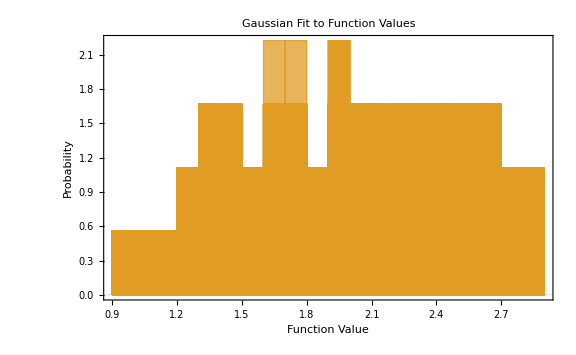
{FindDistributionParameters[(1.0792 | 1.61935 | 1.18889 | 1.26063 | 1.34562 | 1.76602 | 1.68416 | 1.76689 | 1.7099 | 2.09161 | 2.11477 | 2.19379 | 2.32462 | 2.30573 | 2.38365 | 2.51936 | 2.76655 | 2.86969
0.927593 | 1.53974 | 1.14691 | 1.35397 | 1.467 | 1.58363 | 1.76807 | 1.89163 | 1.79528 | 2.02476 | 2.23596 | 2.23131 | 2.29603 | 2.37874 | 2.33459 | 2.52238 | 2.70348 | 2.88571
0.974451 | 1.31493 | 1.12453 | 1.24269 | 1.39633 | 1.62139 | 1.7907 | 1.91717 | 2.06784 | 1.99657 | 2.20629 | 2.25679 | 2.21535 | 2.34393 | 2.56491 | 2.55666 | 2.88322 | 2.71698
1.05644 | 1.65153 | 1.16303 | 1.36037 | 1.30696 | 1.58992 | 1.7728 | 1.94265 | 2.02023 | 1.98208 | 1.98678 | 2.10302 | 2.28179 | 2.45553 | 2.50296 | 2.61355 | 2.50101 | 2.79216
1.05875 | 1.63234 | 1.13429 | 1.32089 | 1.32459 | 1.62645 | 1.67408 | 1.69766 | 1.86649 | 1.94737 | 2.14353 | 2.1091 | 2.29237 | 2.36567 | 2.63294 | 2.52459 | 2.62449 | 2.75536
0.992384 | 1.31051 | 1.11113 | 1.29071 | 1.31026 | 1.54609 | 1.63204 | 1.9524 | 1.80618 | 2.09321 | 2.03471 | 2.10094 | 2.42708 | 2.4255 | 2.56616 | 2.5047 | 2.89122 | 2.77932
1.01076 | 1.44382 | 1.27399 | 1.31045 | 1.36568 | 1.68894 | 1.7565 | 1.6547 | 1.93299 | 2.00385 | 2.01078 | 2.18377 | 2.4237 | 2.49853 | 2.44207 | 2.5969 | 2.66185 | 2.83178
1.0127 | 1.56096 | 1.29608 | 1.39995 | 1.33733 | 1.53102 | 1.72786 | 1.75972 | 2.09254 | 2.05766 | 2.05231 | 2.23352 | 2.2986 | 2.47994 | 2.65002 | 2.59324 | 2.80685 | 2.80806
1.01664 | 1.67733 | 1.22898 | 1.38948 | 1.43326 | 1.49376 | 1.77988 | 1.82814 | 1.97561 | 1.9834 | 2.25848 | 2.2303 | 2.22234 | 2.30018 | 2.48947 | 2.64693 | 2.81866 | 2.86892
0.981778 | 1.47242 | 1.22866 | 1.21313 | 1.40419 | 1.62404 | 1.61806 | 1.72008 | 1.76577 | 2.08919 | 2.06425 | 2.24331 | 2.10201 | 2.45681 | 2.48651 | 2.58049 | 2.65887 | 2.89481
1.08076 | 1.60123 | 1.2766 | 1.34125 | 1.3536 | 1.79341 | 1.70155 | 1.82582 | 1.71093 | 2.06862 | 2.20753 | 2.28945 | 2.14693 | 2.33955 | 2.46942 | 2.65149 | 2.6844 | 2.77938
0.922822 | 1.45459 | 1.11736 | 1.32125 | 1.35882 | 1.74006 | 1.79884 | 1.79797 | 2.03599 | 2.07471 | 1.93914 | 2.20799 | 2.30547 | 2.37426 | 2.37324 | 2.62941 | 2.84541 | 2.85341
0.990371 | 1.56099 | 1.15614 | 1.31596 | 1.33345 | 1.73348 | 1.78135 | 1.67753 | 1.8307 | 1.98468 | 2.10872 | 2.16486 | 2.37888 | 2.47474 | 2.65298 | 2.57453 | 2.89417 | 2.87783
0.970808 | 1.542 | 1.16572 | 1.33126 | 1.307 | 1.63095 | 1.64215 | 1.66605 | 1.92943 | 1.97219 | 1.93057 | 2.29519 | 2.27029 | 2.44798 | 2.62994 | 2.52903 | 2.70251 | 2.80397
0.952234 | 1.68093 | 1.25435 | 1.39915 | 1.46036 | 1.7399 | 1.7188 | 1.87956 | 1.71625 | 2.03103 | 2.22037 | 2.13951 | 2.2357 | 2.41779 | 2.47574 | 2.50087 | 2.67724 | 2.76454
0.940395 | 1.36371 | 1.16997 | 1.36665 | 1.46913 | 1.45193 | 1.74192 | 1.79954 | 1.87352 | 1.93757 | 2.23077 | 2.25394 | 2.16709 | 2.43058 | 2.60075 | 2.55153 | 2.55315 | 2.77059
0.956853 | 1.67882 | 1.14623 | 1.27891 | 1.4179 | 1.67191 | 1.71401 | 1.93906 | 1.99958 | 1.98117 | 2.25963 | 2.12381 | 2.10931 | 2.43114 | 2.36263 | 2.5212 | 2.82119 | 2.71357
0.999479 | 1.55668 | 1.16246 | 1.20044 | 1.34825 | 1.44185 | 1.73402 | 1.72654 | 1.85638 | 1.91084 | 2.16397 | 2.10314 | 2.11282 | 2.45482 | 2.4901 | 2.56503 | 2.86421 | 2.81622
0.984274 | 1.33287 | 1.25382 | 1.2693 | 1.32428 | 1.41982 | 1.74175 | 1.78864 | 1.72197 | 1.92402 | 1.918 | 2.24875 | 2.20135 | 2.34532 | 2.44832 | 2.58832 | 2.75806 | 2.85675
1.09509 | 1.54182 | 1.21293 | 1.37068 | 1.36246 | 1.58208 | 1.78624 | 1.9199 | 1.8877 | 1.9974 | 2.00848 | 2.11091 | 2.47402 | 2.38705 | 2.31229 | 2.62716 | 2.59256 | 2.7692
1.05636 | 1.54463 | 1.27584 | 1.27887 | 1.34535 | 1.43413 | 1.74393 | 1.68156 | 2.05414 | 2.05165 | 2.12574 | 2.22426 | 2.42947 | 2.44123 | 2.45344 | 2.60907 | 2.79485 | 2.75485
1.0649 | 1.43549 | 1.14554 | 1.34989 | 1.3654 | 1.50439 | 1.73792 | 1.90085 | 1.72237 | 2.09003 | 2.27987 | 2.2978 | 2.11878 | 2.38239 | 2.5643 | 2.557 | 2.56194 | 2.82485
0.919924 | 1.43046 | 1.23438 | 1.27994 | 1.37207 | 1.75875 | 1.62687 | 1.76273 | 2.06535 | 1.95751 | 2.1088 | 2.29749 | 2.19877 | 2.42425 | 2.53124 | 2.6077 | 2.73597 | 2.7005
1.06991 | 1.65775 | 1.1248 | 1.32392 | 1.49917 | 1.46972 | 1.76086 | 1.72558 | 1.98593 | 1.91888 | 1.9444 | 2.10802 | 2.16256 | 2.44946 | 2.47949 | 2.6536 | 2.65118 | 2.79418
1.06444 | 1.57845 | 1.12792 | 1.3413 | 1.41629 | 1.42374 | 1.7934 | 1.70519 | 2.05468 | 2.07014 | 1.98119 | 2.23456 | 2.31863 | 2.47759 | 2.33408 | 2.69752 | 2.71216 | 2.81563
0.966638 | 1.41326 | 1.18131 | 1.291 | 1.49825 | 1.57125 | 1.68407 | 1.98353 | 1.94198 | 1.92192 | 2.01866 | 2.15983 | 2.2968 | 2.33558 | 2.68773 | 2.52856 | 2.79404 | 2.72681
1.08492 | 1.45291 | 1.17064 | 1.26999 | 1.33785 | 1.65894 | 1.61229 | 1.81951 | 1.96586 | 1.99558 | 2.27926 | 2.15968 | 2.27971 | 2.49756 | 2.36431 | 2.69336 | 2.89517 | 2.78547
0.960361 | 1.39448 | 1.26376 | 1.26827 | 1.42204 | 1.70554 | 1.65336 | 1.94371 | 1.90332 | 1.93896 | 1.98782 | 2.22307 | 2.4821 | 2.39811 | 2.68696 | 2.53212 | 2.81405 | 2.7881
0.922397 | 1.57196 | 1.13053 | 1.32137 | 1.36257 | 1.64234 | 1.68961 | 1.97488 | 2.00749 | 1.92754 | 2.16292 | 2.10245 | 2.23733 | 2.3953 | 2.51965 | 2.50201 | 2.71034 | 2.71313
1.01351 | 1.44908 | 1.12733 | 1.28589 | 1.41971 | 1.79537 | 1.71996 | 1.88541 | 1.80562 | 2.09458 | 2.25078 | 2.29231 | 2.33724 | 2.45793 | 2.48226 | 2.54716 | 2.78167 | 2.72011
1.04386 | 1.54129 | 1.13766 | 1.2824 | 1.41105 | 1.67416 | 1.65023 | 1.98055 | 1.86067 | 1.9422 | 2.18844 | 2.10983 | 2.37799 | 2.35208 | 2.58691 | 2.52339 | 2.68931 | 2.78013
0.969538 | 1.6334 | 1.15194 | 1.22733 | 1.32083 | 1.76269 | 1.61659 | 1.90428 | 1.99723 | 1.92465 | 2.01177 | 2.10526 | 2.29993 | 2.31093 | 2.55736 | 2.53762 | 2.82096 | 2.71699
1.07952 | 1.42099 | 1.13806 | 1.21689 | 1.35442 | 1.72052 | 1.61579 | 1.77683 | 2.06566 | 1.99939 | 2.01314 | 2.22458 | 2.33797 | 2.4326 | 2.44798 | 2.58132 | 2.51444 | 2.88714
1.09552 | 1.46465 | 1.15994 | 1.29443 | 1.31628 | 1.4273 | 1.79045 | 1.68431 | 1.97782 | 1.945 | 2.11394 | 2.15528 | 2.22101 | 2.30168 | 2.56058 | 2.54555 | 2.57249 | 2.76193
1.06645 | 1.66852 | 1.17824 | 1.3647 | 1.3382 | 1.54842 | 1.63688 | 1.71453 | 1.96125 | 2.03385 | 2.26057 | 2.25379 | 2.31189 | 2.38808 | 2.53987 | 2.50846 | 2.59298 | 2.79827
1.00336 | 1.44041 | 1.24169 | 1.21158 | 1.40802 | 1.74545 | 1.68658 | 1.79604 | 1.81017 | 1.98261 | 2.14424 | 2.17136 | 2.36992 | 2.30213 | 2.64867 | 2.6976 | 2.81264 | 2.81439
0.954445 | 1.39642 | 1.28049 | 1.31569 | 1.39382 | 1.7196 | 1.64809 | 1.9324 | 1.8992 | 1.92379 | 2.2705 | 2.22007 | 2.26555 | 2.37852 | 2.35398 | 2.54831 | 2.60033 | 2.70058
1.03714 | 1.45972 | 1.21912 | 1.29053 | 1.36291 | 1.65746 | 1.65576 | 1.68672 | 1.807 | 1.94515 | 2.09964 | 2.20209 | 2.47039 | 2.43532 | 2.58279 | 2.54632 | 2.72004 | 2.76034
1.07161 | 1.37595 | 1.18432 | 1.38716 | 1.48468 | 1.75144 | 1.62757 | 1.63883 | 2.02037 | 1.95431 | 1.98788 | 2.16057 | 2.19309 | 2.30454 | 2.30792 | 2.50521 | 2.73713 | 2.89273
1.05837 | 1.34383 | 1.13689 | 1.21177 | 1.3304 | 1.66242 | 1.73196 | 1.69545 | 1.76306 | 1.96827 | 2.11516 | 2.1625 | 2.10026 | 2.49638 | 2.56888 | 2.66005 | 2.89131 | 2.86247
0.967433 | 1.60177 | 1.17715 | 1.29985 | 1.41376 | 1.69607 | 1.67277 | 1.95396 | 1.87814 | 2.08276 | 2.03117 | 2.10628 | 2.32686 | 2.44855 | 2.61192 | 2.63127 | 2.82497 | 2.86385
1.04503 | 1.5505 | 1.29145 | 1.33544 | 1.30386 | 1.40987 | 1.60586 | 1.92026 | 1.98494 | 1.98689 | 2.01596 | 2.12883 | 2.42532 | 2.3158 | 2.39746 | 2.66921 | 2.59158 | 2.81192
1.04542 | 1.47158 | 1.29752 | 1.31176 | 1.47167 | 1.66497 | 1.74703 | 1.88316 | 1.76822 | 1.97293 | 2.14472 | 2.23179 | 2.33017 | 2.42599 | 2.48357 | 2.56998 | 2.77379 | 2.81897
1.08209 | 1.60238 | 1.21836 | 1.33491 | 1.37439 | 1.69209 | 1.65769 | 1.75104 | 1.78629 | 2.0047 | 1.99736 | 2.22338 | 2.30924 | 2.46446 | 2.60296 | 2.63967 | 2.50465 | 2.72702
0.930152 | 1.40618 | 1.2638 | 1.20844 | 1.39816 | 1.61115 | 1.75971 | 1.77579 | 1.72884 | 2.0288 | 2.1165 | 2.12437 | 2.32321 | 2.35454 | 2.6063 | 2.58996 | 2.65196 | 2.74035
1.04691 | 1.3871 | 1.29516 | 1.30658 | 1.35455 | 1.42973 | 1.74307 | 1.93725 | 1.93182 | 1.91204 | 2.02052 | 2.13536 | 2.11479 | 2.4818 | 2.59815 | 2.57328 | 2.68219 | 2.81114
0.947055 | 1.57392 | 1.25924 | 1.37455 | 1.32618 | 1.56359 | 1.6742 | 1.7494 | 1.90143 | 2.06095 | 2.22645 | 2.20094 | 2.29356 | 2.37983 | 2.51668 | 2.55107 | 2.5609 | 2.73836
1.0437 | 1.40625 | 1.19879 | 1.30137 | 1.40413 | 1.56018 | 1.69733 | 1.73349 | 2.02774 | 2.04699 | 2.23228 | 2.11453 | 2.38623 | 2.45766 | 2.6573 | 2.67152 | 2.50685 | 2.74177
1.03148 | 1.6991 | 1.23202 | 1.37814 | 1.31895 | 1.47406 | 1.66911 | 1.75074 | 1.87272 | 2.02655 | 1.98265 | 2.2482 | 2.44347 | 2.3685 | 2.41718 | 2.59153 | 2.5377 | 2.71474
0.935506 | 1.53249 | 1.26257 | 1.39411 | 1.32267 | 1.53117 | 1.75021 | 1.83682 | 1.77554 | 2.09122 | 2.2825 | 2.23698 | 2.47552 | 2.43746 | 2.39422 | 2.69649 | 2.8077 | 2.74396
1.00854 | 1.67497 | 1.18452 | 1.26399 | 1.42435 | 1.59132 | 1.6853 | 1.60531 | 1.70931 | 1.96127 | 2.2022 | 2.22561 | 2.34847 | 2.30367 | 2.58785 | 2.58542 | 2.82908 | 2.7212
1.00186 | 1.59051 | 1.28838 | 1.24542 | 1.35315 | 1.74097 | 1.60835 | 1.76999 | 2.01394 | 2.0762 | 2.03436 | 2.23734 | 2.40942 | 2.48502 | 2.57272 | 2.64041 | 2.83224 | 2.80884
0.907893 | 1.53866 | 1.20228 | 1.33454 | 1.37806 | 1.60574 | 1.63916 | 1.73046 | 1.70139 | 2.03206 | 2.28679 | 2.25794 | 2.44442 | 2.42808 | 2.48555 | 2.63769 | 2.51246 | 2.77037
1.087 | 1.41544 | 1.14505 | 1.35713 | 1.33126 | 1.71925 | 1.63036 | 1.81267 | 1.8429 | 1.99287 | 2.09763 | 2.14632 | 2.28007 | 2.36337 | 2.33079 | 2.52867 | 2.7034 | 2.73113
0.94305 | 1.38888 | 1.20843 | 1.35017 | 1.34076 | 1.72331 | 1.71728 | 1.64022 | 1.70149 | 2.03841 | 2.21214 | 2.29556 | 2.22755 | 2.43825 | 2.49385 | 2.58982 | 2.6993 | 2.77748
1.07571 | 1.66102 | 1.14674 | 1.21384 | 1.30448 | 1.76878 | 1.70541 | 1.84169 | 1.88408 | 2.07636 | 2.19621 | 2.1422 | 2.32904 | 2.30083 | 2.32906 | 2.50528 | 2.52183 | 2.75633
0.926409 | 1.58055 | 1.15349 | 1.36057 | 1.37161 | 1.46669 | 1.74278 | 1.99255 | 1.92354 | 1.94644 | 1.9674 | 2.15058 | 2.267 | 2.30418 | 2.55587 | 2.61398 | 2.89043 | 2.86562
0.933776 | 1.57739 | 1.12654 | 1.24547 | 1.49905 | 1.6179 | 1.68939 | 1.72842 | 1.71009 | 2.04266 | 1.97154 | 2.11601 | 2.11109 | 2.3489 | 2.36024 | 2.64262 | 2.65146 | 2.87546
1.06765 | 1.52278 | 1.28495 | 1.34449 | 1.43536 | 1.58446 | 1.63564 | 1.72204 | 1.8264 | 2.04938 | 1.95377 | 2.21995 | 2.35728 | 2.36261 | 2.32276 | 2.58052 | 2.51352 | 2.79368
1.08738 | 1.607 | 1.16707 | 1.2412 | 1.48152 | 1.56751 | 1.78807 | 1.61374 | 1.89767 | 1.97189 | 2.06125 | 2.18186 | 2.12728 | 2.37282 | 2.38821 | 2.51129 | 2.88801 | 2.72847
0.936209 | 1.35141 | 1.17192 | 1.27225 | 1.32446 | 1.64763 | 1.76176 | 1.79302 | 1.75399 | 1.94762 | 2.27365 | 2.11495 | 2.49339 | 2.30713 | 2.55874 | 2.50732 | 2.58212 | 2.80926
1.08818 | 1.52653 | 1.12859 | 1.23572 | 1.47606 | 1.70853 | 1.68675 | 1.73878 | 2.05201 | 1.93416 | 1.93846 | 2.11376 | 2.37228 | 2.35955 | 2.66937 | 2.66695 | 2.86193 | 2.79182
1.09467 | 1.61975 | 1.12212 | 1.23061 | 1.4947 | 1.47718 | 1.67273 | 1.65129 | 1.8806 | 1.99293 | 2.17888 | 2.28935 | 2.29905 | 2.32687 | 2.40283 | 2.58799 | 2.54393 | 2.83538
0.941097 | 1.62823 | 1.16408 | 1.38117 | 1.49772 | 1.6724 | 1.66456 | 1.85514 | 2.08514 | 1.99548 | 2.25651 | 2.1251 | 2.16084 | 2.44924 | 2.58558 | 2.6708 | 2.58527 | 2.7795
1.09645 | 1.3947 | 1.24407 | 1.32958 | 1.44542 | 1.70087 | 1.63639 | 1.688 | 1.99134 | 2.04264 | 2.00214 | 2.14098 | 2.19917 | 2.36541 | 2.59074 | 2.59898 | 2.56512 | 2.85291
1.00648 | 1.38829 | 1.23386 | 1.39184 | 1.3439 | 1.51612 | 1.64948 | 1.61112 | 1.93473 | 2.07705 | 1.90951 | 2.2683 | 2.30991 | 2.49686 | 2.62353 | 2.68958 | 2.89184 | 2.7837
0.907835 | 1.43206 | 1.27864 | 1.2026 | 1.49237 | 1.74163 | 1.79498 | 1.75712 | 2.02761 | 2.02061 | 2.27398 | 2.22791 | 2.16139 | 2.39535 | 2.40846 | 2.5162 | 2.8984 | 2.73579
0.935657 | 1.33805 | 1.26922 | 1.38001 | 1.39032 | 1.72519 | 1.65361 | 1.62771 | 1.89062 | 1.92358 | 2.14471 | 2.17333 | 2.18269 | 2.39027 | 2.4942 | 2.6263 | 2.85567 | 2.86926
0.981198 | 1.65957 | 1.18959 | 1.31152 | 1.33312 | 1.46199 | 1.70604 | 1.66539 | 1.9659 | 2.01846 | 2.10464 | 2.1413 | 2.31981 | 2.40995 | 2.5537 | 2.59677 | 2.75302 | 2.86731
1.05356 | 1.36059 | 1.24024 | 1.34597 | 1.30999 | 1.549 | 1.6811 | 1.70363 | 1.90536 | 1.96361 | 2.02767 | 2.13482 | 2.34624 | 2.44626 | 2.44084 | 2.52869 | 2.87932 | 2.77069
1.05842 | 1.56528 | 1.24395 | 1.2343 | 1.48618 | 1.64541 | 1.7576 | 1.80799 | 2.00724 | 1.90354 | 2.26372 | 2.20283 | 2.11726 | 2.38903 | 2.63813 | 2.51584 | 2.72918 | 2.7599
0.939 | 1.48515 | 1.18871 | 1.35807 | 1.49955 | 1.49069 | 1.63243 | 1.75125 | 1.95519 | 1.92662 | 2.15269 | 2.13108 | 2.19964 | 2.48734 | 2.53269 | 2.54734 | 2.5906 | 2.85786
1.02099 | 1.3677 | 1.17846 | 1.38261 | 1.34528 | 1.68504 | 1.73587 | 1.67587 | 2.0779 | 2.07432 | 1.98705 | 2.10828 | 2.30875 | 2.36081 | 2.42976 | 2.67198 | 2.65183 | 2.87544
1.0284 | 1.45807 | 1.17661 | 1.24096 | 1.32096 | 1.55112 | 1.76841 | 1.78313 | 1.78973 | 2.0127 | 1.97651 | 2.18488 | 2.32583 | 2.44423 | 2.5863 | 2.59416 | 2.75085 | 2.73981
0.991394 | 1.64543 | 1.15152 | 1.21047 | 1.39022 | 1.44079 | 1.7352 | 1.81261 | 2.02916 | 2.07193 | 2.15398 | 2.24687 | 2.46456 | 2.49076 | 2.48054 | 2.50391 | 2.74094 | 2.73523
0.924527 | 1.66703 | 1.20628 | 1.30102 | 1.39426 | 1.53022 | 1.76214 | 1.64763 | 1.77015 | 2.08857 | 2.0669 | 2.10038 | 2.15701 | 2.45177 | 2.32458 | 2.65265 | 2.82028 | 2.74021
1.04817 | 1.33736 | 1.25362 | 1.35351 | 1.30833 | 1.43252 | 1.76712 | 1.72923 | 1.92367 | 1.99986 | 2.10779 | 2.11089 | 2.43553 | 2.44158 | 2.675 | 2.66644 | 2.66103 | 2.8137
0.983839 | 1.67142 | 1.1064 | 1.24207 | 1.38653 | 1.40356 | 1.62489 | 1.82044 | 1.81211 | 2.09386 | 2.08203 | 2.1606 | 2.37343 | 2.30467 | 2.39898 | 2.53701 | 2.73445 | 2.72616
0.926069 | 1.60056 | 1.25032 | 1.37677 | 1.39302 | 1.74188 | 1.66418 | 1.89135 | 1.98973 | 2.0647 | 2.29247 | 2.22155 | 2.45266 | 2.42221 | 2.3998 | 2.68287 | 2.85099 | 2.79407
1.08614 | 1.4885 | 1.2445 | 1.23775 | 1.35267 | 1.43627 | 1.60901 | 1.78372 | 1.97375 | 2.04153 | 1.96661 | 2.23123 | 2.2841 | 2.4055 | 2.48725 | 2.55566 | 2.51952 | 2.86976
0.972227 | 1.43621 | 1.19614 | 1.24109 | 1.45178 | 1.46244 | 1.74947 | 1.87033 | 1.97482 | 1.9333 | 1.92585 | 2.18113 | 2.25588 | 2.47398 | 2.57627 | 2.61908 | 2.73629 | 2.89627
0.960714 | 1.39753 | 1.23483 | 1.25958 | 1.40293 | 1.67334 | 1.61808 | 1.76314 | 1.78968 | 1.94817 | 2.18872 | 2.22883 | 2.4639 | 2.38975 | 2.58054 | 2.51397 | 2.82314 | 2.81578
0.971471 | 1.4812 | 1.19583 | 1.24668 | 1.39398 | 1.43673 | 1.79234 | 1.91078 | 1.85804 | 2.06914 | 2.03264 | 2.22209 | 2.49756 | 2.3075 | 2.38516 | 2.51058 | 2.87498 | 2.72955
0.960346 | 1.32049 | 1.1878 | 1.35509 | 1.32763 | 1.52004 | 1.62631 | 1.94586 | 2.01361 | 2.01465 | 2.23348 | 2.29726 | 2.10991 | 2.3613 | 2.6751 | 2.5742 | 2.82504 | 2.86169
0.904938 | 1.36137 | 1.20915 | 1.2927 | 1.32494 | 1.48451 | 1.76506 | 1.90703 | 1.74422 | 2.02337 | 1.98324 | 2.10079 | 2.49337 | 2.44786 | 2.50918 | 2.59434 | 2.89267 | 2.74172
0.97203 | 1.40636 | 1.20528 | 1.38775 | 1.3606 | 1.5888 | 1.74567 | 1.8991 | 1.7452 | 2.02752 | 2.05561 | 2.29569 | 2.12507 | 2.45925 | 2.58396 | 2.51899 | 2.60043 | 2.86504
1.09833 | 1.33176 | 1.21561 | 1.37466 | 1.46659 | 1.73829 | 1.72741 | 1.8163 | 2.04965 | 1.92044 | 2.14663 | 2.19564 | 2.13645 | 2.38606 | 2.55636 | 2.53968 | 2.64311 | 2.8186
1.07349 | 1.36634 | 1.20313 | 1.3094 | 1.37379 | 1.49183 | 1.66861 | 1.84563 | 1.77138 | 1.94124 | 2.11529 | 2.14106 | 2.37511 | 2.43801 | 2.6598 | 2.53605 | 2.68568 | 2.84378
0.908647 | 1.44244 | 1.10912 | 1.2538 | 1.33826 | 1.53732 | 1.78072 | 1.71013 | 1.94284 | 1.93123 | 2.03643 | 2.18207 | 2.34382 | 2.33868 | 2.60735 | 2.61696 | 2.76268 | 2.75705
0.969696 | 1.41113 | 1.28204 | 1.23335 | 1.47299 | 1.42006 | 1.60543 | 1.99775 | 1.90971 | 1.94406 | 2.10293 | 2.25816 | 2.19456 | 2.44485 | 2.67182 | 2.54451 | 2.52307 | 2.87608
1.03776 | 1.43176 | 1.26388 | 1.32838 | 1.30684 | 1.52389 | 1.77977 | 1.62 | 1.70715 | 2.02384 | 2.13059 | 2.24274 | 2.23694 | 2.48225 | 2.32331 | 2.5416 | 2.71431 | 2.83146
0.981225 | 1.65635 | 1.24847 | 1.26296 | 1.40646 | 1.79363 | 1.75464 | 1.85435 | 1.73967 | 2.05713 | 2.15482 | 2.13937 | 2.41625 | 2.42792 | 2.38953 | 2.6929 | 2.67026 | 2.71742
1.07935 | 1.50891 | 1.14671 | 1.39193 | 1.43689 | 1.60316 | 1.63706 | 1.88916 | 1.79589 | 1.91382 | 2.12631 | 2.20353 | 2.27067 | 2.44087 | 2.59837 | 2.62058 | 2.78916 | 2.84273
0.930174 | 1.33583 | 1.13361 | 1.25389 | 1.35727 | 1.57917 | 1.77343 | 1.8517 | 2.05798 | 2.03102 | 2.23025 | 2.11717 | 2.13957 | 2.35645 | 2.43594 | 2.64246 | 2.80062 | 2.83548
0.918215 | 1.68568 | 1.25058 | 1.31473 | 1.32684 | 1.40478 | 1.67667 | 1.61861 | 1.78474 | 2.01357 | 2.29507 | 2.13391 | 2.25475 | 2.39739 | 2.37567 | 2.55834 | 2.69906 | 2.80204
1.0473 | 1.53292 | 1.20694 | 1.2054 | 1.36971 | 1.77366 | 1.62887 | 1.72785 | 1.8021 | 2.0758 | 1.95375 | 2.22393 | 2.28999 | 2.38326 | 2.39457 | 2.60825 | 2.87892 | 2.72877
1.09605 | 1.5188 | 1.20176 | 1.27012 | 1.36413 | 1.60718 | 1.63761 | 1.89946 | 2.08131 | 2.08669 | 2.08609 | 2.1618 | 2.44794 | 2.33637 | 2.39623 | 2.60224 | 2.5152 | 2.71108
0.901799 | 1.37954 | 1.22564 | 1.22486 | 1.38904 | 1.42969 | 1.6763 | 1.82397 | 2.0138 | 1.90908 | 2.27667 | 2.25543 | 2.36944 | 2.4595 | 2.52114 | 2.61365 | 2.63766 | 2.73673
1.00791 | 1.62213 | 1.17765 | 1.35623 | 1.34362 | 1.44377 | 1.76321 | 1.70794 | 1.88227 | 2.01533 | 1.92315 | 2.17307 | 2.445 | 2.40944 | 2.69738 | 2.55577 | 2.89099 | 2.77901
0.923596 | 1.63669 | 1.23626 | 1.31657 | 1.38754 | 1.62183 | 1.78074 | 1.68513 | 2.06415 | 2.00957 | 2.10396 | 2.24378 | 2.4668 | 2.49539 | 2.57397 | 2.57611 | 2.83981 | 2.79272
0.900886 | 1.35125 | 1.26171 | 1.27713 | 1.40572 | 1.51911 | 1.75971 | 1.95347 | 2.06376 | 1.95253 | 2.09466 | 2.23816 | 2.45929 | 2.47336 | 2.65612 | 2.5122 | 2.853 | 2.73574
1.02499 | 1.67032 | 1.18554 | 1.20402 | 1.45217 | 1.78315 | 1.73794 | 1.60326 | 1.79404 | 1.95519 | 2.19126 | 2.20639 | 2.28213 | 2.44986 | 2.41669 | 2.59269 | 2.61552 | 2.89669
1.01247 | 1.68847 | 1.15503 | 1.31996 | 1.43228 | 1.4075 | 1.63001 | 1.86248 | 1.76141 | 1.90141 | 2.01845 | 2.13124 | 2.13894 | 2.35407 | 2.62669 | 2.686 | 2.57107 | 2.70625
1.09048 | 1.56758 | 1.21364 | 1.29957 | 1.45306 | 1.48316 | 1.69438 | 1.66052 | 1.89326 | 1.94889 | 2.03953 | 2.19219 | 2.11004 | 2.33351 | 2.44794 | 2.55907 | 2.61062 | 2.84969
1.06802 | 1.59815 | 1.15775 | 1.372 | 1.40579 | 1.61863 | 1.70609 | 1.91775 | 1.89682 | 2.03372 | 2.13035 | 2.2696 | 2.28237 | 2.48584 | 2.48676 | 2.56995 | 2.62111 | 2.73731
0.956298 | 1.65206 | 1.19905 | 1.21276 | 1.34951 | 1.55939 | 1.65583 | 1.88125 | 1.78899 | 2.0614 | 2.18989 | 2.11853 | 2.20845 | 2.43991 | 2.60582 | 2.65327 | 2.51066 | 2.8806
0.974488 | 1.66905 | 1.23498 | 1.29893 | 1.38475 | 1.49006 | 1.60221 | 1.8334 | 1.85311 | 2.02788 | 2.24252 | 2.13773 | 2.17194 | 2.36628 | 2.63736 | 2.56757 | 2.59001 | 2.80026
0.971392 | 1.38945 | 1.13795 | 1.35123 | 1.44268 | 1.76256 | 1.62496 | 1.744 | 1.79173 | 1.96741 | 2.14505 | 2.10857 | 2.46813 | 2.3984 | 2.53918 | 2.61022 | 2.87445 | 2.77498
1.05477 | 1.58569 | 1.18375 | 1.36056 | 1.47621 | 1.52298 | 1.66532 | 1.93807 | 1.99197 | 2.09603 | 2.07069 | 2.18629 | 2.222 | 2.46251 | 2.58768 | 2.64487 | 2.89183 | 2.742
0.956398 | 1.57489 | 1.23922 | 1.39327 | 1.32168 | 1.74961 | 1.74406 | 1.83238 | 1.77234 | 1.91412 | 2.05619 | 2.24485 | 2.28693 | 2.45563 | 2.33847 | 2.65991 | 2.78715 | 2.86373
0.958425 | 1.56867 | 1.25272 | 1.2137 | 1.38129 | 1.69981 | 1.70696 | 1.94579 | 1.77235 | 2.0454 | 2.26949 | 2.20868 | 2.33164 | 2.39011 | 2.43134 | 2.67005 | 2.53873 | 2.82785
0.954367 | 1.58478 | 1.12227 | 1.35827 | 1.35323 | 1.47781 | 1.64461 | 1.82044 | 1.90951 | 2.02576 | 2.09247 | 2.27585 | 2.24751 | 2.48953 | 2.50729 | 2.54377 | 2.57172 | 2.78408
0.968747 | 1.46808 | 1.2142 | 1.2636 | 1.48289 | 1.56213 | 1.70335 | 1.83594 | 2.06559 | 2.09725 | 1.9333 | 2.1735 | 2.48059 | 2.42174 | 2.30846 | 2.5395 | 2.7422 | 2.87978
1.05572 | 1.48626 | 1.17953 | 1.36965 | 1.35895 | 1.77305 | 1.69047 | 1.71995 | 1.97407 | 1.99069 | 2.04812 | 2.18912 | 2.49743 | 2.3525 | 2.33917 | 2.64114 | 2.89376 | 2.8469
0.972174 | 1.4824 | 1.23765 | 1.21178 | 1.39377 | 1.49101 | 1.71015 | 1.67205 | 1.9011 | 1.94198 | 2.01038 | 2.10883 | 2.44403 | 2.45186 | 2.43657 | 2.67536 | 2.52065 | 2.70788
1.04793 | 1.59727 | 1.21416 | 1.33931 | 1.49625 | 1.79044 | 1.6416 | 1.73594 | 2.05679 | 2.04727 | 2.13023 | 2.22659 | 2.39886 | 2.37699 | 2.30551 | 2.63195 | 2.56291 | 2.71467
0.942 | 1.61006 | 1.14716 | 1.36352 | 1.37512 | 1.71519 | 1.76591 | 1.82583 | 1.97634 | 2.00586 | 2.20654 | 2.29551 | 2.3139 | 2.38334 | 2.40671 | 2.56226 | 2.72851 | 2.81418
1.06951 | 1.55845 | 1.1214 | 1.3897 | 1.49926 | 1.52734 | 1.79308 | 1.9258 | 1.94161 | 1.95798 | 1.95277 | 2.25956 | 2.16076 | 2.43003 | 2.52046 | 2.63942 | 2.68568 | 2.89637
0.985418 | 1.30775 | 1.26584 | 1.28703 | 1.3438 | 1.75149 | 1.72931 | 1.9781 | 1.81348 | 1.97021 | 2.15037 | 2.29206 | 2.49977 | 2.46474 | 2.47106 | 2.50438 | 2.53114 | 2.88097
0.920494 | 1.32218 | 1.20033 | 1.21098 | 1.30517 | 1.4202 | 1.68607 | 1.7757 | 1.84657 | 2.08858 | 2.23738 | 2.15402 | 2.329 | 2.34289 | 2.49988 | 2.5339 | 2.69053 | 2.88277
0.92377 | 1.69675 | 1.10757 | 1.28593 | 1.4919 | 1.52482 | 1.68553 | 1.8767 | 1.83744 | 1.94562 | 2.02881 | 2.10199 | 2.45847 | 2.40789 | 2.37676 | 2.56172 | 2.71324 | 2.84633
0.991432 | 1.46825 | 1.22197 | 1.3012 | 1.35825 | 1.40842 | 1.74061 | 1.90745 | 1.99606 | 2.0885 | 2.24934 | 2.17711 | 2.11116 | 2.38497 | 2.66505 | 2.67551 | 2.81587 | 2.86339
0.982217 | 1.36674 | 1.1513 | 1.30035 | 1.3992 | 1.76917 | 1.641 | 1.62554 | 1.96396 | 1.9622 | 2.03373 | 2.13262 | 2.37242 | 2.3662 | 2.69388 | 2.53948 | 2.52326 | 2.72051
1.06586 | 1.5439 | 1.11198 | 1.24378 | 1.33712 | 1.62687 | 1.6056 | 1.85379 | 1.82641 | 2.05511 | 2.28678 | 2.22513 | 2.16147 | 2.3943 | 2.65551 | 2.50872 | 2.50933 | 2.78984
1.01331 | 1.45123 | 1.26437 | 1.31429 | 1.31878 | 1.46415 | 1.77473 | 1.99394 | 2.08695 | 1.90206 | 2.13276 | 2.20664 | 2.13584 | 2.48876 | 2.54088 | 2.66531 | 2.87239 | 2.78067
0.950224 | 1.56714 | 1.1759 | 1.27544 | 1.48965 | 1.52112 | 1.76822 | 1.61195 | 2.01529 | 1.96712 | 2.01286 | 2.13724 | 2.49026 | 2.37105 | 2.638 | 2.69548 | 2.60431 | 2.76934
0.954026 | 1.68391 | 1.18737 | 1.28369 | 1.37664 | 1.56066 | 1.70742 | 1.71557 | 2.04175 | 1.9562 | 2.27892 | 2.28315 | 2.13303 | 2.34004 | 2.54688 | 2.64973 | 2.88992 | 2.76761
1.02498 | 1.54351 | 1.16641 | 1.30151 | 1.40919 | 1.5052 | 1.72917 | 1.96323 | 1.81562 | 1.9398 | 2.11608 | 2.16841 | 2.46443 | 2.35242 | 2.37963 | 2.53477 | 2.53229 | 2.84258
1.05919 | 1.351 | 1.26628 | 1.24998 | 1.33066 | 1.6873 | 1.71973 | 1.80903 | 1.73928 | 1.95882 | 2.28568 | 2.12291 | 2.43319 | 2.41142 | 2.4531 | 2.53198 | 2.59219 | 2.70429
1.09015 | 1.59053 | 1.234 | 1.23934 | 1.41978 | 1.45751 | 1.74561 | 1.66872 | 1.75041 | 1.90635 | 1.91549 | 2.10029 | 2.26647 | 2.30412 | 2.48426 | 2.54955 | 2.86447 | 2.74241
1.03449 | 1.49798 | 1.21263 | 1.28652 | 1.33854 | 1.40698 | 1.75564 | 1.70392 | 1.86377 | 1.95716 | 2.11676 | 2.25223 | 2.27533 | 2.39654 | 2.43493 | 2.543 | 2.57728 | 2.8647
1.09567 | 1.53061 | 1.15171 | 1.35176 | 1.37184 | 1.70344 | 1.6758 | 1.942 | 1.83755 | 1.93031 | 2.07426 | 2.28363 | 2.44065 | 2.35472 | 2.63371 | 2.66949 | 2.50967 | 2.89414
1.04383 | 1.49296 | 1.15214 | 1.32907 | 1.32044 | 1.48868 | 1.67847 | 1.75433 | 1.90064 | 2.00788 | 2.10814 | 2.20807 | 2.35442 | 2.3507 | 2.3102 | 2.59268 | 2.75531 | 2.84951
0.970623 | 1.56263 | 1.23441 | 1.24851 | 1.48773 | 1.68767 | 1.72275 | 1.78174 | 1.99831 | 1.97336 | 2.20774 | 2.28044 | 2.4414 | 2.30767 | 2.55408 | 2.54521 | 2.87074 | 2.74878
1.0351 | 1.31014 | 1.22524 | 1.21428 | 1.49165 | 1.63442 | 1.7566 | 1.66345 | 1.77984 | 1.98483 | 1.93017 | 2.14472 | 2.25585 | 2.42699 | 2.57842 | 2.59833 | 2.82912 | 2.78711
1.01509 | 1.55378 | 1.12354 | 1.35015 | 1.3494 | 1.75657 | 1.60053 | 1.77691 | 2.0321 | 1.99438 | 2.00985 | 2.25616 | 2.18649 | 2.47721 | 2.55542 | 2.58006 | 2.89233 | 2.75917
0.915236 | 1.5196 | 1.10776 | 1.28609 | 1.30193 | 1.59154 | 1.63959 | 1.74 | 1.73621 | 1.93015 | 2.23782 | 2.16433 | 2.2514 | 2.32422 | 2.66294 | 2.57828 | 2.52948 | 2.80973
1.04584 | 1.69903 | 1.22721 | 1.27367 | 1.37779 | 1.78157 | 1.72193 | 1.86296 | 1.81896 | 2.04103 | 2.23508 | 2.19074 | 2.13011 | 2.3521 | 2.62252 | 2.53487 | 2.5737 | 2.79366
0.938779 | 1.57039 | 1.13234 | 1.33446 | 1.49429 | 1.72989 | 1.72307 | 1.69755 | 1.79796 | 2.08918 | 1.96569 | 2.25356 | 2.34064 | 2.44835 | 2.34658 | 2.67486 | 2.53542 | 2.848
1.08678 | 1.40997 | 1.16689 | 1.39247 | 1.31958 | 1.73368 | 1.63945 | 1.67204 | 1.81639 | 1.92743 | 1.90674 | 2.29596 | 2.42252 | 2.35105 | 2.68393 | 2.51565 | 2.51646 | 2.76711
1.0774 | 1.42148 | 1.24129 | 1.21429 | 1.31536 | 1.57693 | 1.79474 | 1.75843 | 1.72749 | 2.01713 | 2.08739 | 2.28274 | 2.21844 | 2.39131 | 2.62483 | 2.69855 | 2.89724 | 2.88481
0.996977 | 1.32803 | 1.11146 | 1.27528 | 1.47043 | 1.56317 | 1.70475 | 1.87586 | 1.9722 | 2.09536 | 2.2908 | 2.29786 | 2.33695 | 2.49759 | 2.33501 | 2.60093 | 2.74751 | 2.77967
1.08688 | 1.54481 | 1.24966 | 1.2726 | 1.30524 | 1.73161 | 1.73077 | 1.7431 | 1.97653 | 1.93938 | 2.20978 | 2.16068 | 2.12529 | 2.33183 | 2.66442 | 2.62603 | 2.78963 | 2.70119
0.920672 | 1.37399 | 1.18582 | 1.35424 | 1.38586 | 1.56325 | 1.7367 | 1.60221 | 2.0958 | 2.07522 | 2.06406 | 2.14396 | 2.28114 | 2.38714 | 2.45013 | 2.51903 | 2.85485 | 2.89475
0.930718 | 1.36602 | 1.18883 | 1.34645 | 1.35355 | 1.68318 | 1.68478 | 1.64232 | 2.08163 | 1.99904 | 2.24553 | 2.10822 | 2.26153 | 2.41263 | 2.62096 | 2.64191 | 2.79336 | 2.73317
1.08218 | 1.68187 | 1.24315 | 1.2018 | 1.47148 | 1.64934 | 1.63787 | 1.98218 | 1.89277 | 1.93203 | 2.14348 | 2.22595 | 2.23585 | 2.4251 | 2.35824 | 2.61147 | 2.7151 | 2.72572
1.04422 | 1.59883 | 1.1124 | 1.26158 | 1.48055 | 1.516 | 1.62371 | 1.72663 | 1.79547 | 1.9316 | 2.04393 | 2.23656 | 2.39679 | 2.31503 | 2.55364 | 2.58438 | 2.62344 | 2.73445
0.941578 | 1.6536 | 1.26928 | 1.32059 | 1.47803 | 1.59508 | 1.75663 | 1.8687 | 1.96131 | 1.91288 | 1.97953 | 2.10637 | 2.30911 | 2.34422 | 2.61791 | 2.57179 | 2.76253 | 2.87998
1.03819 | 1.45632 | 1.17787 | 1.34243 | 1.49041 | 1.45168 | 1.79509 | 1.73614 | 1.95478 | 2.06059 | 1.99261 | 2.12991 | 2.25046 | 2.32985 | 2.36366 | 2.5726 | 2.76984 | 2.82253
0.961906 | 1.56921 | 1.22473 | 1.23789 | 1.48568 | 1.78346 | 1.73449 | 1.75389 | 1.76165 | 2.09283 | 2.00773 | 2.1312 | 2.49485 | 2.44852 | 2.65948 | 2.53891 | 2.8045 | 2.76804
1.06358 | 1.55881 | 1.23523 | 1.30289 | 1.46195 | 1.43891 | 1.61118 | 1.86558 | 1.87709 | 2.03905 | 1.91316 | 2.18776 | 2.32018 | 2.38487 | 2.48601 | 2.52333 | 2.52768 | 2.74418
1.0222 | 1.52833 | 1.29674 | 1.24985 | 1.31057 | 1.53405 | 1.76179 | 1.63311 | 2.09695 | 2.02881 | 1.95437 | 2.20849 | 2.12935 | 2.48984 | 2.40116 | 2.55467 | 2.67922 | 2.83717
0.921118 | 1.42515 | 1.26004 | 1.27433 | 1.30112 | 1.41968 | 1.73549 | 1.86323 | 1.93282 | 1.95789 | 2.28834 | 2.10517 | 2.4053 | 2.37832 | 2.41404 | 2.56692 | 2.63156 | 2.88137
1.09137 | 1.42975 | 1.22047 | 1.20308 | 1.42021 | 1.68669 | 1.76488 | 1.75328 | 1.86039 | 2.054 | 2.18074 | 2.15895 | 2.23636 | 2.48352 | 2.47722 | 2.52767 | 2.55333 | 2.81979
1.00074 | 1.65688 | 1.11705 | 1.29865 | 1.34378 | 1.79226 | 1.71541 | 1.94912 | 1.70696 | 2.06261 | 1.98324 | 2.13074 | 2.17903 | 2.46943 | 2.42685 | 2.53649 | 2.69048 | 2.76397
0.908069 | 1.40548 | 1.15594 | 1.36881 | 1.32423 | 1.54754 | 1.6098 | 1.70394 | 2.05457 | 1.98294 | 2.25337 | 2.16504 | 2.25008 | 2.30274 | 2.65713 | 2.52984 | 2.83371 | 2.71559
0.905842 | 1.32488 | 1.26239 | 1.34238 | 1.49618 | 1.72533 | 1.61494 | 1.61779 | 2.0819 | 2.03087 | 2.08678 | 2.11811 | 2.4273 | 2.49682 | 2.65565 | 2.50263 | 2.72994 | 2.83192
0.974776 | 1.49082 | 1.21235 | 1.33129 | 1.41691 | 1.50632 | 1.63399 | 1.62368 | 1.89596 | 1.93622 | 2.19308 | 2.23142 | 2.38714 | 2.42632 | 2.4035 | 2.61689 | 2.7526 | 2.86568
0.94013 | 1.52387 | 1.18756 | 1.37798 | 1.32738 | 1.79629 | 1.69714 | 1.90918 | 1.89005 | 1.95061 | 1.94073 | 2.26396 | 2.21578 | 2.49366 | 2.66462 | 2.67443 | 2.52847 | 2.79056
0.910311 | 1.39823 | 1.20481 | 1.2424 | 1.31641 | 1.55581 | 1.73144 | 1.80929 | 2.05497 | 2.09287 | 1.98576 | 2.26945 | 2.2455 | 2.47806 | 2.69711 | 2.53018 | 2.82402 | 2.75901
1.04131 | 1.34701 | 1.21531 | 1.30996 | 1.3022 | 1.45353 | 1.69751 | 1.97136 | 1.94154 | 1.98006 | 2.23491 | 2.26235 | 2.19659 | 2.3595 | 2.64287 | 2.69153 | 2.76904 | 2.75207
1.09341 | 1.53499 | 1.2891 | 1.27663 | 1.35224 | 1.69886 | 1.67581 | 1.79734 | 1.97488 | 1.95265 | 2.17832 | 2.18391 | 2.14044 | 2.45036 | 2.68152 | 2.69299 | 2.89727 | 2.7128
0.966383 | 1.46812 | 1.24543 | 1.31134 | 1.48234 | 1.59356 | 1.72411 | 1.62815 | 1.74138 | 1.95812 | 2.22801 | 2.26833 | 2.1737 | 2.40755 | 2.40425 | 2.50535 | 2.56071 | 2.78535
0.939712 | 1.64082 | 1.13636 | 1.24535 | 1.41097 | 1.53271 | 1.71084 | 1.96548 | 1.85194 | 2.02048 | 1.9279 | 2.203 | 2.11621 | 2.39238 | 2.66895 | 2.50936 | 2.73822 | 2.75686
0.935844 | 1.52626 | 1.14536 | 1.3304 | 1.40173 | 1.73088 | 1.65821 | 1.9578 | 2.03696 | 1.98429 | 2.18987 | 2.28028 | 2.28951 | 2.37604 | 2.45076 | 2.61717 | 2.56677 | 2.73661
1.02542 | 1.33822 | 1.1745 | 1.33209 | 1.33322 | 1.78946 | 1.76308 | 1.81907 | 1.74234 | 2.09451 | 2.06786 | 2.28701 | 2.48175 | 2.42397 | 2.63516 | 2.63317 | 2.51536 | 2.71065
0.988708 | 1.64087 | 1.13426 | 1.22088 | 1.42935 | 1.59524 | 1.62398 | 1.6206 | 1.80336 | 1.91297 | 2.16886 | 2.25056 | 2.31953 | 2.40313 | 2.41983 | 2.53661 | 2.57688 | 2.83396
0.922022 | 1.57867 | 1.24806 | 1.24654 | 1.37868 | 1.45185 | 1.61939 | 1.73665 | 1.73756 | 2.07811 | 1.93259 | 2.21402 | 2.40829 | 2.4641 | 2.37516 | 2.63488 | 2.62702 | 2.88864
1.02765 | 1.51059 | 1.23448 | 1.38074 | 1.498 | 1.64617 | 1.65022 | 1.8848 | 2.09789 | 1.9237 | 1.9694 | 2.17133 | 2.37633 | 2.37232 | 2.6221 | 2.69972 | 2.73654 | 2.71266
1.07006 | 1.55029 | 1.184 | 1.36023 | 1.42858 | 1.49049 | 1.70653 | 1.72355 | 1.81788 | 2.0545 | 2.21816 | 2.17043 | 2.27638 | 2.49588 | 2.54428 | 2.55348 | 2.66176 | 2.73049
0.977884 | 1.52702 | 1.22058 | 1.34042 | 1.45403 | 1.55045 | 1.77982 | 1.87421 | 1.90109 | 1.95573 | 2.24473 | 2.11758 | 2.47084 | 2.44217 | 2.60063 | 2.54417 | 2.7566 | 2.81826
0.902675 | 1.30412 | 1.23693 | 1.36402 | 1.33347 | 1.58159 | 1.7941 | 1.71311 | 2.02075 | 1.99973 | 2.05524 | 2.17847 | 2.19289 | 2.43531 | 2.56564 | 2.69238 | 2.70589 | 2.89256
0.99289 | 1.49079 | 1.2831 | 1.39437 | 1.38717 | 1.67165 | 1.77264 | 1.94191 | 2.01186 | 2.0686 | 2.04119 | 2.286 | 2.26072 | 2.32704 | 2.6914 | 2.62259 | 2.59356 | 2.71595
0.98238 | 1.35221 | 1.25253 | 1.35672 | 1.44591 | 1.75202 | 1.609 | 1.68504 | 2.04676 | 1.93949 | 2.04093 | 2.14252 | 2.15254 | 2.31682 | 2.3563 | 2.53675 | 2.8398 | 2.78966
0.916665 | 1.39891 | 1.19244 | 1.37743 | 1.49937 | 1.54166 | 1.64588 | 1.89947 | 2.04326 | 2.02925 | 2.14616 | 2.21806 | 2.31419 | 2.40908 | 2.68084 | 2.52085 | 2.56114 | 2.85622
1.0925 | 1.682 | 1.24286 | 1.25501 | 1.37849 | 1.58032 | 1.67241 | 1.91838 | 1.9005 | 1.91733 | 1.94401 | 2.25227 | 2.49187 | 2.39151 | 2.35363 | 2.51 | 2.63125 | 2.85391
0.976633 | 1.46044 | 1.12909 | 1.39481 | 1.33327 | 1.42465 | 1.60861 | 1.79244 | 1.78297 | 2.05677 | 1.9703 | 2.28711 | 2.26152 | 2.4803 | 2.34289 | 2.64739 | 2.63227 | 2.71848
0.918284 | 1.68535 | 1.12423 | 1.34452 | 1.45342 | 1.42461 | 1.66895 | 1.92432 | 2.09191 | 2.04046 | 2.1835 | 2.15181 | 2.48904 | 2.48372 | 2.56724 | 2.51316 | 2.71923 | 2.7876
1.03135 | 1.5326 | 1.15858 | 1.30036 | 1.3484 | 1.54015 | 1.6862 | 1.69281 | 1.90611 | 2.09351 | 2.10847 | 2.2472 | 2.20607 | 2.3195 | 2.59602 | 2.59328 | 2.65651 | 2.86425
1.06982 | 1.41452 | 1.23179 | 1.28696 | 1.48131 | 1.50328 | 1.7445 | 1.86383 | 1.89772 | 2.02952 | 1.96815 | 2.23733 | 2.13928 | 2.35198 | 2.56087 | 2.65556 | 2.67644 | 2.7657
1.04933 | 1.66952 | 1.11556 | 1.31504 | 1.31605 | 1.7508 | 1.76179 | 1.62512 | 1.91813 | 1.90293 | 2.26037 | 2.11901 | 2.45349 | 2.4278 | 2.61518 | 2.53026 | 2.85171 | 2.77315
0.985812 | 1.62199 | 1.15259 | 1.37277 | 1.39643 | 1.64809 | 1.75279 | 1.88644 | 1.7527 | 1.9495 | 2.27409 | 2.10209 | 2.21632 | 2.46098 | 2.40836 | 2.55647 | 2.56276 | 2.74875
1.07232 | 1.56549 | 1.13251 | 1.37326 | 1.36215 | 1.59068 | 1.66394 | 1.93335 | 1.8043 | 1.91249 | 1.93092 | 2.22999 | 2.36124 | 2.44229 | 2.46299 | 2.54476 | 2.75458 | 2.7721
0.923948 | 1.57584 | 1.13407 | 1.3053 | 1.46109 | 1.64665 | 1.67452 | 1.68248 | 1.87813 | 1.97985 | 2.05417 | 2.11275 | 2.37488 | 2.49917 | 2.34678 | 2.56782 | 2.70533 | 2.88717
0.953503 | 1.426 | 1.15365 | 1.21955 | 1.34184 | 1.6669 | 1.72391 | 1.79932 | 1.84802 | 2.09686 | 2.2607 | 2.28462 | 2.40325 | 2.36827 | 2.55042 | 2.51537 | 2.79873 | 2.82943
0.95891 | 1.6472 | 1.25932 | 1.24314 | 1.36251 | 1.48238 | 1.67754 | 1.92803 | 1.83354 | 2.05235 | 2.01711 | 2.1314 | 2.20254 | 2.44556 | 2.69846 | 2.55025 | 2.85755 | 2.7666
1.0891 | 1.39598 | 1.27325 | 1.2072 | 1.41657 | 1.6536 | 1.7025 | 1.60123 | 1.82697 | 2.02537 | 2.05268 | 2.26446 | 2.48884 | 2.31982 | 2.54465 | 2.64804 | 2.6699 | 2.82128
0.979275 | 1.62033 | 1.11538 | 1.24461 | 1.30545 | 1.71473 | 1.68502 | 1.79983 | 2.07028 | 2.00931 | 2.14794 | 2.21375 | 2.31035 | 2.42678 | 2.33242 | 2.55853 | 2.63661 | 2.72405
1.0616 | 1.60575 | 1.28411 | 1.3541 | 1.36672 | 1.45088 | 1.62819 | 1.78478 | 1.96164 | 2.06772 | 1.97652 | 2.23567 | 2.3047 | 2.43393 | 2.69096 | 2.69188 | 2.71731 | 2.70798
0.904059 | 1.57736 | 1.1979 | 1.33606 | 1.41486 | 1.54987 | 1.65152 | 1.95938 | 2.0108 | 2.07606 | 2.12973 | 2.2572 | 2.40044 | 2.47868 | 2.5461 | 2.69014 | 2.55698 | 2.74124
0.982375 | 1.64209 | 1.17116 | 1.38401 | 1.42727 | 1.78051 | 1.78612 | 1.70737 | 1.97667 | 1.97406 | 1.9542 | 2.1773 | 2.21087 | 2.36967 | 2.52748 | 2.54179 | 2.5013 | 2.70556
0.905255 | 1.49965 | 1.187 | 1.26037 | 1.33537 | 1.47245 | 1.65329 | 1.63394 | 2.02983 | 2.02472 | 2.27077 | 2.11441 | 2.49513 | 2.41525 | 2.34954 | 2.66649 | 2.75685 | 2.82651
0.99119 | 1.32212 | 1.20248 | 1.3782 | 1.48248 | 1.54595 | 1.78566 | 1.79386 | 1.79471 | 2.07093 | 2.19815 | 2.2565 | 2.49332 | 2.35179 | 2.30836 | 2.59362 | 2.56349 | 2.78473
1.02767 | 1.63268 | 1.17436 | 1.33499 | 1.4623 | 1.40959 | 1.6955 | 1.86783 | 2.05868 | 2.00203 | 1.91677 | 2.27105 | 2.38292 | 2.36241 | 2.56645 | 2.6158 | 2.76754 | 2.80976
1.02275 | 1.6832 | 1.27308 | 1.37875 | 1.42925 | 1.4435 | 1.7294 | 1.65766 | 1.98759 | 1.95153 | 2.19539 | 2.1999 | 2.23223 | 2.44575 | 2.58399 | 2.50217 | 2.66363 | 2.86535
0.911009 | 1.6335 | 1.2865 | 1.21647 | 1.47815 | 1.78483 | 1.69241 | 1.6153 | 1.81057 | 2.03732 | 2.04572 | 2.2804 | 2.41634 | 2.41238 | 2.49958 | 2.64524 | 2.64494 | 2.85986
0.935454 | 1.4769 | 1.29507 | 1.20976 | 1.33253 | 1.72258 | 1.65411 | 1.86243 | 1.92151 | 1.99399 | 2.12401 | 2.16092 | 2.45655 | 2.37582 | 2.50094 | 2.50477 | 2.5467 | 2.72729
1.09291 | 1.66289 | 1.12382 | 1.26149 | 1.43873 | 1.71489 | 1.64185 | 1.7671 | 2.05807 | 2.02749 | 2.1468 | 2.2447 | 2.22084 | 2.37295 | 2.60747 | 2.58993 | 2.65194 | 2.82454
0.955479 | 1.64101 | 1.24219 | 1.31849 | 1.30478 | 1.70654 | 1.68211 | 1.95181 | 1.89414 | 1.99436 | 2.10547 | 2.22447 | 2.1876 | 2.35463 | 2.49186 | 2.62605 | 2.65931 | 2.82422
0.92539 | 1.51082 | 1.17279 | 1.32648 | 1.39031 | 1.42185 | 1.79592 | 1.84138 | 1.81602 | 1.97156 | 2.20968 | 2.24209 | 2.10004 | 2.43263 | 2.62526 | 2.61114 | 2.7763 | 2.85358
1.04803 | 1.69896 | 1.29269 | 1.28065 | 1.46541 | 1.79385 | 1.78403 | 1.61464 | 2.03979 | 2.03362 | 2.0335 | 2.12402 | 2.16276 | 2.34391 | 2.50898 | 2.62731 | 2.89561 | 2.77811
1.01764 | 1.48656 | 1.20364 | 1.21753 | 1.45693 | 1.44396 | 1.67705 | 1.80383 | 1.9226 | 2.05951 | 2.06429 | 2.12969 | 2.43311 | 2.45431 | 2.50171 | 2.64227 | 2.68892 | 2.8336
1.05126 | 1.36093 | 1.11417 | 1.22542 | 1.39033 | 1.48563 | 1.77091 | 1.76828 | 1.99424 | 1.93327 | 2.08155 | 2.2991 | 2.14691 | 2.36631 | 2.59197 | 2.50608 | 2.69386 | 2.74347
1.07687 | 1.34153 | 1.1039 | 1.32523 | 1.43353 | 1.7343 | 1.79532 | 1.86406 | 1.77778 | 1.90811 | 2.14984 | 2.15088 | 2.40084 | 2.31582 | 2.53958 | 2.55052 | 2.64008 | 2.71225
0.967081 | 1.53288 | 1.22491 | 1.22938 | 1.41078 | 1.72099 | 1.7928 | 1.92377 | 1.84338 | 1.93323 | 2.26678 | 2.25763 | 2.28303 | 2.37168 | 2.60694 | 2.63377 | 2.74614 | 2.71747
0.948964 | 1.37897 | 1.2754 | 1.29015 | 1.33448 | 1.49213 | 1.7605 | 1.70403 | 2.07425 | 1.99281 | 1.92214 | 2.14698 | 2.35928 | 2.34961 | 2.58329 | 2.57269 | 2.54073 | 2.83292
1.0223 | 1.43856 | 1.19476 | 1.37685 | 1.40232 | 1.56265 | 1.7274 | 1.69462 | 1.9545 | 1.92289 | 2.05273 | 2.24965 | 2.15324 | 2.45075 | 2.45512 | 2.66994 | 2.66746 | 2.80281
1.01318 | 1.3354 | 1.22448 | 1.32971 | 1.40194 | 1.67305 | 1.75715 | 1.69322 | 1.93358 | 1.91951 | 2.02229 | 2.29109 | 2.14431 | 2.32093 | 2.45777 | 2.61763 | 2.82268 | 2.89884
1.0795 | 1.4112 | 1.24047 | 1.37144 | 1.34936 | 1.67672 | 1.73194 | 1.70242 | 1.92731 | 1.90533 | 2.24795 | 2.15453 | 2.11428 | 2.44055 | 2.44924 | 2.52467 | 2.75893 | 2.84788
0.994972 | 1.38144 | 1.28232 | 1.28289 | 1.42046 | 1.58065 | 1.60504 | 1.84488 | 1.7057 | 1.96561 | 2.10791 | 2.17506 | 2.33107 | 2.4575 | 2.68867 | 2.5922 | 2.64244 | 2.84563
0.940443 | 1.56586 | 1.29296 | 1.26628 | 1.47058 | 1.74875 | 1.64741 | 1.77643 | 2.08244 | 2.06991 | 2.16396 | 2.19607 | 2.20281 | 2.32867 | 2.33674 | 2.6914 | 2.8866 | 2.87739
0.955487 | 1.66482 | 1.25666 | 1.26279 | 1.35193 | 1.72016 | 1.70642 | 1.99367 | 2.03144 | 1.92015 | 2.24245 | 2.25306 | 2.11267 | 2.37048 | 2.53577 | 2.52149 | 2.8118 | 2.77203
0.989652 | 1.38331 | 1.25578 | 1.22082 | 1.31195 | 1.53965 | 1.68897 | 1.85351 | 2.0959 | 1.90988 | 2.20213 | 2.25592 | 2.48474 | 2.32358 | 2.38212 | 2.53293 | 2.58321 | 2.88382
0.925292 | 1.55386 | 1.22919 | 1.37092 | 1.3463 | 1.45634 | 1.65127 | 1.60177 | 1.98747 | 2.07641 | 2.16503 | 2.18908 | 2.25153 | 2.46507 | 2.33364 | 2.51813 | 2.84489 | 2.75896
0.970864 | 1.59192 | 1.18943 | 1.38927 | 1.41938 | 1.51867 | 1.75468 | 1.86126 | 2.07464 | 1.96811 | 2.28206 | 2.10671 | 2.27723 | 2.43438 | 2.35999 | 2.62283 | 2.53508 | 2.8106
1.07983 | 1.43398 | 1.16988 | 1.26053 | 1.40458 | 1.65332 | 1.72502 | 1.66302 | 2.07909 | 2.08444 | 2.23866 | 2.12318 | 2.36849 | 2.43565 | 2.67236 | 2.58551 | 2.56017 | 2.76025
1.04345 | 1.59208 | 1.25664 | 1.22879 | 1.32758 | 1.63249 | 1.60674 | 1.83362 | 1.78585 | 1.9988 | 2.00707 | 2.27456 | 2.37576 | 2.49009 | 2.44034 | 2.54314 | 2.68478 | 2.76762
1.07203 | 1.6033 | 1.28895 | 1.2658 | 1.38065 | 1.55149 | 1.69895 | 1.79228 | 1.71703 | 2.05095 | 1.93715 | 2.2435 | 2.45048 | 2.43366 | 2.48138 | 2.52248 | 2.85198 | 2.7723
0.963238 | 1.65162 | 1.21536 | 1.34972 | 1.48486 | 1.56045 | 1.69476 | 1.64711 | 1.91232 | 1.92581 | 2.23477 | 2.23805 | 2.21844 | 2.37428 | 2.53908 | 2.56666 | 2.85377 | 2.77508
1.05764 | 1.48366 | 1.27171 | 1.22138 | 1.40023 | 1.65597 | 1.74457 | 1.67492 | 2.02562 | 1.96584 | 1.96904 | 2.24433 | 2.48117 | 2.39203 | 2.57976 | 2.67557 | 2.60044 | 2.72248
1.01351 | 1.67064 | 1.27969 | 1.29964 | 1.45269 | 1.7501 | 1.71793 | 1.94166 | 1.7776 | 1.97911 | 1.9631 | 2.13766 | 2.15122 | 2.3223 | 2.53571 | 2.6222 | 2.82296 | 2.71599
0.948681 | 1.56651 | 1.22918 | 1.32697 | 1.4406 | 1.61247 | 1.70495 | 1.65044 | 1.82696 | 1.93409 | 1.98199 | 2.23526 | 2.33075 | 2.31442 | 2.34218 | 2.60584 | 2.60695 | 2.88003
0.966722 | 1.41203 | 1.25063 | 1.25701 | 1.44315 | 1.58661 | 1.74932 | 1.64088 | 1.82643 | 2.00643 | 2.13931 | 2.11778 | 2.2273 | 2.35744 | 2.32989 | 2.64503 | 2.78365 | 2.80359
0.923368 | 1.39576 | 1.24747 | 1.32192 | 1.43637 | 1.4921 | 1.79124 | 1.80326 | 1.89045 | 2.08772 | 1.95429 | 2.21757 | 2.32031 | 2.3891 | 2.62108 | 2.63312 | 2.60451 | 2.75472
0.924538 | 1.62898 | 1.27017 | 1.27972 | 1.44977 | 1.40357 | 1.66261 | 1.68057 | 1.80093 | 2.04118 | 2.26641 | 2.24735 | 2.27653 | 2.38252 | 2.34624 | 2.68121 | 2.58421 | 2.85694
1.06678 | 1.43473 | 1.13806 | 1.36916 | 1.48581 | 1.64793 | 1.79829 | 1.89164 | 1.7222 | 1.97125 | 2.0132 | 2.2481 | 2.186 | 2.475 | 2.63557 | 2.68273 | 2.60615 | 2.84153
0.995497 | 1.58667 | 1.13768 | 1.25071 | 1.44403 | 1.58083 | 1.65457 | 1.64044 | 2.03781 | 2.04082 | 2.0062 | 2.25552 | 2.31517 | 2.32506 | 2.46247 | 2.51232 | 2.80772 | 2.79722
1.03855 | 1.55125 | 1.20176 | 1.26335 | 1.38898 | 1.48333 | 1.60866 | 1.90682 | 1.76215 | 2.03822 | 2.02013 | 2.25392 | 2.38529 | 2.44741 | 2.50539 | 2.62886 | 2.50772 | 2.73844
0.9345 | 1.41556 | 1.24515 | 1.31565 | 1.4567 | 1.52837 | 1.66913 | 1.92904 | 1.82694 | 1.927 | 2.17748 | 2.10092 | 2.38353 | 2.39799 | 2.49362 | 2.57882 | 2.51854 | 2.72144
0.978092 | 1.69139 | 1.19249 | 1.23185 | 1.30995 | 1.43979 | 1.79114 | 1.83422 | 1.96246 | 1.90659 | 2.06634 | 2.21933 | 2.46967 | 2.4301 | 2.57713 | 2.6588 | 2.55824 | 2.88363
0.917358 | 1.32291 | 1.15602 | 1.36944 | 1.37454 | 1.5878 | 1.63521 | 1.757 | 1.7248 | 2.02033 | 2.1448 | 2.24443 | 2.33196 | 2.46454 | 2.50839 | 2.6683 | 2.56834 | 2.84169
0.904234 | 1.67001 | 1.11597 | 1.28526 | 1.41639 | 1.45949 | 1.60839 | 1.6408 | 1.8159 | 2.0188 | 1.94873 | 2.22692 | 2.14215 | 2.41599 | 2.60991 | 2.6881 | 2.7597 | 2.85667
0.975507 | 1.41588 | 1.23949 | 1.24841 | 1.39652 | 1.6766 | 1.78964 | 1.98618 | 1.83974 | 2.09849 | 1.95474 | 2.10335 | 2.4402 | 2.45189 | 2.6642 | 2.62243 | 2.5715 | 2.83927
0.943105 | 1.54817 | 1.10448 | 1.36585 | 1.37819 | 1.44977 | 1.69319 | 1.8298 | 1.90463 | 2.09139 | 2.04027 | 2.20714 | 2.40607 | 2.4065 | 2.45086 | 2.68576 | 2.55972 | 2.79839
1.04663 | 1.34672 | 1.20761 | 1.29454 | 1.46294 | 1.64653 | 1.74022 | 1.70664 | 2.09187 | 2.02901 | 2.14682 | 2.27977 | 2.36147 | 2.42458 | 2.36875 | 2.60777 | 2.61268 | 2.75479
0.985221 | 1.59282 | 1.24109 | 1.28115 | 1.325 | 1.73256 | 1.60003 | 1.77338 | 1.84964 | 1.96887 | 2.04784 | 2.14796 | 2.17216 | 2.32528 | 2.69611 | 2.64277 | 2.62193 | 2.7783
0.908528 | 1.63079 | 1.10267 | 1.31315 | 1.33121 | 1.44821 | 1.6774 | 1.67313 | 1.79485 | 1.97926 | 2.1046 | 2.14267 | 2.42396 | 2.35681 | 2.51643 | 2.58724 | 2.89562 | 2.87738
1.04101 | 1.39242 | 1.16719 | 1.33161 | 1.30838 | 1.76008 | 1.76161 | 1.92116 | 2.09176 | 2.03764 | 2.28053 | 2.14281 | 2.49209 | 2.31127 | 2.48455 | 2.64247 | 2.84745 | 2.72464
1.01981 | 1.61197 | 1.27095 | 1.21072 | 1.49384 | 1.53797 | 1.78657 | 1.80556 | 1.79715 | 2.07771 | 2.21985 | 2.12391 | 2.18502 | 2.36178 | 2.58181 | 2.52695 | 2.63022 | 2.80409
0.920663 | 1.61554 | 1.20326 | 1.24063 | 1.38705 | 1.47424 | 1.72019 | 1.7497 | 1.87382 | 1.9429 | 2.24972 | 2.17406 | 2.48347 | 2.43393 | 2.55783 | 2.5465 | 2.65458 | 2.75067
1.02793 | 1.3197 | 1.13903 | 1.36887 | 1.40813 | 1.796 | 1.76862 | 1.79813 | 1.76382 | 1.90187 | 2.29827 | 2.12676 | 2.32071 | 2.49543 | 2.43646 | 2.62428 | 2.86447 | 2.8613
1.07411 | 1.53231 | 1.22694 | 1.30747 | 1.39974 | 1.51491 | 1.77409 | 1.65181 | 2.00321 | 1.91659 | 2.18482 | 2.25643 | 2.25926 | 2.35007 | 2.67726 | 2.67232 | 2.61942 | 2.79364
1.01944 | 1.68481 | 1.27925 | 1.27632 | 1.40127 | 1.6305 | 1.60218 | 1.85978 | 1.71608 | 2.02079 | 2.07742 | 2.18674 | 2.11243 | 2.34567 | 2.5715 | 2.61009 | 2.89951 | 2.76857
0.987966 | 1.64148 | 1.29428 | 1.28332 | 1.32077 | 1.47784 | 1.69661 | 1.85023 | 2.00997 | 1.99971 | 2.169 | 2.18233 | 2.18317 | 2.37525 | 2.42663 | 2.69947 | 2.83956 | 2.83321
1.00062 | 1.39145 | 1.29909 | 1.38902 | 1.41461 | 1.60631 | 1.78082 | 1.63955 | 2.02297 | 2.00065 | 2.21033 | 2.20667 | 2.39489 | 2.3553 | 2.33778 | 2.52811 | 2.86896 | 2.80578
0.92852 | 1.37451 | 1.13128 | 1.28125 | 1.37107 | 1.64593 | 1.71325 | 1.8581 | 1.77319 | 1.90475 | 1.90138 | 2.21753 | 2.19686 | 2.45892 | 2.58249 | 2.54363 | 2.89822 | 2.72133
0.919847 | 1.5756 | 1.21756 | 1.38276 | 1.48959 | 1.60421 | 1.72459 | 1.86825 | 1.82409 | 1.90942 | 1.9971 | 2.25629 | 2.14133 | 2.43609 | 2.31427 | 2.58026 | 2.74027 | 2.75505
0.961051 | 1.3044 | 1.18947 | 1.35624 | 1.45721 | 1.52014 | 1.76436 | 1.86657 | 1.90865 | 1.98923 | 2.26439 | 2.14369 | 2.18652 | 2.44907 | 2.55328 | 2.57169 | 2.82291 | 2.77314
0.988314 | 1.44287 | 1.11574 | 1.37336 | 1.36628 | 1.64835 | 1.62896 | 1.66734 | 1.92681 | 1.95923 | 2.15144 | 2.1649 | 2.29595 | 2.35518 | 2.59448 | 2.59546 | 2.80715 | 2.79632
0.922761 | 1.35451 | 1.27753 | 1.37664 | 1.49477 | 1.67867 | 1.7808 | 1.62993 | 2.00009 | 1.92212 | 2.0833 | 2.23958 | 2.21254 | 2.34719 | 2.68526 | 2.62799 | 2.65245 | 2.81652
1.03612 | 1.55003 | 1.10238 | 1.27632 | 1.30291 | 1.47167 | 1.67785 | 1.96581 | 1.75861 | 1.98441 | 1.94758 | 2.12251 | 2.12045 | 2.42054 | 2.64259 | 2.66361 | 2.53383 | 2.82457
0.971713 | 1.63713 | 1.20136 | 1.30211 | 1.45308 | 1.4636 | 1.76979 | 1.86008 | 2.00804 | 2.06724 | 2.07126 | 2.28262 | 2.36323 | 2.35897 | 2.49543 | 2.68193 | 2.72538 | 2.80081
0.964015 | 1.46095 | 1.21311 | 1.27648 | 1.33177 | 1.51158 | 1.79169 | 1.60326 | 1.97914 | 2.00749 | 2.29724 | 2.20785 | 2.12303 | 2.36091 | 2.31079 | 2.5922 | 2.59735 | 2.81469
0.944183 | 1.44223 | 1.17928 | 1.34367 | 1.35047 | 1.43513 | 1.79991 | 1.93105 | 1.86901 | 2.04072 | 2.27796 | 2.12804 | 2.47093 | 2.35794 | 2.5023 | 2.54554 | 2.8863 | 2.75745
0.978081 | 1.58831 | 1.16397 | 1.24602 | 1.35848 | 1.53279 | 1.70948 | 1.74627 | 2.08986 | 2.03659 | 1.92507 | 2.15545 | 2.19689 | 2.36873 | 2.52974 | 2.58257 | 2.66515 | 2.87167
0.933718 | 1.68587 | 1.18246 | 1.24764 | 1.32553 | 1.57641 | 1.66722 | 1.77509 | 1.98789 | 1.93721 | 1.91297 | 2.14743 | 2.46981 | 2.38444 | 2.64345 | 2.54479 | 2.77474 | 2.7028
1.08896 | 1.57715 | 1.23417 | 1.20318 | 1.33233 | 1.61263 | 1.63315 | 1.82763 | 1.92594 | 1.91993 | 2.00522 | 2.20331 | 2.28054 | 2.48324 | 2.43898 | 2.58596 | 2.89677 | 2.78986
1.01139 | 1.53419 | 1.11791 | 1.28465 | 1.34473 | 1.55726 | 1.71061 | 1.86687 | 1.7963 | 1.93984 | 2.28496 | 2.15656 | 2.23315 | 2.35653 | 2.43718 | 2.53524 | 2.81233 | 2.72306
0.949208 | 1.3153 | 1.24165 | 1.22261 | 1.41207 | 1.48804 | 1.64342 | 1.81969 | 1.77122 | 1.98499 | 1.92514 | 2.27607 | 2.21891 | 2.34077 | 2.50848 | 2.58957 | 2.57673 | 2.72595
1.08825 | 1.46569 | 1.12033 | 1.3633 | 1.37401 | 1.73637 | 1.66243 | 1.81751 | 1.70978 | 1.94078 | 2.10573 | 2.24933 | 2.30718 | 2.3175 | 2.5426 | 2.58734 | 2.73956 | 2.79163
0.963836 | 1.67494 | 1.16433 | 1.39043 | 1.45374 | 1.79172 | 1.63998 | 1.74607 | 1.85954 | 1.96051 | 2.13454 | 2.25845 | 2.30396 | 2.47594 | 2.37393 | 2.56523 | 2.76174 | 2.74856
0.927438 | 1.46585 | 1.28411 | 1.21858 | 1.4331 | 1.4763 | 1.74046 | 1.79469 | 1.93337 | 1.97654 | 2.05099 | 2.25442 | 2.42409 | 2.41499 | 2.39568 | 2.56577 | 2.89563 | 2.83333
0.995225 | 1.4637 | 1.28884 | 1.34332 | 1.49308 | 1.42119 | 1.72397 | 1.8442 | 1.86684 | 1.98095 | 2.04979 | 2.21439 | 2.31487 | 2.43188 | 2.39721 | 2.54661 | 2.81134 | 2.7282
1.06678 | 1.54679 | 1.17736 | 1.30843 | 1.48054 | 1.45197 | 1.74452 | 1.86495 | 1.70326 | 1.98941 | 2.14182 | 2.24351 | 2.14418 | 2.45245 | 2.40973 | 2.61984 | 2.59065 | 2.89321
1.09661 | 1.32187 | 1.26561 | 1.23917 | 1.32228 | 1.7424 | 1.76561 | 1.85704 | 2.07066 | 2.08337 | 1.91416 | 2.13555 | 2.18498 | 2.33499 | 2.50957 | 2.65099 | 2.86957 | 2.79588
1.09055 | 1.57143 | 1.1313 | 1.3949 | 1.48217 | 1.75257 | 1.605 | 1.91443 | 1.96175 | 1.9638 | 2.23365 | 2.197 | 2.10068 | 2.32112 | 2.37902 | 2.68077 | 2.89537 | 2.72474
1.00598 | 1.63562 | 1.16801 | 1.34769 | 1.31646 | 1.42428 | 1.78541 | 1.99692 | 1.96031 | 1.92533 | 2.08219 | 2.12549 | 2.29698 | 2.40462 | 2.38367 | 2.68467 | 2.88681 | 2.72015
0.954454 | 1.60861 | 1.13455 | 1.25523 | 1.44792 | 1.41423 | 1.6476 | 1.87351 | 1.79918 | 2.05327 | 2.16494 | 2.12171 | 2.46621 | 2.34217 | 2.51978 | 2.50966 | 2.78675 | 2.78732
0.933333 | 1.62908 | 1.10423 | 1.38881 | 1.42864 | 1.48545 | 1.66762 | 1.73606 | 1.78971 | 2.07496 | 1.9103 | 2.18294 | 2.49675 | 2.41044 | 2.585 | 2.68019 | 2.54904 | 2.89107
1.04525 | 1.44127 | 1.2897 | 1.24839 | 1.40517 | 1.65441 | 1.77855 | 1.92786 | 1.7113 | 2.07921 | 2.29074 | 2.1697 | 2.34879 | 2.31128 | 2.45741 | 2.61255 | 2.72946 | 2.71583
0.921315 | 1.68174 | 1.24141 | 1.23004 | 1.35488 | 1.69559 | 1.7524 | 1.84597 | 1.82931 | 1.90808 | 2.05058 | 2.16921 | 2.10383 | 2.47102 | 2.64844 | 2.57788 | 2.78053 | 2.85859
0.99706 | 1.67949 | 1.18141 | 1.30924 | 1.46488 | 1.53546 | 1.602 | 1.70326 | 1.87248 | 1.92376 | 2.00603 | 2.23378 | 2.14148 | 2.42889 | 2.69394 | 2.55129 | 2.68258 | 2.88566
0.91674 | 1.58951 | 1.17239 | 1.23782 | 1.42378 | 1.74631 | 1.70694 | 1.77565 | 2.05113 | 1.95675 | 2.03175 | 2.22406 | 2.38921 | 2.30873 | 2.6937 | 2.66847 | 2.57607 | 2.71019
1.0218 | 1.66681 | 1.26378 | 1.3745 | 1.4359 | 1.67962 | 1.66568 | 1.82236 | 1.93296 | 2.0999 | 1.90941 | 2.24678 | 2.36168 | 2.33439 | 2.68763 | 2.56097 | 2.62341 | 2.8328
1.04083 | 1.6388 | 1.2111 | 1.37576 | 1.39169 | 1.58823 | 1.61841 | 1.80399 | 1.94961 | 2.08134 | 2.11768 | 2.2954 | 2.15005 | 2.30562 | 2.60777 | 2.55056 | 2.7177 | 2.78936
0.958125 | 1.55325 | 1.18471 | 1.34142 | 1.47722 | 1.64469 | 1.64296 | 1.78379 | 2.02392 | 1.91278 | 2.0749 | 2.12129 | 2.40862 | 2.30272 | 2.4527 | 2.60945 | 2.50011 | 2.84573
1.06477 | 1.58776 | 1.19239 | 1.36879 | 1.30674 | 1.6555 | 1.72388 | 1.98291 | 2.00234 | 1.94749 | 1.99208 | 2.29942 | 2.29781 | 2.48723 | 2.44962 | 2.53499 | 2.64826 | 2.79594
0.997597 | 1.5739 | 1.24683 | 1.29726 | 1.47073 | 1.7794 | 1.73066 | 1.66946 | 1.86267 | 1.94602 | 2.13704 | 2.16108 | 2.229 | 2.35501 | 2.38945 | 2.52419 | 2.62888 | 2.86185
0.950914 | 1.3676 | 1.20009 | 1.33676 | 1.40304 | 1.6527 | 1.68402 | 1.699 | 1.74832 | 2.05676 | 2.02749 | 2.23475 | 2.23693 | 2.3089 | 2.38094 | 2.50552 | 2.57347 | 2.88937
0.906857 | 1.6378 | 1.14706 | 1.31314 | 1.44456 | 1.45867 | 1.73616 | 1.98636 | 1.86579 | 1.91452 | 2.14839 | 2.10423 | 2.11674 | 2.49582 | 2.32453 | 2.58894 | 2.63537 | 2.88782
1.02202 | 1.66592 | 1.12661 | 1.32422 | 1.43427 | 1.49222 | 1.62385 | 1.84406 | 2.09712 | 1.94014 | 2.2722 | 2.23561 | 2.42495 | 2.35474 | 2.40953 | 2.51643 | 2.65104 | 2.88976
1.09836 | 1.48146 | 1.21334 | 1.35433 | 1.41408 | 1.70994 | 1.75729 | 1.84373 | 1.91078 | 1.91558 | 2.14171 | 2.20808 | 2.44972 | 2.33547 | 2.66093 | 2.67594 | 2.57969 | 2.77752
0.956158 | 1.47481 | 1.12647 | 1.39534 | 1.38215 | 1.61284 | 1.74925 | 1.68531 | 1.88333 | 2.03548 | 2.20464 | 2.21663 | 2.38527 | 2.49056 | 2.56504 | 2.62001 | 2.80022 | 2.72246
0.96589 | 1.30829 | 1.24862 | 1.3385 | 1.42422 | 1.72655 | 1.67372 | 1.66605 | 2.06467 | 1.98699 | 2.24497 | 2.12389 | 2.22211 | 2.41547 | 2.66128 | 2.59877 | 2.75928 | 2.79458
1.03098 | 1.43163 | 1.16165 | 1.31921 | 1.35138 | 1.77686 | 1.73482 | 1.8671 | 1.80869 | 2.0137 | 2.02422 | 2.23496 | 2.19298 | 2.39443 | 2.68932 | 2.59173 | 2.68722 | 2.74056
0.918514 | 1.5916 | 1.1969 | 1.34729 | 1.31651 | 1.75955 | 1.70072 | 1.82165 | 2.08418 | 1.9502 | 2.29009 | 2.12015 | 2.39114 | 2.35151 | 2.61959 | 2.64102 | 2.65557 | 2.85392
0.97717 | 1.46411 | 1.18309 | 1.33258 | 1.33695 | 1.6968 | 1.69381 | 1.91022 | 2.08045 | 2.00247 | 1.91223 | 2.15189 | 2.10543 | 2.46324 | 2.55694 | 2.66786 | 2.62646 | 2.81616
0.984306 | 1.69989 | 1.23329 | 1.37424 | 1.45877 | 1.58698 | 1.708 | 1.75485 | 2.08225 | 2.0332 | 2.24829 | 2.2878 | 2.30643 | 2.47928 | 2.64785 | 2.64319 | 2.82774 | 2.83016
0.968393 | 1.60579 | 1.13971 | 1.39222 | 1.30199 | 1.48948 | 1.79582 | 1.76039 | 1.85941 | 1.97137 | 2.25934 | 2.29305 | 2.10868 | 2.42226 | 2.64913 | 2.59868 | 2.51742 | 2.86669
1.07265 | 1.34002 | 1.25822 | 1.34613 | 1.32285 | 1.78224 | 1.62442 | 1.91304 | 1.75915 | 1.97164 | 2.04917 | 2.23552 | 2.36296 | 2.36125 | 2.37927 | 2.52934 | 2.73364 | 2.88841
0.951496 | 1.66666 | 1.20514 | 1.21478 | 1.46245 | 1.40152 | 1.63505 | 1.74551 | 1.7702 | 1.99535 | 2.15733 | 2.17113 | 2.33654 | 2.49649 | 2.63694 | 2.63048 | 2.51341 | 2.74503
0.98881 | 1.65331 | 1.2784 | 1.38553 | 1.45893 | 1.60887 | 1.61775 | 1.95402 | 2.08379 | 1.94014 | 1.99956 | 2.16395 | 2.20488 | 2.30374 | 2.50688 | 2.61022 | 2.73783 | 2.70292
1.01927 | 1.40332 | 1.15574 | 1.32131 | 1.43279 | 1.66032 | 1.72352 | 1.97167 | 1.969 | 2.0177 | 2.19632 | 2.28939 | 2.44919 | 2.40973 | 2.66688 | 2.6888 | 2.86704 | 2.86094
0.979957 | 1.6338 | 1.20433 | 1.26323 | 1.32037 | 1.79031 | 1.64228 | 1.82478 | 2.0502 | 1.91775 | 2.25821 | 2.29749 | 2.41942 | 2.36772 | 2.58523 | 2.64097 | 2.53857 | 2.77955
0.974633 | 1.32033 | 1.15463 | 1.21909 | 1.3307 | 1.43685 | 1.75388 | 1.60202 | 1.83263 | 1.98507 | 2.26421 | 2.15946 | 2.22495 | 2.45283 | 2.5883 | 2.64325 | 2.52034 | 2.84097
0.990654 | 1.68165 | 1.24186 | 1.28761 | 1.4679 | 1.42703 | 1.60335 | 1.69209 | 1.94424 | 1.97201 | 2.28995 | 2.12289 | 2.40195 | 2.44001 | 2.46479 | 2.61682 | 2.60955 | 2.7487
1.03678 | 1.30158 | 1.26374 | 1.36029 | 1.4001 | 1.43355 | 1.71997 | 1.63813 | 1.7468 | 2.0784 | 1.92182 | 2.25328 | 2.23005 | 2.34073 | 2.31353 | 2.57498 | 2.75476 | 2.7726
0.954335 | 1.34296 | 1.11719 | 1.30855 | 1.40616 | 1.68747 | 1.71214 | 1.93236 | 1.93699 | 2.09199 | 2.05752 | 2.10401 | 2.45738 | 2.35555 | 2.30539 | 2.51381 | 2.52363 | 2.85338
1.07998 | 1.47617 | 1.18809 | 1.38472 | 1.3519 | 1.79331 | 1.63581 | 1.63445 | 1.71069 | 2.08365 | 2.09854 | 2.20574 | 2.38907 | 2.31783 | 2.6984 | 2.54816 | 2.63797 | 2.70964
0.923235 | 1.34245 | 1.17352 | 1.30691 | 1.47022 | 1.46057 | 1.68106 | 1.74047 | 1.89214 | 1.90365 | 2.15759 | 2.2267 | 2.43816 | 2.37878 | 2.38469 | 2.55434 | 2.77376 | 2.72248
1.01324 | 1.35438 | 1.22382 | 1.2239 | 1.33451 | 1.58348 | 1.71965 | 1.89023 | 1.81909 | 2.03246 | 2.177 | 2.18275 | 2.34413 | 2.40559 | 2.33516 | 2.67215 | 2.82648 | 2.79804
0.987608 | 1.48832 | 1.22705 | 1.29951 | 1.44386 | 1.71707 | 1.68619 | 1.7103 | 1.95924 | 1.97329 | 2.22613 | 2.15114 | 2.37779 | 2.33894 | 2.64493 | 2.65024 | 2.72017 | 2.81864
0.908433 | 1.30292 | 1.19678 | 1.32626 | 1.49056 | 1.4434 | 1.7051 | 1.68886 | 2.0349 | 1.91792 | 2.2893 | 2.13179 | 2.39157 | 2.43606 | 2.65175 | 2.63293 | 2.87923 | 2.73779
1.08452 | 1.51224 | 1.15922 | 1.31727 | 1.3967 | 1.76711 | 1.75251 | 1.85717 | 1.80342 | 1.9639 | 1.93969 | 2.13034 | 2.14899 | 2.47838 | 2.69965 | 2.58527 | 2.58141 | 2.72314
0.968242 | 1.53476 | 1.10874 | 1.39264 | 1.47268 | 1.65837 | 1.73066 | 1.80789 | 2.05271 | 1.91227 | 1.90977 | 2.29938 | 2.12146 | 2.43462 | 2.58293 | 2.69984 | 2.81885 | 2.74611
0.912797 | 1.55654 | 1.24024 | 1.27701 | 1.42873 | 1.59898 | 1.70614 | 1.76982 | 2.01885 | 2.06764 | 2.19366 | 2.19917 | 2.15178 | 2.47685 | 2.42023 | 2.5455 | 2.65317 | 2.70898
1.0365 | 1.3158 | 1.29553 | 1.35692 | 1.3209 | 1.43859 | 1.67779 | 1.87511 | 1.74632 | 2.06613 | 2.01531 | 2.21613 | 2.15671 | 2.45494 | 2.6714 | 2.52116 | 2.66015 | 2.78682
0.912331 | 1.414 | 1.13873 | 1.31602 | 1.44535 | 1.45528 | 1.78299 | 1.88074 | 1.80101 | 1.98006 | 2.27031 | 2.28981 | 2.25948 | 2.38878 | 2.322 | 2.53234 | 2.55527 | 2.78813
1.04618 | 1.60616 | 1.13756 | 1.37505 | 1.45653 | 1.52308 | 1.68616 | 1.92651 | 1.86481 | 2.02656 | 1.90335 | 2.2098 | 2.14648 | 2.39083 | 2.47418 | 2.65301 | 2.75482 | 2.81779
1.07988 | 1.39436 | 1.14054 | 1.26107 | 1.39147 | 1.7936 | 1.66239 | 1.61871 | 1.70599 | 2.01555 | 2.29666 | 2.19959 | 2.40533 | 2.40702 | 2.37441 | 2.59311 | 2.61176 | 2.88097
0.995481 | 1.66357 | 1.13577 | 1.37267 | 1.37663 | 1.543 | 1.72257 | 1.88028 | 2.03516 | 1.91354 | 2.09111 | 2.17589 | 2.21129 | 2.33805 | 2.65418 | 2.67147 | 2.6652 | 2.84674
0.956097 | 1.31884 | 1.13477 | 1.234 | 1.41038 | 1.62499 | 1.63436 | 1.65178 | 2.06609 | 1.96291 | 2.12554 | 2.20858 | 2.28017 | 2.37175 | 2.62421 | 2.50085 | 2.8204 | 2.75803
1.0067 | 1.40816 | 1.17527 | 1.3992 | 1.30572 | 1.54479 | 1.74359 | 1.79509 | 1.7593 | 2.03245 | 2.06509 | 2.29861 | 2.11138 | 2.3965 | 2.62746 | 2.55588 | 2.84506 | 2.71393
1.09788 | 1.31276 | 1.13935 | 1.31625 | 1.4402 | 1.46973 | 1.65157 | 1.81806 | 1.97927 | 1.98217 | 2.02032 | 2.28971 | 2.38931 | 2.30373 | 2.56869 | 2.57373 | 2.77629 | 2.80428
0.993573 | 1.58637 | 1.26251 | 1.26705 | 1.45826 | 1.61506 | 1.61725 | 1.79463 | 1.87383 | 1.97778 | 2.22159 | 2.11647 | 2.33689 | 2.45049 | 2.5204 | 2.53304 | 2.55859 | 2.71236
0.907074 | 1.50174 | 1.2283 | 1.27566 | 1.48845 | 1.75733 | 1.66794 | 1.99011 | 1.98387 | 1.98475 | 2.1439 | 2.21022 | 2.39347 | 2.34757 | 2.49287 | 2.51612 | 2.51656 | 2.82476
1.06117 | 1.61959 | 1.27186 | 1.22727 | 1.30393 | 1.40735 | 1.63751 | 1.9824 | 2.00583 | 1.92767 | 2.26746 | 2.22625 | 2.48233 | 2.43844 | 2.52042 | 2.59417 | 2.51324 | 2.83639
0.907313 | 1.4912 | 1.1706 | 1.2898 | 1.37152 | 1.67086 | 1.63741 | 1.76368 | 2.03031 | 2.0444 | 2.04029 | 2.19881 | 2.19806 | 2.3659 | 2.46171 | 2.57695 | 2.78059 | 2.76693
1.0547 | 1.42434 | 1.12689 | 1.22489 | 1.32142 | 1.62805 | 1.64056 | 1.97247 | 1.93105 | 1.99231 | 1.95313 | 2.28245 | 2.10953 | 2.30814 | 2.54373 | 2.57007 | 2.76906 | 2.85428
0.949162 | 1.59201 | 1.12739 | 1.2595 | 1.40023 | 1.54499 | 1.67598 | 1.65221 | 1.70025 | 2.04816 | 2.0356 | 2.18912 | 2.30705 | 2.47168 | 2.54686 | 2.62917 | 2.74674 | 2.76211
1.08319 | 1.6742 | 1.23007 | 1.37429 | 1.30655 | 1.79361 | 1.75535 | 1.63943 | 2.04142 | 1.98258 | 1.96089 | 2.28726 | 2.21959 | 2.48735 | 2.45112 | 2.5366 | 2.64195 | 2.73364
1.0939 | 1.32897 | 1.17533 | 1.23638 | 1.4582 | 1.74884 | 1.67319 | 1.62478 | 1.86652 | 1.91768 | 2.01065 | 2.113 | 2.12896 | 2.41857 | 2.67017 | 2.6089 | 2.63022 | 2.89404
0.972406 | 1.34499 | 1.2021 | 1.38506 | 1.37418 | 1.69268 | 1.6196 | 1.89153 | 1.95857 | 1.91835 | 1.95639 | 2.21302 | 2.17662 | 2.3993 | 2.54215 | 2.6228 | 2.76558 | 2.87685
1.00455 | 1.58401 | 1.11553 | 1.26847 | 1.44328 | 1.44183 | 1.76065 | 1.68613 | 1.98789 | 2.09194 | 2.01171 | 2.24912 | 2.42804 | 2.48338 | 2.52929 | 2.54928 | 2.86453 | 2.79356
0.94675 | 1.31305 | 1.19881 | 1.25331 | 1.33847 | 1.78645 | 1.73605 | 1.88992 | 1.82762 | 1.95219 | 1.92728 | 2.23326 | 2.45628 | 2.33225 | 2.64062 | 2.53896 | 2.54836 | 2.73565
1.02916 | 1.67241 | 1.21708 | 1.23046 | 1.33467 | 1.74652 | 1.65626 | 1.95453 | 1.96986 | 1.9883 | 2.15074 | 2.29583 | 2.28629 | 2.41815 | 2.37546 | 2.67742 | 2.64544 | 2.82506
0.922995 | 1.46119 | 1.11283 | 1.28454 | 1.41251 | 1.67402 | 1.63832 | 1.78011 | 2.00649 | 1.97554 | 2.14913 | 2.13113 | 2.29493 | 2.41767 | 2.3594 | 2.64052 | 2.70241 | 2.8392
0.941932 | 1.48371 | 1.25778 | 1.34165 | 1.34367 | 1.65361 | 1.65743 | 1.99457 | 1.76688 | 1.94828 | 2.08861 | 2.16116 | 2.3034 | 2.40522 | 2.57374 | 2.60571 | 2.77473 | 2.75438
1.05109 | 1.60849 | 1.2544 | 1.27419 | 1.41481 | 1.49177 | 1.62019 | 1.7015 | 1.88754 | 1.99346 | 2.06523 | 2.27302 | 2.12351 | 2.34807 | 2.45255 | 2.6948 | 2.50165 | 2.71627
0.946842 | 1.31044 | 1.13914 | 1.27971 | 1.41904 | 1.71308 | 1.73446 | 1.84644 | 2.08395 | 2.02958 | 2.23342 | 2.12663 | 2.21974 | 2.36165 | 2.33325 | 2.64533 | 2.84502 | 2.88749
0.994038 | 1.37958 | 1.16712 | 1.31043 | 1.34686 | 1.41316 | 1.70978 | 1.60726 | 2.01401 | 2.05481 | 1.95338 | 2.1218 | 2.44278 | 2.40623 | 2.38436 | 2.69364 | 2.69772 | 2.7913
1.037 | 1.44238 | 1.2022 | 1.3158 | 1.34989 | 1.76085 | 1.62037 | 1.72775 | 1.76394 | 1.94985 | 2.16062 | 2.17736 | 2.1305 | 2.42503 | 2.35851 | 2.57375 | 2.52283 | 2.77465
1.08497 | 1.48968 | 1.24923 | 1.20185 | 1.34021 | 1.62331 | 1.73115 | 1.64125 | 1.85718 | 1.99127 | 2.25054 | 2.22342 | 2.22879 | 2.42788 | 2.39317 | 2.59101 | 2.59251 | 2.86154
1.02504 | 1.47422 | 1.27268 | 1.26693 | 1.47325 | 1.5625 | 1.78134 | 1.93636 | 1.94756 | 2.03218 | 2.15804 | 2.21885 | 2.17639 | 2.34864 | 2.51635 | 2.67796 | 2.87447 | 2.78732
1.07414 | 1.56533 | 1.16818 | 1.32812 | 1.30143 | 1.58208 | 1.73539 | 1.98418 | 2.09089 | 1.92961 | 1.99188 | 2.27757 | 2.45644 | 2.47937 | 2.68518 | 2.68739 | 2.8002 | 2.73984
1.08391 | 1.43452 | 1.28664 | 1.23718 | 1.36477 | 1.42977 | 1.75558 | 1.62617 | 1.92095 | 1.90338 | 2.10689 | 2.28103 | 2.17098 | 2.46665 | 2.32637 | 2.59581 | 2.70611 | 2.71389
1.0815 | 1.52221 | 1.23906 | 1.31661 | 1.3813 | 1.44042 | 1.63371 | 1.75103 | 2.06366 | 1.99514 | 2.28436 | 2.13561 | 2.21139 | 2.47111 | 2.61504 | 2.56329 | 2.89077 | 2.80576
0.911647 | 1.37565 | 1.14712 | 1.24448 | 1.35532 | 1.61834 | 1.61723 | 1.75151 | 1.82679 | 1.94598 | 1.94238 | 2.26333 | 2.26358 | 2.45415 | 2.31597 | 2.66782 | 2.85944 | 2.79252
1.07982 | 1.34835 | 1.22426 | 1.26446 | 1.30885 | 1.4884 | 1.71767 | 1.91868 | 1.82639 | 2.03318 | 2.02999 | 2.29297 | 2.10057 | 2.44099 | 2.58403 | 2.56194 | 2.84586 | 2.77227
1.03199 | 1.55449 | 1.19242 | 1.34113 | 1.35628 | 1.57134 | 1.75732 | 1.65286 | 1.84158 | 2.05642 | 2.2055 | 2.14089 | 2.29316 | 2.3203 | 2.55343 | 2.65323 | 2.72102 | 2.77966
1.01866 | 1.54584 | 1.16747 | 1.31797 | 1.372 | 1.46491 | 1.74418 | 1.73322 | 2.08611 | 1.99551 | 2.02334 | 2.23135 | 2.16138 | 2.36686 | 2.525 | 2.6871 | 2.63254 | 2.76839
1.00621 | 1.64905 | 1.15682 | 1.2675 | 1.49419 | 1.51017 | 1.73449 | 1.94979 | 1.98523 | 1.94369 | 2.21433 | 2.20261 | 2.42381 | 2.34837 | 2.461 | 2.59575 | 2.59212 | 2.82802
1.02678 | 1.3846 | 1.10993 | 1.23774 | 1.32706 | 1.61476 | 1.6053 | 1.90685 | 1.92305 | 2.09098 | 1.93837 | 2.15843 | 2.49152 | 2.32182 | 2.6066 | 2.61194 | 2.55947 | 2.74554
0.957436 | 1.40109 | 1.15126 | 1.36353 | 1.32606 | 1.54978 | 1.67664 | 1.77707 | 2.02715 | 1.9912 | 2.25962 | 2.29442 | 2.44352 | 2.4216 | 2.5328 | 2.6213 | 2.59552 | 2.84482
0.991175 | 1.46098 | 1.15482 | 1.26288 | 1.41693 | 1.67987 | 1.73949 | 1.81304 | 1.99587 | 2.08431 | 2.19695 | 2.15079 | 2.36886 | 2.46408 | 2.57478 | 2.60855 | 2.63555 | 2.78793
1.07685 | 1.33406 | 1.20165 | 1.26368 | 1.33876 | 1.7634 | 1.7619 | 1.6859 | 1.90569 | 1.97084 | 2.04906 | 2.13317 | 2.26187 | 2.39364 | 2.3456 | 2.56862 | 2.8224 | 2.72217
0.925688 | 1.37632 | 1.22114 | 1.3455 | 1.3223 | 1.44866 | 1.73732 | 1.92965 | 1.76447 | 2.07748 | 2.23114 | 2.14727 | 2.25778 | 2.49248 | 2.46232 | 2.65947 | 2.72856 | 2.70624
1.06899 | 1.66464 | 1.16045 | 1.3782 | 1.41959 | 1.50896 | 1.64805 | 1.79732 | 1.79452 | 2.03152 | 2.0445 | 2.1017 | 2.4074 | 2.46928 | 2.42001 | 2.61778 | 2.84251 | 2.76277
1.03998 | 1.60764 | 1.1544 | 1.31869 | 1.42802 | 1.78121 | 1.70312 | 1.97834 | 1.90219 | 1.95195 | 1.98821 | 2.22954 | 2.17106 | 2.31928 | 2.40333 | 2.56074 | 2.64952 | 2.70977
1.05652 | 1.3299 | 1.23323 | 1.38757 | 1.37987 | 1.79154 | 1.60018 | 1.78937 | 1.86477 | 1.94635 | 2.08371 | 2.16152 | 2.18418 | 2.37399 | 2.36388 | 2.57885 | 2.72143 | 2.82953
1.04356 | 1.36837 | 1.26131 | 1.34131 | 1.4085 | 1.41896 | 1.77019 | 1.85116 | 2.08911 | 2.01144 | 2.21806 | 2.25161 | 2.32193 | 2.36687 | 2.424 | 2.67081 | 2.63061 | 2.88882
0.982211 | 1.48612 | 1.15427 | 1.38595 | 1.37264 | 1.55955 | 1.77025 | 1.88624 | 1.85779 | 2.0369 | 2.25385 | 2.21791 | 2.20838 | 2.48574 | 2.58413 | 2.68976 | 2.5257 | 2.73102
1.00552 | 1.51499 | 1.21598 | 1.26448 | 1.47799 | 1.43929 | 1.69238 | 1.71356 | 1.94909 | 1.98769 | 2.1143 | 2.25676 | 2.39821 | 2.43564 | 2.39757 | 2.57745 | 2.76689 | 2.79586
0.984686 | 1.67399 | 1.23802 | 1.20315 | 1.39301 | 1.40354 | 1.62235 | 1.90592 | 1.82045 | 1.97548 | 1.9534 | 2.19079 | 2.45708 | 2.49239 | 2.30173 | 2.56194 | 2.83257 | 2.8039
0.953156 | 1.58966 | 1.16486 | 1.30661 | 1.37602 | 1.68535 | 1.71703 | 1.99855 | 1.8818 | 2.06646 | 1.99543 | 2.12884 | 2.3946 | 2.40611 | 2.67798 | 2.63505 | 2.56332 | 2.83366
0.930688 | 1.32586 | 1.18301 | 1.38376 | 1.35932 | 1.61078 | 1.62058 | 1.79833 | 1.98812 | 2.08396 | 2.0657 | 2.15227 | 2.30659 | 2.31085 | 2.68917 | 2.54586 | 2.86804 | 2.74236
1.04108 | 1.4194 | 1.12909 | 1.35096 | 1.41687 | 1.49544 | 1.69645 | 1.6921 | 1.98558 | 1.93655 | 1.90706 | 2.2719 | 2.32836 | 2.39827 | 2.36035 | 2.55071 | 2.52127 | 2.85523
1.09353 | 1.53668 | 1.21509 | 1.31718 | 1.42651 | 1.66872 | 1.67797 | 1.73297 | 1.70288 | 2.03252 | 2.12379 | 2.25157 | 2.18541 | 2.35867 | 2.48151 | 2.66456 | 2.74946 | 2.84258
1.09228 | 1.3504 | 1.18554 | 1.30039 | 1.42642 | 1.62072 | 1.71797 | 1.68121 | 2.01339 | 2.02523 | 2.05971 | 2.182 | 2.2868 | 2.46874 | 2.6273 | 2.691 | 2.77296 | 2.71018
1.0994 | 1.69616 | 1.23601 | 1.24622 | 1.33498 | 1.74748 | 1.69846 | 1.99861 | 1.70736 | 1.9947 | 2.15605 | 2.14188 | 2.34584 | 2.41806 | 2.33588 | 2.63429 | 2.55082 | 2.72236
1.09921 | 1.65664 | 1.28678 | 1.25269 | 1.30519 | 1.76848 | 1.7999 | 1.90192 | 1.91208 | 1.93384 | 1.9623 | 2.24781 | 2.21652 | 2.37389 | 2.63638 | 2.67699 | 2.62334 | 2.73494
0.982046 | 1.55001 | 1.22961 | 1.25452 | 1.49747 | 1.43453 | 1.72858 | 1.73251 | 1.88304 | 2.06615 | 2.13583 | 2.29744 | 2.49465 | 2.37934 | 2.41471 | 2.55729 | 2.56164 | 2.74335
1.03852 | 1.67404 | 1.24026 | 1.33294 | 1.3194 | 1.65465 | 1.73768 | 1.9115 | 1.94014 | 2.03946 | 2.25368 | 2.26301 | 2.18454 | 2.32219 | 2.34457 | 2.50693 | 2.87476 | 2.74225
1.04742 | 1.61975 | 1.14668 | 1.26481 | 1.30886 | 1.48152 | 1.62884 | 1.92281 | 1.91962 | 2.09198 | 1.94197 | 2.22878 | 2.34816 | 2.423 | 2.69159 | 2.65778 | 2.87342 | 2.73608
1.00814 | 1.57329 | 1.29125 | 1.39272 | 1.356 | 1.45456 | 1.60013 | 1.74284 | 1.91809 | 1.97334 | 2.23343 | 2.24017 | 2.10661 | 2.42078 | 2.67758 | 2.57631 | 2.69921 | 2.77797
0.977234 | 1.62347 | 1.23009 | 1.31156 | 1.31384 | 1.55225 | 1.68344 | 1.89257 | 1.73841 | 2.08679 | 2.26162 | 2.16875 | 2.48239 | 2.34384 | 2.43242 | 2.59548 | 2.85306 | 2.75791
1.02621 | 1.55653 | 1.10084 | 1.23378 | 1.44626 | 1.5569 | 1.6537 | 1.97687 | 1.98385 | 1.95645 | 2.09151 | 2.19915 | 2.30116 | 2.34041 | 2.33378 | 2.51649 | 2.79697 | 2.81335
0.937442 | 1.40932 | 1.2521 | 1.39021 | 1.34002 | 1.41121 | 1.76129 | 1.82897 | 2.00515 | 1.92359 | 2.1983 | 2.15987 | 2.49803 | 2.42889 | 2.36426 | 2.66097 | 2.53749 | 2.71213
1.08499 | 1.30056 | 1.14117 | 1.27861 | 1.35178 | 1.57537 | 1.78902 | 1.89913 | 2.0038 | 1.9686 | 2.24948 | 2.19204 | 2.37502 | 2.45832 | 2.3764 | 2.68131 | 2.74515 | 2.82356
0.928997 | 1.67663 | 1.23999 | 1.25637 | 1.44162 | 1.60183 | 1.64237 | 1.76487 | 1.90216 | 1.95355 | 1.99627 | 2.15723 | 2.24738 | 2.34364 | 2.32808 | 2.69805 | 2.68517 | 2.71132
1.08134 | 1.3932 | 1.11858 | 1.27167 | 1.45249 | 1.66868 | 1.6216 | 1.77862 | 1.93959 | 2.00421 | 2.10408 | 2.21215 | 2.15615 | 2.48185 | 2.66143 | 2.64064 | 2.80645 | 2.78229
0.920668 | 1.66836 | 1.13659 | 1.30613 | 1.33671 | 1.57617 | 1.61375 | 1.65675 | 2.02148 | 1.90558 | 1.96277 | 2.24957 | 2.30292 | 2.35857 | 2.40066 | 2.68085 | 2.52315 | 2.71242
1.00723 | 1.61093 | 1.12306 | 1.23325 | 1.43723 | 1.57709 | 1.64579 | 1.77433 | 1.7513 | 2.00982 | 2.0071 | 2.28058 | 2.25187 | 2.38015 | 2.44955 | 2.538 | 2.66723 | 2.80949
0.937766 | 1.39757 | 1.28366 | 1.24888 | 1.48352 | 1.43771 | 1.73524 | 1.90522 | 2.03526 | 2.07415 | 2.0407 | 2.11288 | 2.29023 | 2.3952 | 2.47722 | 2.62493 | 2.67292 | 2.84555
0.924661 | 1.34296 | 1.13752 | 1.27168 | 1.36678 | 1.5608 | 1.66211 | 1.69836 | 2.01981 | 1.9223 | 2.20977 | 2.1994 | 2.19582 | 2.32271 | 2.32787 | 2.58655 | 2.65372 | 2.86682
1.05447 | 1.5825 | 1.28849 | 1.27646 | 1.42293 | 1.68755 | 1.62878 | 1.86719 | 1.8976 | 2.04688 | 2.03485 | 2.17028 | 2.36775 | 2.46533 | 2.65521 | 2.51079 | 2.72374 | 2.80573
0.906705 | 1.30351 | 1.25156 | 1.34646 | 1.40526 | 1.69336 | 1.69895 | 1.89569 | 2.03025 | 1.90989 | 2.24502 | 2.16128 | 2.36065 | 2.48718 | 2.52557 | 2.50524 | 2.79056 | 2.7718
1.06231 | 1.63747 | 1.23137 | 1.34954 | 1.42025 | 1.66951 | 1.79828 | 1.86901 | 1.72271 | 1.91589 | 1.982 | 2.14589 | 2.30081 | 2.34377 | 2.32244 | 2.68809 | 2.61352 | 2.7737
0.927206 | 1.60648 | 1.29886 | 1.22466 | 1.33035 | 1.61149 | 1.60799 | 1.60942 | 2.05831 | 2.02493 | 2.18989 | 2.15803 | 2.48892 | 2.43378 | 2.65358 | 2.60688 | 2.88364 | 2.73641
1.04202 | 1.36622 | 1.14061 | 1.2586 | 1.40589 | 1.59028 | 1.61799 | 1.92495 | 1.88776 | 2.0789 | 2.08343 | 2.19907 | 2.25084 | 2.4528 | 2.41896 | 2.56898 | 2.70218 | 2.89245
1.04256 | 1.58868 | 1.28401 | 1.33801 | 1.40005 | 1.74389 | 1.77981 | 1.75547 | 2.01156 | 2.07664 | 1.97559 | 2.24053 | 2.1115 | 2.45853 | 2.39856 | 2.56205 | 2.65143 | 2.81487
0.980697 | 1.66495 | 1.23368 | 1.36425 | 1.49615 | 1.77066 | 1.64705 | 1.85943 | 1.79753 | 1.94407 | 2.00996 | 2.10003 | 2.35602 | 2.47186 | 2.44379 | 2.65768 | 2.66688 | 2.87854
0.940607 | 1.68861 | 1.26752 | 1.31716 | 1.3081 | 1.60832 | 1.61361 | 1.88219 | 2.09707 | 1.92835 | 2.03282 | 2.18198 | 2.21796 | 2.38199 | 2.50918 | 2.539 | 2.86808 | 2.79968
0.954321 | 1.37887 | 1.22462 | 1.20949 | 1.41879 | 1.544 | 1.69363 | 1.61464 | 1.93728 | 2.05455 | 2.15192 | 2.11348 | 2.24042 | 2.41817 | 2.45321 | 2.62429 | 2.62534 | 2.86197
0.99245 | 1.57484 | 1.16152 | 1.35266 | 1.3045 | 1.70547 | 1.66055 | 1.98832 | 2.08646 | 1.95866 | 2.28624 | 2.24107 | 2.40224 | 2.36171 | 2.38156 | 2.54806 | 2.80055 | 2.81846
1.02232 | 1.50998 | 1.14423 | 1.22871 | 1.49238 | 1.72389 | 1.72966 | 1.71794 | 2.01641 | 2.09198 | 2.27332 | 2.19758 | 2.22398 | 2.49155 | 2.51392 | 2.56441 | 2.63912 | 2.76025
1.03751 | 1.44066 | 1.19995 | 1.22638 | 1.39119 | 1.59654 | 1.75352 | 1.7915 | 1.92228 | 1.90018 | 2.10792 | 2.212 | 2.39006 | 2.31625 | 2.53757 | 2.50138 | 2.84165 | 2.81636
1.04892 | 1.65496 | 1.17139 | 1.26718 | 1.38855 | 1.69967 | 1.79492 | 1.95094 | 2.02344 | 1.95355 | 2.06777 | 2.27461 | 2.32643 | 2.49834 | 2.59273 | 2.69682 | 2.74631 | 2.84571
1.06102 | 1.38227 | 1.26822 | 1.22601 | 1.33246 | 1.50855 | 1.60802 | 1.77805 | 2.09176 | 1.90286 | 2.29995 | 2.11886 | 2.1653 | 2.41592 | 2.50626 | 2.52508 | 2.69589 | 2.87152
1.04325 | 1.40169 | 1.24414 | 1.2079 | 1.30614 | 1.73773 | 1.74657 | 1.7881 | 2.04414 | 2.07282 | 2.08984 | 2.20317 | 2.48852 | 2.38998 | 2.51888 | 2.55822 | 2.86116 | 2.74848
0.903902 | 1.54201 | 1.28026 | 1.38908 | 1.44803 | 1.59762 | 1.66124 | 1.76108 | 1.99678 | 2.01066 | 2.29349 | 2.17317 | 2.21766 | 2.39525 | 2.69276 | 2.5327 | 2.87371 | 2.85735
1.01634 | 1.52205 | 1.21763 | 1.32843 | 1.35227 | 1.66965 | 1.63256 | 1.74613 | 1.79402 | 2.01283 | 2.18067 | 2.11353 | 2.46465 | 2.43093 | 2.42221 | 2.58927 | 2.66341 | 2.75383
1.00466 | 1.33076 | 1.17141 | 1.21703 | 1.32626 | 1.61111 | 1.79015 | 1.66426 | 2.06263 | 1.92194 | 2.10439 | 2.10631 | 2.45138 | 2.34806 | 2.63661 | 2.56465 | 2.84156 | 2.78532
0.943552 | 1.44508 | 1.19098 | 1.28489 | 1.43885 | 1.54715 | 1.6217 | 1.73546 | 1.73753 | 1.94648 | 2.00587 | 2.12521 | 2.48757 | 2.42785 | 2.39935 | 2.65762 | 2.87043 | 2.71763
1.0705 | 1.35152 | 1.19637 | 1.26799 | 1.30423 | 1.45692 | 1.75907 | 1.87078 | 1.86393 | 2.06737 | 2.21428 | 2.15193 | 2.14533 | 2.41336 | 2.52336 | 2.57887 | 2.8409 | 2.72786
0.982088 | 1.39595 | 1.24907 | 1.22083 | 1.42232 | 1.73549 | 1.7289 | 1.95392 | 1.98396 | 2.02116 | 1.90178 | 2.14856 | 2.38197 | 2.30406 | 2.3967 | 2.56668 | 2.5846 | 2.70518
1.07524 | 1.55291 | 1.24575 | 1.34359 | 1.36273 | 1.45441 | 1.66983 | 1.87949 | 1.87464 | 2.02317 | 2.03509 | 2.21503 | 2.42825 | 2.33202 | 2.63656 | 2.62521 | 2.87299 | 2.70162
1.04396 | 1.64503 | 1.1313 | 1.25412 | 1.31767 | 1.42811 | 1.71896 | 1.90446 | 1.84105 | 2.07974 | 2.16052 | 2.10598 | 2.34724 | 2.31108 | 2.5832 | 2.65952 | 2.68709 | 2.73594
0.949128 | 1.44648 | 1.2758 | 1.36062 | 1.31433 | 1.5913 | 1.74121 | 1.69517 | 2.00636 | 1.99399 | 1.90825 | 2.11814 | 2.24617 | 2.40978 | 2.4287 | 2.50169 | 2.55415 | 2.74358
1.03745 | 1.3196 | 1.13785 | 1.39671 | 1.34181 | 1.54044 | 1.79832 | 1.78206 | 1.81226 | 1.98256 | 2.10374 | 2.12823 | 2.23191 | 2.42159 | 2.64917 | 2.51865 | 2.64226 | 2.73488
1.01385 | 1.60338 | 1.10995 | 1.38206 | 1.49059 | 1.40158 | 1.70383 | 1.75158 | 1.73067 | 2.01592 | 2.155 | 2.22695 | 2.39829 | 2.30348 | 2.30671 | 2.60895 | 2.62582 | 2.82713
0.947944 | 1.38534 | 1.28425 | 1.38135 | 1.37568 | 1.64825 | 1.68621 | 1.84228 | 2.04488 | 1.94982 | 1.93514 | 2.12762 | 2.32183 | 2.32596 | 2.52411 | 2.59498 | 2.55591 | 2.73486
0.993688 | 1.36959 | 1.18087 | 1.39668 | 1.38345 | 1.57815 | 1.64864 | 1.88704 | 1.84143 | 2.07958 | 2.24468 | 2.26701 | 2.29197 | 2.47324 | 2.45239 | 2.6107 | 2.89579 | 2.74204
1.00304 | 1.37856 | 1.17589 | 1.27666 | 1.48611 | 1.42134 | 1.73562 | 1.9201 | 1.97698 | 2.02782 | 2.27677 | 2.28662 | 2.23885 | 2.30014 | 2.34868 | 2.67646 | 2.87454 | 2.81408
0.908743 | 1.47834 | 1.12778 | 1.2415 | 1.37049 | 1.59923 | 1.6761 | 1.76966 | 1.91186 | 2.00853 | 2.09678 | 2.23067 | 2.36608 | 2.37272 | 2.39539 | 2.50698 | 2.87651 | 2.89753
0.937842 | 1.3569 | 1.10279 | 1.36292 | 1.4494 | 1.6988 | 1.75812 | 1.77414 | 1.79914 | 1.91663 | 2.10516 | 2.19145 | 2.29687 | 2.46769 | 2.38968 | 2.50919 | 2.51753 | 2.79288
0.924972 | 1.59089 | 1.2462 | 1.30013 | 1.49319 | 1.62639 | 1.61389 | 1.64141 | 1.91799 | 1.90919 | 1.91214 | 2.26214 | 2.18942 | 2.37998 | 2.33967 | 2.62072 | 2.82906 | 2.85739
0.962811 | 1.39501 | 1.24984 | 1.23122 | 1.47817 | 1.66966 | 1.76151 | 1.68459 | 1.82398 | 2.06625 | 2.16951 | 2.23291 | 2.34061 | 2.44105 | 2.47629 | 2.61534 | 2.86154 | 2.78954
0.983365 | 1.46621 | 1.22508 | 1.29108 | 1.35151 | 1.64086 | 1.6073 | 1.64063 | 1.88907 | 1.93632 | 2.15806 | 2.1377 | 2.30406 | 2.42957 | 2.39944 | 2.64445 | 2.63082 | 2.88807
1.08903 | 1.69456 | 1.11957 | 1.32333 | 1.46459 | 1.45515 | 1.78648 | 1.7408 | 2.00039 | 1.975 | 2.24836 | 2.29518 | 2.12253 | 2.41799 | 2.63136 | 2.57448 | 2.70179 | 2.87962
1.00797 | 1.6489 | 1.27329 | 1.22343 | 1.43924 | 1.58784 | 1.71549 | 1.89901 | 2.0582 | 1.90717 | 2.07233 | 2.16613 | 2.39382 | 2.41963 | 2.45624 | 2.5914 | 2.67859 | 2.84508
0.998074 | 1.50397 | 1.13007 | 1.39544 | 1.32875 | 1.75362 | 1.67774 | 1.84609 | 1.75715 | 1.98605 | 2.26615 | 2.23566 | 2.3952 | 2.35648 | 2.4534 | 2.56107 | 2.63583 | 2.8107
0.940198 | 1.51247 | 1.21341 | 1.2351 | 1.44994 | 1.74978 | 1.71085 | 1.83513 | 2.01447 | 1.90276 | 2.14144 | 2.20972 | 2.3026 | 2.45883 | 2.43593 | 2.59547 | 2.72262 | 2.70644
0.968617 | 1.40847 | 1.1283 | 1.24826 | 1.4059 | 1.64894 | 1.75983 | 1.64336 | 2.09616 | 2.04255 | 2.14391 | 2.20958 | 2.38274 | 2.49267 | 2.33253 | 2.60194 | 2.87173 | 2.7851
1.05321 | 1.3238 | 1.21013 | 1.35268 | 1.406 | 1.55138 | 1.77094 | 1.70686 | 1.70127 | 1.92011 | 2.28044 | 2.15493 | 2.37035 | 2.33253 | 2.37569 | 2.57935 | 2.74894 | 2.80881
0.984235 | 1.68276 | 1.18355 | 1.32786 | 1.39791 | 1.44872 | 1.73013 | 1.73459 | 1.92157 | 1.93528 | 2.16239 | 2.20037 | 2.2067 | 2.39795 | 2.63338 | 2.67187 | 2.87957 | 2.73346
0.962659 | 1.66113 | 1.13803 | 1.25244 | 1.4234 | 1.71946 | 1.61645 | 1.66308 | 2.04218 | 2.03629 | 1.91672 | 2.16061 | 2.16682 | 2.45941 | 2.3394 | 2.58327 | 2.84296 | 2.79972
0.91411 | 1.54525 | 1.28466 | 1.37979 | 1.43449 | 1.52357 | 1.7133 | 1.95315 | 1.74516 | 1.91481 | 1.93636 | 2.12254 | 2.25209 | 2.35017 | 2.59956 | 2.5465 | 2.89141 | 2.72456
1.0835 | 1.47532 | 1.16984 | 1.32455 | 1.45194 | 1.78278 | 1.60565 | 1.98807 | 1.76895 | 2.04668 | 1.90205 | 2.18571 | 2.44223 | 2.46251 | 2.60336 | 2.59988 | 2.71138 | 2.87099
1.04296 | 1.47574 | 1.14835 | 1.4 | 1.42664 | 1.75013 | 1.64626 | 1.98945 | 2.05334 | 1.98659 | 2.01198 | 2.18389 | 2.12003 | 2.47937 | 2.50153 | 2.57287 | 2.63552 | 2.82749
0.922359 | 1.46532 | 1.23307 | 1.3489 | 1.31334 | 1.5956 | 1.60182 | 1.6453 | 1.86855 | 1.94152 | 1.9744 | 2.15319 | 2.15137 | 2.31748 | 2.33866 | 2.50391 | 2.76799 | 2.80357
0.900034 | 1.35597 | 1.17532 | 1.353 | 1.45761 | 1.47219 | 1.65941 | 1.88884 | 2.09459 | 1.95398 | 1.94973 | 2.28077 | 2.47914 | 2.34397 | 2.37516 | 2.67235 | 2.51809 | 2.89301
0.989997 | 1.42383 | 1.12392 | 1.31182 | 1.32671 | 1.73144 | 1.65874 | 1.82301 | 1.71298 | 2.06003 | 2.06708 | 2.17181 | 2.35492 | 2.47702 | 2.41879 | 2.58498 | 2.88627 | 2.85549
1.0718 | 1.45122 | 1.28869 | 1.28856 | 1.40388 | 1.69629 | 1.63069 | 1.81969 | 1.82993 | 1.96346 | 2.19897 | 2.16539 | 2.30588 | 2.40674 | 2.49837 | 2.61255 | 2.57291 | 2.7181
1.095 | 1.48851 | 1.25247 | 1.37972 | 1.32777 | 1.47428 | 1.7896 | 1.73905 | 1.98494 | 2.04065 | 1.91852 | 2.10954 | 2.37372 | 2.35786 | 2.45377 | 2.5121 | 2.89399 | 2.74954
0.988749 | 1.36377 | 1.18417 | 1.38031 | 1.33502 | 1.5044 | 1.67904 | 1.89729 | 1.82818 | 2.09303 | 2.27444 | 2.19264 | 2.10398 | 2.45383 | 2.51382 | 2.55748 | 2.66165 | 2.7925
1.09623 | 1.37136 | 1.11589 | 1.20187 | 1.48665 | 1.57765 | 1.60651 | 1.77973 | 1.80672 | 1.92232 | 1.92777 | 2.20689 | 2.48585 | 2.32415 | 2.46047 | 2.54208 | 2.62451 | 2.82357
0.951733 | 1.30164 | 1.23375 | 1.26044 | 1.40581 | 1.78537 | 1.70888 | 1.74905 | 1.95814 | 2.07867 | 2.23691 | 2.17454 | 2.48483 | 2.3514 | 2.53051 | 2.68787 | 2.73813 | 2.81649
0.962517 | 1.57645 | 1.12169 | 1.29646 | 1.39581 | 1.77311 | 1.77536 | 1.75582 | 2.05007 | 2.08711 | 2.20723 | 2.17918 | 2.30105 | 2.39359 | 2.49057 | 2.66712 | 2.7476 | 2.8988
0.938389 | 1.46793 | 1.11813 | 1.35783 | 1.33259 | 1.7864 | 1.69448 | 1.88623 | 1.85211 | 1.94606 | 2.03101 | 2.13681 | 2.26357 | 2.30959 | 2.55432 | 2.68879 | 2.50989 | 2.74067
1.09835 | 1.67009 | 1.22982 | 1.33696 | 1.33865 | 1.67436 | 1.66428 | 1.98525 | 2.03225 | 2.06154 | 2.03292 | 2.19792 | 2.20519 | 2.47762 | 2.41383 | 2.50036 | 2.68602 | 2.77904
0.986261 | 1.44021 | 1.20081 | 1.37263 | 1.49422 | 1.72412 | 1.671 | 1.65952 | 1.80172 | 1.96 | 2.27592 | 2.17528 | 2.38706 | 2.4081 | 2.30526 | 2.58496 | 2.59036 | 2.84504
0.955158 | 1.68356 | 1.12794 | 1.3858 | 1.41494 | 1.6872 | 1.64117 | 1.94143 | 1.77148 | 2.02055 | 2.06219 | 2.2768 | 2.14684 | 2.35477 | 2.49781 | 2.5139 | 2.78512 | 2.70953
0.981049 | 1.65756 | 1.28014 | 1.31104 | 1.46845 | 1.7821 | 1.78312 | 1.78281 | 2.06089 | 2.04643 | 2.18665 | 2.20418 | 2.2899 | 2.37282 | 2.66927 | 2.6409 | 2.54087 | 2.77127
1.0507 | 1.60438 | 1.24624 | 1.24948 | 1.49409 | 1.7773 | 1.79033 | 1.84746 | 1.92471 | 2.0832 | 2.18501 | 2.11765 | 2.26019 | 2.45387 | 2.60463 | 2.69137 | 2.66506 | 2.77855
1.07268 | 1.40106 | 1.28891 | 1.26721 | 1.37599 | 1.75353 | 1.61466 | 1.63904 | 1.80311 | 2.08943 | 2.10308 | 2.16891 | 2.24387 | 2.33405 | 2.33497 | 2.56308 | 2.78466 | 2.73943
0.957402 | 1.40097 | 1.12901 | 1.30633 | 1.45786 | 1.4796 | 1.668 | 1.62083 | 1.7922 | 2.08557 | 2.14488 | 2.11301 | 2.40818 | 2.38104 | 2.39791 | 2.56684 | 2.52035 | 2.80656
1.06796 | 1.31243 | 1.24285 | 1.37417 | 1.42019 | 1.44328 | 1.70895 | 1.77011 | 1.98376 | 1.97392 | 2.13436 | 2.17899 | 2.18695 | 2.33926 | 2.64894 | 2.54947 | 2.7407 | 2.87122
0.954032 | 1.66914 | 1.11654 | 1.23192 | 1.32952 | 1.41702 | 1.60165 | 1.64268 | 1.85873 | 2.00995 | 2.22385 | 2.13596 | 2.11143 | 2.48961 | 2.51387 | 2.57962 | 2.84407 | 2.82813
1.03208 | 1.41729 | 1.13104 | 1.21991 | 1.30752 | 1.68933 | 1.70528 | 1.96248 | 1.92104 | 2.07355 | 2.14246 | 2.2338 | 2.22427 | 2.47055 | 2.44135 | 2.64361 | 2.59889 | 2.83773
1.06679 | 1.32053 | 1.25685 | 1.22529 | 1.43639 | 1.54565 | 1.74129 | 1.72135 | 1.92371 | 2.08663 | 2.12403 | 2.19165 | 2.27718 | 2.36053 | 2.5401 | 2.67705 | 2.63015 | 2.74584
1.02446 | 1.32658 | 1.25015 | 1.25295 | 1.46 | 1.66966 | 1.68315 | 1.60084 | 1.80487 | 2.09459 | 2.25837 | 2.17095 | 2.18698 | 2.32062 | 2.65007 | 2.53588 | 2.5391 | 2.73986
1.01133 | 1.51587 | 1.23562 | 1.32064 | 1.47236 | 1.57126 | 1.68728 | 1.89061 | 1.75851 | 2.05218 | 1.93189 | 2.21864 | 2.14788 | 2.45147 | 2.52341 | 2.50798 | 2.62784 | 2.8298
0.937559 | 1.47341 | 1.14736 | 1.36613 | 1.33083 | 1.79113 | 1.74054 | 1.93617 | 1.82677 | 2.01054 | 2.28003 | 2.11042 | 2.27557 | 2.46813 | 2.52298 | 2.68078 | 2.59604 | 2.83712
1.02773 | 1.38969 | 1.18494 | 1.24357 | 1.32986 | 1.57196 | 1.72831 | 1.6917 | 1.8964 | 2.08946 | 1.95918 | 2.12466 | 2.25364 | 2.39102 | 2.65408 | 2.53778 | 2.78353 | 2.71609
1.00821 | 1.55566 | 1.28851 | 1.39199 | 1.4934 | 1.72495 | 1.74814 | 1.7618 | 1.98777 | 1.98687 | 2.00043 | 2.12039 | 2.45605 | 2.43624 | 2.61842 | 2.53942 | 2.89126 | 2.73425
0.927118 | 1.31656 | 1.29534 | 1.24494 | 1.43809 | 1.62783 | 1.61054 | 1.84009 | 2.01934 | 2.02908 | 1.93745 | 2.25056 | 2.46886 | 2.32342 | 2.59099 | 2.63476 | 2.55222 | 2.89231
0.942539 | 1.58382 | 1.17525 | 1.22649 | 1.44261 | 1.72377 | 1.79455 | 1.68878 | 1.8558 | 2.06159 | 1.92432 | 2.13505 | 2.48669 | 2.39425 | 2.32152 | 2.69039 | 2.56485 | 2.79381
1.07563 | 1.46427 | 1.16936 | 1.25985 | 1.45734 | 1.5454 | 1.68776 | 1.6524 | 2.00798 | 2.0799 | 1.97826 | 2.20978 | 2.26406 | 2.44275 | 2.30915 | 2.67372 | 2.67359 | 2.83728
0.981938 | 1.5398 | 1.15822 | 1.39849 | 1.43977 | 1.60037 | 1.63067 | 1.93123 | 1.73556 | 2.004 | 2.14454 | 2.17964 | 2.42869 | 2.40881 | 2.4451 | 2.60355 | 2.53481 | 2.8349
1.01411 | 1.36602 | 1.19317 | 1.26302 | 1.36089 | 1.6244 | 1.68695 | 1.73848 | 1.72376 | 1.98726 | 2.13091 | 2.20835 | 2.45971 | 2.44003 | 2.5954 | 2.66071 | 2.72934 | 2.82844
1.09038 | 1.54628 | 1.26404 | 1.20117 | 1.42225 | 1.41238 | 1.75423 | 1.97111 | 2.04203 | 2.01991 | 2.20632 | 2.19663 | 2.25 | 2.44734 | 2.64511 | 2.66073 | 2.59142 | 2.74002
0.933745 | 1.34851 | 1.19794 | 1.27224 | 1.35389 | 1.57287 | 1.60481 | 1.80438 | 2.06054 | 1.91598 | 2.023 | 2.28554 | 2.39918 | 2.30553 | 2.30703 | 2.62425 | 2.63192 | 2.87561
1.00656 | 1.42814 | 1.28368 | 1.29182 | 1.39156 | 1.63127 | 1.66326 | 1.8435 | 2.06027 | 2.07386 | 2.06854 | 2.28463 | 2.38717 | 2.46738 | 2.45527 | 2.66172 | 2.76222 | 2.72246
1.0227 | 1.48803 | 1.28058 | 1.21988 | 1.46649 | 1.41166 | 1.74739 | 1.78724 | 1.85667 | 1.97887 | 2.02376 | 2.10834 | 2.30802 | 2.42815 | 2.53293 | 2.52747 | 2.72876 | 2.72253
1.01238 | 1.55153 | 1.20368 | 1.30443 | 1.38537 | 1.67683 | 1.69128 | 1.77647 | 1.88372 | 1.95102 | 2.13984 | 2.14871 | 2.36453 | 2.31869 | 2.59325 | 2.63525 | 2.78175 | 2.88676
0.907056 | 1.55869 | 1.28687 | 1.2589 | 1.43239 | 1.78767 | 1.61018 | 1.66657 | 2.09304 | 2.07257 | 2.07378 | 2.18141 | 2.17655 | 2.45903 | 2.34253 | 2.54316 | 2.66453 | 2.78775
1.05106 | 1.49366 | 1.22406 | 1.26814 | 1.33113 | 1.43061 | 1.65922 | 1.66936 | 1.96586 | 1.99164 | 2.20697 | 2.21944 | 2.12329 | 2.36988 | 2.44224 | 2.65227 | 2.67648 | 2.86044
0.98769 | 1.30941 | 1.28337 | 1.23057 | 1.45615 | 1.46966 | 1.63603 | 1.98703 | 1.75495 | 1.9675 | 2.09012 | 2.28136 | 2.17847 | 2.42896 | 2.33902 | 2.53957 | 2.5622 | 2.74645
0.984378 | 1.38316 | 1.16719 | 1.32178 | 1.30837 | 1.5026 | 1.77373 | 1.73742 | 2.06638 | 1.92551 | 1.97105 | 2.15607 | 2.45214 | 2.46844 | 2.68552 | 2.61347 | 2.74374 | 2.79193
1.01589 | 1.31375 | 1.18541 | 1.35513 | 1.49585 | 1.56424 | 1.68191 | 1.64395 | 2.02677 | 1.94168 | 2.18868 | 2.19592 | 2.33589 | 2.366 | 2.69962 | 2.65339 | 2.68645 | 2.7366
1.03642 | 1.53452 | 1.24138 | 1.28816 | 1.3269 | 1.71983 | 1.72892 | 1.71444 | 1.85681 | 1.9766 | 2.10945 | 2.14545 | 2.10309 | 2.32499 | 2.31101 | 2.59655 | 2.58485 | 2.80986
0.908306 | 1.49551 | 1.12132 | 1.38483 | 1.35794 | 1.69238 | 1.61659 | 1.64361 | 1.9097 | 1.93386 | 2.19651 | 2.2655 | 2.34474 | 2.31105 | 2.45372 | 2.52159 | 2.78444 | 2.74969
0.949571 | 1.6513 | 1.2112 | 1.33122 | 1.44766 | 1.43756 | 1.79363 | 1.94609 | 1.85657 | 2.08197 | 2.05335 | 2.21912 | 2.36005 | 2.42463 | 2.37155 | 2.56461 | 2.71849 | 2.79302
0.996474 | 1.51077 | 1.17295 | 1.23469 | 1.30681 | 1.64155 | 1.66185 | 1.93003 | 1.88075 | 1.98628 | 2.02341 | 2.17719 | 2.16018 | 2.48403 | 2.58888 | 2.585 | 2.56553 | 2.85639
1.05978 | 1.30712 | 1.13843 | 1.26647 | 1.48665 | 1.5136 | 1.71235 | 1.64422 | 2.08876 | 2.06655 | 2.1201 | 2.2389 | 2.36056 | 2.42448 | 2.59705 | 2.63814 | 2.65331 | 2.86136
1.03309 | 1.56612 | 1.10374 | 1.26139 | 1.37182 | 1.79683 | 1.62836 | 1.89154 | 2.0797 | 2.06942 | 1.93643 | 2.2984 | 2.23673 | 2.33369 | 2.68071 | 2.56392 | 2.72427 | 2.86993
1.04435 | 1.30214 | 1.24969 | 1.26318 | 1.44193 | 1.50762 | 1.6352 | 1.95445 | 1.82933 | 1.91386 | 2.24849 | 2.11741 | 2.3358 | 2.44367 | 2.46005 | 2.6306 | 2.86196 | 2.88399
0.972545 | 1.40671 | 1.26059 | 1.30571 | 1.46409 | 1.40854 | 1.62944 | 1.69548 | 2.09522 | 2.03841 | 2.27531 | 2.14556 | 2.36646 | 2.41815 | 2.48094 | 2.68692 | 2.61246 | 2.8539
0.931911 | 1.31102 | 1.21576 | 1.20154 | 1.42088 | 1.7655 | 1.73198 | 1.94156 | 1.8561 | 1.90915 | 2.0875 | 2.2918 | 2.45778 | 2.40453 | 2.54408 | 2.61504 | 2.66375 | 2.84696
0.939049 | 1.3951 | 1.24217 | 1.25816 | 1.49092 | 1.55998 | 1.70286 | 1.79909 | 1.85445 | 1.90053 | 2.18715 | 2.11212 | 2.30949 | 2.49887 | 2.55322 | 2.6638 | 2.83263 | 2.85454
1.06814 | 1.46401 | 1.27308 | 1.30485 | 1.49969 | 1.50095 | 1.77374 | 1.68312 | 2.05012 | 2.00322 | 1.94322 | 2.11486 | 2.34457 | 2.33674 | 2.59939 | 2.67041 | 2.70069 | 2.7994
1.02289 | 1.30287 | 1.21698 | 1.22507 | 1.31608 | 1.55706 | 1.72164 | 1.67494 | 1.99219 | 1.91191 | 1.9984 | 2.13416 | 2.16562 | 2.41907 | 2.66475 | 2.68701 | 2.66575 | 2.7151
0.927671 | 1.30139 | 1.11845 | 1.20581 | 1.39608 | 1.51732 | 1.66634 | 1.96613 | 2.00563 | 1.94499 | 2.06043 | 2.14515 | 2.37526 | 2.4527 | 2.60593 | 2.53838 | 2.61664 | 2.8103
1.08959 | 1.31011 | 1.21478 | 1.33713 | 1.45247 | 1.48283 | 1.66672 | 1.8238 | 1.96771 | 1.94903 | 2.22933 | 2.18547 | 2.45584 | 2.47501 | 2.68546 | 2.65524 | 2.71141 | 2.86532
0.94562 | 1.59896 | 1.27105 | 1.27159 | 1.45744 | 1.71424 | 1.68469 | 1.84466 | 1.96907 | 1.94291 | 2.14314 | 2.28098 | 2.11099 | 2.36584 | 2.55602 | 2.54379 | 2.84098 | 2.74392
0.942641 | 1.58272 | 1.2056 | 1.20347 | 1.47984 | 1.6888 | 1.64745 | 1.96803 | 1.9595 | 1.97492 | 2.00902 | 2.16002 | 2.25646 | 2.38837 | 2.38778 | 2.54589 | 2.63846 | 2.70124
1.01514 | 1.4909 | 1.13193 | 1.35691 | 1.38406 | 1.78382 | 1.61757 | 1.64048 | 2.03549 | 1.96439 | 2.1533 | 2.27181 | 2.24734 | 2.354 | 2.5671 | 2.6347 | 2.62191 | 2.81068
1.07149 | 1.44107 | 1.2416 | 1.22905 | 1.30362 | 1.6928 | 1.76908 | 1.97059 | 1.95815 | 1.91392 | 2.01871 | 2.28819 | 2.17284 | 2.45112 | 2.52616 | 2.69538 | 2.87333 | 2.85868
1.06229 | 1.55274 | 1.20907 | 1.22951 | 1.45275 | 1.67109 | 1.62688 | 1.60487 | 1.83244 | 1.96411 | 1.9092 | 2.13736 | 2.45249 | 2.44668 | 2.5028 | 2.57029 | 2.59985 | 2.83111
0.944337 | 1.4942 | 1.23177 | 1.25911 | 1.32708 | 1.50368 | 1.69794 | 1.65261 | 1.79184 | 2.00547 | 2.0925 | 2.12821 | 2.35959 | 2.41377 | 2.66995 | 2.59178 | 2.50928 | 2.79222
0.934928 | 1.41775 | 1.24374 | 1.38106 | 1.44962 | 1.50302 | 1.68123 | 1.89768 | 2.03368 | 1.96993 | 2.01651 | 2.19264 | 2.24367 | 2.33584 | 2.44846 | 2.58365 | 2.80737 | 2.8377
1.05369 | 1.43555 | 1.22992 | 1.25759 | 1.45338 | 1.49951 | 1.67252 | 1.62256 | 1.96675 | 1.99691 | 2.14213 | 2.183 | 2.33348 | 2.44008 | 2.58596 | 2.5417 | 2.81095 | 2.85789
1.07163 | 1.57687 | 1.14876 | 1.28456 | 1.40536 | 1.73209 | 1.72512 | 1.78698 | 2.04099 | 2.00768 | 2.06605 | 2.20855 | 2.30993 | 2.46937 | 2.51857 | 2.66071 | 2.59121 | 2.85261
0.937286 | 1.54359 | 1.26614 | 1.31281 | 1.30903 | 1.41591 | 1.6986 | 1.96821 | 1.93779 | 1.98709 | 2.14616 | 2.22239 | 2.41304 | 2.33724 | 2.44696 | 2.60042 | 2.57843 | 2.82644
1.07211 | 1.65264 | 1.16108 | 1.38107 | 1.45519 | 1.42642 | 1.64198 | 1.67579 | 1.92158 | 1.92675 | 2.14854 | 2.10346 | 2.24134 | 2.36393 | 2.41835 | 2.69199 | 2.56456 | 2.84638
0.904762 | 1.69265 | 1.23623 | 1.35862 | 1.39811 | 1.48038 | 1.77125 | 1.6218 | 2.00758 | 2.09747 | 1.98514 | 2.11549 | 2.41518 | 2.486 | 2.50844 | 2.50041 | 2.64241 | 2.76902
1.07856 | 1.39074 | 1.29063 | 1.30458 | 1.35416 | 1.45663 | 1.61053 | 1.72383 | 1.9371 | 1.93895 | 2.05503 | 2.14536 | 2.2393 | 2.30814 | 2.43269 | 2.63074 | 2.70036 | 2.73853
1.00985 | 1.38648 | 1.28774 | 1.20433 | 1.43965 | 1.51411 | 1.62292 | 1.90052 | 1.86698 | 1.94059 | 1.90215 | 2.25982 | 2.19283 | 2.41163 | 2.65078 | 2.69262 | 2.56914 | 2.88963
1.03592 | 1.45579 | 1.1847 | 1.22387 | 1.45294 | 1.67879 | 1.7275 | 1.71959 | 1.83665 | 1.90663 | 1.92493 | 2.18004 | 2.38226 | 2.46223 | 2.5628 | 2.53092 | 2.52335 | 2.80882
1.00768 | 1.61015 | 1.17024 | 1.23869 | 1.3601 | 1.75686 | 1.75289 | 1.94106 | 1.9359 | 1.92801 | 2.20343 | 2.16465 | 2.38103 | 2.34658 | 2.62241 | 2.60173 | 2.78849 | 2.7205
1.09125 | 1.66032 | 1.19963 | 1.35657 | 1.49878 | 1.6136 | 1.73051 | 1.92212 | 1.72709 | 2.05553 | 2.01328 | 2.13846 | 2.40294 | 2.37599 | 2.31245 | 2.61526 | 2.55399 | 2.87244
1.08982 | 1.37998 | 1.23917 | 1.27158 | 1.30798 | 1.42684 | 1.68873 | 1.85648 | 1.72856 | 1.94752 | 1.99544 | 2.23166 | 2.41303 | 2.47448 | 2.69026 | 2.50118 | 2.58583 | 2.89296
1.01694 | 1.60728 | 1.28397 | 1.27406 | 1.33717 | 1.44124 | 1.64956 | 1.78354 | 1.9112 | 2.01773 | 2.25716 | 2.11373 | 2.40133 | 2.47638 | 2.5418 | 2.55632 | 2.80796 | 2.76164
1.09973 | 1.35448 | 1.21963 | 1.20782 | 1.38666 | 1.76335 | 1.64454 | 1.94807 | 1.83129 | 1.97624 | 2.13567 | 2.23339 | 2.47622 | 2.45015 | 2.32147 | 2.6619 | 2.59573 | 2.81817
1.06878 | 1.54192 | 1.27126 | 1.39097 | 1.44039 | 1.5787 | 1.63596 | 1.96369 | 2.08725 | 1.9958 | 2.0077 | 2.28334 | 2.15624 | 2.41214 | 2.61443 | 2.63331 | 2.50126 | 2.75904
1.08077 | 1.44136 | 1.17029 | 1.21518 | 1.30645 | 1.68053 | 1.68566 | 1.67424 | 1.94368 | 1.97052 | 1.97085 | 2.10507 | 2.29388 | 2.34377 | 2.36039 | 2.59391 | 2.73332 | 2.81623
1.0791 | 1.54897 | 1.14402 | 1.38725 | 1.31741 | 1.76046 | 1.62805 | 1.76463 | 1.97391 | 1.9069 | 2.21601 | 2.23696 | 2.11976 | 2.40064 | 2.35911 | 2.64444 | 2.57403 | 2.829
1.09743 | 1.67387 | 1.20876 | 1.33554 | 1.44092 | 1.42287 | 1.75923 | 1.97115 | 2.03962 | 2.08716 | 2.28221 | 2.27026 | 2.11578 | 2.49757 | 2.32717 | 2.67673 | 2.62179 | 2.79783
1.03022 | 1.33582 | 1.24926 | 1.27713 | 1.40817 | 1.74481 | 1.78745 | 1.72948 | 2.03839 | 2.04531 | 2.10721 | 2.10772 | 2.49735 | 2.45544 | 2.58431 | 2.54884 | 2.51771 | 2.81498),NormalDistribution[μ,σ]],-Graphics-}

results

```mathematica
MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot,heldFunction},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Hold the function to prevent NIntegrate evaluation*)heldFunction=HoldForm[f];
(*Calculate the function for each set of random parameters,preventing NIntegrate evaluation*)results=Table[ReleaseHold[f@@@(randomParams[[All,i]])],{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage with your function f*)
params=<|"mqs"->{1.0,0.1},"mqu"->{1.5,0.2},"mqd"->{1.2,0.1},"mqc"->{1.3,0.1},"mqb"->{1.4,0.1},"m0sq"->{1.6,0.2},"dd"->{1.7,0.1},"uu"->{1.8,0.2},"ss"->{1.9,0.2},"xi"->{2.0,0.1},"f3gamma"->{2.1,0.2},"lam"->{2.2,0.1},"LMB"->{2.3,0.2},"gssqGG"->{2.4,0.1},"Msq"->{2.5,0.2},"s0"->{2.6,0.1},"m3"->{2.7,0.2},"f3"->{2.8,0.1}|>;

(*Call the modified Monte Carlo function*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
results
```

```mathematica
results=Table[ReleaseHold[heldFunction@@(randomParams[[All,i]])],{i,iterations}]
```

```mathematica
f[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,Msq_,s0_,m3_,f3_]:=fa[mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,Msq,s0,m3,f3]//.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]//.ninteg->NIntegrate//.nintegrate->NIntegrate
```

```mathematica
fb[mqs,mqu,mqd,mqc,mqb,m0sq,dd,uu,ss,xi,f3gamma,lam,LMB,gssqGG,Msq,s0,m3,f3]
```

```mathematica
f[mqs_,mqu_,mqd_,mqc_,mqb_,m0sq_,dd_,uu_,ss_,xi_,f3gamma_,lam_,LMB_,gssqGG_,Msq_,s0_,m3_,f3_]=<<pi_rho3pl_gm53_spin3_monte_carlo_input //.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]
```

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:1000,binSize_:100,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]

(*Example usage*)
(*g=9.80;*)
(*Define your specific function*)
(*f[M_,m_]:=g (M-m)/(M+m)*)

(*Define the parameters with names,values,and uncertainties using an Association*)
(*params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;
*)
(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
```

```mathematica
randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},100],{param,Values[params]}]
```

```mathematica
results
```

```mathematica
(*/. integrate[x_,y_]->NIntegrate[y,x];


sonuc=sonuc//.ninteg[x_,y_]:>nintegrate[y,x];
sonuc=sonuc//.integrate[x_,y_]:>nintegrate[y,x];
sonuc=sonuc//.ninteg[x_,y_]:>nintegrate[y,x];
(**)*)
```

```mathematica
testfunction[1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1]//.ninteg[x_,y_]:>nintegrate[y,x]//.integrate[x_,y_]:>nintegrate[y,x]//.ninteg->NIntegrate//.nintegrate->NIntegrate//Chop //Simplify
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Define a general Monte Carlo function with user-defined iterations and bin size*)MonteCarloUncertaintyPropagation[f_,params_Association,iterations_:100,binSize_:10,outputFileName_:"HistogramFit.pdf"]:=Module[{paramNames,paramRanges,randomParams,results,fit,histogramPlot},(*Extract parameter names and their uncertainty ranges*)paramNames=Keys[params];
paramRanges=Values[params];
(*Generate random values for each parameter based on their uncertainty ranges*)randomParams=Table[RandomReal[{param[[1]]-param[[2]],param[[1]]+param[[2]]},iterations],{param,paramRanges}];
(*Calculate the function for each set of random parameters*)results=Table[f@@@(randomParams[[All,i]]),{i,iterations}];
(*Fit the results to a normal (Gaussian) distribution*)fit=FindDistributionParameters[results,NormalDistribution[μ,σ]];
(*Plot the histogram with a Gaussian fit overlay and apply publication-quality styling*)histogramPlot=Show[Histogram[results,binSize,"PDF",PlotLabel->Style["Gaussian Fit to Function Values",Bold,16],AxesLabel->{Style["Function Value",Bold,14],Style["Probability",Bold,14]},PlotTheme->"Scientific",ChartStyle->ColorData[97,2]],Plot[PDF[NormalDistribution[fit[[1,2]],fit[[2,2]]],x],{x,Min[results],Max[results]},PlotStyle->{Red,Thick}],Frame->True,FrameStyle->Directive[Black,14],LabelStyle->Directive[Black,14],ImageSize->Large];
(*Export the plot to a PDF file*)Export[outputFileName,histogramPlot,"PDF"];
(*Return the fitted parameters and the plot object*){fit,histogramPlot}]


(*Call the general Monte Carlo function with optional iterations and bin size*)
MonteCarloUncertaintyPropagation[f,params,500,20,"CustomHistogramFit.pdf"]
```

```mathematica
params=<|"M"->{100,1},(*M=100±1*)"m"->{50,1}   (*m=50±1*)|>;
```

```mathematica
testfunction[1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1]/.ninteg->NIntegrate/.nintegrate->NIntegrate//Chop
```

```mathematica
Sqrt[10^-3]//N
```

```mathematica
With[{numSamples=1000,mMean=50,mSigma=1,MMean=100,MSigma=1},Module[{f,randomValues,results,uncertainty},f[M_,m_]:=9.80*(M-m)/(M+m)*NIntegrate[M*Sin[M*mvar],{mvar,0,M}];
randomValues=Table[{RandomReal[{MMean-MSigma,MMean+MSigma}],RandomReal[{mMean-mSigma,mMean+mSigma}]},{numSamples}];
results=f@@@randomValues;
Histogram[results,20,"PDF",AxesLabel->{"f(M,m)","Probability"},PlotLabel->"Histogram of f(M, m)"];
uncertainty=StandardDeviation[results];
{Histogram[results,20,"PDF",AxesLabel->{"f(M,m)","Probability"},PlotLabel->"Histogram of f(M, m)"],uncertainty}]]
```

```mathematica
With[{numSamples=1000,m3Mean=2,m3Sigma=0.1,MsqMean=5,MsqSigma=0.1,uuMean=1.1,uuSigma=0.05,mqdMean=3,mqdSigma=0.1,f3Mean=4,f3Sigma=0.1},Module[{f,randomValues,results,uncertainty},(*Define the function with numerical integration*)f[m3_,Msq_,uu_,mqd_,f3_]:=(13 I*E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4);
(*Generate random samples for each parameter based on uncertainties*)randomValues=Table[{RandomReal[{m3Mean-m3Sigma,m3Mean+m3Sigma}],RandomReal[{MsqMean-MsqSigma,MsqMean+MsqSigma}],RandomReal[{uuMean-uuSigma,uuMean+uuSigma}],RandomReal[{mqdMean-mqdSigma,mqdMean+mqdSigma}],RandomReal[{f3Mean-f3Sigma,f3Mean+f3Sigma}]},{numSamples}];
(*Evaluate the function for each set of random values*)results=f@@@randomValues;
(*Plot the histogram of the results*)Histogram[Abs[results],20,"PDF",AxesLabel->{"|f(M,m)|","Probability"},PlotLabel->"Histogram of |f(M, m)|"];
(*Calculate the uncertainty (standard deviation of results)*)uncertainty=StandardDeviation[Abs[results]];
(*Return the histogram and uncertainty*){Histogram[Abs[results],20,"PDF",AxesLabel->{"|f(M,m)|","Probability"},PlotLabel->"Histogram of |f(M, m)|"],uncertainty}]]
```

## test

```mathematica
f[m3_,Msq_,uu_,mqd_,f3_]:=(13 I*E^(m3^2/Msq)*uu*NIntegrate[-10 (up-1/2) (6 up^2-6 up+1),{up,1/2,1}]*mqd)/(96 f3^2*m3^4)
```

```mathematica
(*Parameter values and uncertainties*)m3Mean=2;m3Sigma=0.1;
MsqMean=5;MsqSigma=0.1;
uuMean=1.1;uuSigma=0.05;
mqdMean=3;mqdSigma=0.1;
f3Mean=4;f3Sigma=0.1;
```

```mathematica
numSamples=1000;

(*Generate random values for each parameter based on the mean and uncertainty*)
randomValues=Table[{RandomReal[{m3Mean-m3Sigma,m3Mean+m3Sigma}],RandomReal[{MsqMean-MsqSigma,MsqMean+MsqSigma}],RandomReal[{uuMean-uuSigma,uuMean+uuSigma}],RandomReal[{mqdMean-mqdSigma,mqdMean+mqdSigma}],RandomReal[{f3Mean-f3Sigma,f3Mean+f3Sigma}]},{numSamples}]
```

```mathematica
(*Plot the histogram of the absolute values of the results*)Histogram[Abs[results],20,"PDF",AxesLabel->{"|f(M,m)|","Probability"},PlotLabel->"Histogram of |f(M, m)|"]
```

```mathematica
(*Calculate the uncertainty (standard deviation)*)uncertainty=StandardDeviation[Abs[results]]

(*Output the uncertainty*)
Print["The uncertainty in the function is: ",uncertainty]
```